```mathematica
brstcanc=Import["C:\\Users\\oreol\\Downloads\\MTBLS92.xlsx"];
```

```mathematica
databrst=Flatten[brstcanc,1] ;
defColNames[databrst,1];
brst= brstPipeline[databrst];
```

```mathematica
Dimensions[databrst]
Dimensions[brst]
```

{448,151}

{448,142}

```mathematica
brst//TableForm;
```

Delete column 2 (sample_id) and define column names so as to enable the use of the variable name instead of the index

Change column name ‘iid’ to ‘id’

```mathematica
defColNames[brst,1];
bC=DeleteMissing[brst,1,Infinity];
```

```mathematica
bC//TableForm;
```

```mathematica
Dimensions[bC]
```

{252,142}

```mathematica
aft3rmen=Select[bC,#⟦menopause⟧==1&];
aft3rmen⟦;;5⟧//TableForm
```

6. | 0. | 1 | 23. | 1.23563 | 57.3521 | 1.41445 | 1.1489 | 2.64526 | 2.1525 | 19.7371 | 18.5606 | 11.3249 | 6.45028 | 4.75911 | 6.57649 | 0.890279 | 3.75321 | 3.11528 | 19.002 | 3.08471 | 18.3944 | 4.48322 | 3.14179 | 65.2026 | 83.2062 | 378.223 | 69.5294 | 774.473 | 4.13598 | 108.986 | 1.26376 | 3.65506 | 157.782 | 60.1764 | 399.849 | 106.411 | 2.1715 | 302.733 | 29.1779 | 122.33 | 36.6801 | 163.332 | 125.35 | 3.84754 | 1.37977 | 54.8172 | 157.322 | 55.6494 | 13.4796 | 2.36359 | 26.2525 | 130.893 | 71.6344 | 5.98561 | 0.782073 | 1.31793 | 1.81317 | 3.80353 | 10.1171 | 37.4135 | 30.824 | 4.80396 | 11.5686 | 60.3104 | 35.9788 | 21.8396 | 23.9929 | 221.11 | 22.5287 | 15.109 | 15.0431 | 6.56245 | 74.41 | 10.1485 | 18.5438 | 6.28191 | 28.9251 | 11.0611 | 4.84724 | 5.13737 | 24.1695 | 10.776 | 3.39848 | 9.693 | 6.90978 | 2.78604 | 15.7098 | 49.5777 | 0.404638 | 41.4686 | 32.5232 | 65.2378 | 203.063 | 14.4906 | 2.63995 | 53.2643 | 19.5482 | 222.443 | 808.512 | 58.5928 | 806.088 | 5.05801 | 3.4428 | 139.919 | 95.8967 | 3.30704 | 137.824 | 5.88166 | 2.82359 | 15.0443 | 9.21179 | 1.91966 | 3.09736 | 20.8229 | 6.78468 | 5.37457 | 3.69947 | 30.8427 | 8.53256 | 4.61544 | 7.57952 | 5.52644 | 0.48271 | 77.8725 | 6.4864 | 0.927391 | 19.4805 | 9.11318 | 1.89477 | 10.0958 | 1.18243 | 10.4425 | 5.17376 | 2.64935 | 17.8875 | 7.84859 | 1.78547 | 15.681 | 12.7195 | 15.228 | 1.59382
9. | 0. | 1 | 18. | 0.57218 | 60.721 | 1.53843 | 1.04042 | 2.3874 | 26.7001 | 21.7158 | 40.712 | 2.62233 | 6.04464 | 5.00911 | 7.72395 | 0.783325 | 4.48659 | 3.16154 | 16.3515 | 1.88055 | 13.3061 | 2.85536 | 2.14145 | 74.4305 | 74.4635 | 203.876 | 57.9243 | 503.281 | 4.78188 | 199.381 | 0.533117 | 2.76916 | 146.297 | 32.0567 | 236.267 | 49.3028 | 1.71409 | 184.223 | 20.434 | 96.7974 | 22.9853 | 189.642 | 113.137 | 2.50821 | 1.02747 | 19.5519 | 75.569 | 31.5 | 8.10875 | 2.32892 | 9.77348 | 72.9698 | 38.7964 | 4.67358 | 0.347867 | 0.90859 | 1.30749 | 4.81048 | 4.0778 | 23.3266 | 14.0822 | 2.1012 | 9.54143 | 44.4572 | 31.8455 | 16.0733 | 20.012 | 229.63 | 12.7307 | 14.0151 | 15.8934 | 4.93587 | 53.4822 | 5.6877 | 9.04151 | 4.54862 | 20.3738 | 7.31295 | 1.89341 | 2.81658 | 13.6299 | 8.77036 | 2.003 | 4.93338 | 4.87277 | 3.41918 | 7.26569 | 22.2499 | 0.362155 | 9.23698 | 6.96383 | 21.3667 | 65.5526 | 5.18308 | 2.35271 | 38.664 | 12.9277 | 79.9407 | 321.258 | 32.1986 | 345.27 | 2.38426 | 1.43361 | 58.1214 | 39.6193 | 2.00966 | 68.6427 | 0.837324 | 0.296883 | 1.13879 | 1.18737 | 0.489631 | 1.01892 | 3.72807 | 2.42799 | 1.49841 | 1.69471 | 9.66925 | 2.8136 | 2.0385 | 3.60527 | 3.25278 | 0.192938 | 31.042 | 3.51846 | 0.466189 | 11.6916 | 4.3074 | 1.17905 | 5.17516 | 0.632241 | 5.38935 | 5.23788 | 2.01069 | 7.30539 | 3.13403 | 1.09191 | 7.42719 | 5.92573 | 8.54334 | 0.763399
11. | 0. | 1 | 24. | 0.857737 | 52.3057 | 2.08378 | 0.796806 | 3.40771 | 37.8197 | 20.9526 | 38.6941 | 36.2971 | 6.89641 | 5.09833 | 5.50703 | 0.977605 | 7.54262 | 3.46454 | 10.754 | 1.44143 | 13.5317 | 2.92201 | 1.60524 | 48.0715 | 49.1981 | 164.866 | 48.2581 | 329.159 | 2.33769 | 78.9214 | 0.95502 | 2.85969 | 112.281 | 30.2431 | 180.108 | 55.047 | 0.847318 | 180.715 | 14.9678 | 53.6573 | 19.1307 | 109.945 | 74.5381 | 2.26051 | 0.724864 | 23.3723 | 68.9436 | 31.2815 | 6.12125 | 0.994743 | 10.2643 | 84.5883 | 31.8278 | 3.05629 | 0.926619 | 0.731828 | 1.4946 | 3.63399 | 4.54264 | 19.7213 | 13.3616 | 1.92075 | 5.11612 | 29.8142 | 16.9692 | 11.6524 | 13.954 | 148.743 | 14.5827 | 15.0213 | 11.7431 | 3.82512 | 36.016 | 4.8662 | 7.73446 | 2.91886 | 12.7205 | 4.52206 | 2.29201 | 1.87667 | 8.06545 | 5.68583 | 1.43527 | 3.1819 | 2.76557 | 2.2619 | 5.15972 | 21.2517 | 0.231353 | 16.1753 | 13.3529 | 80.055 | 161.756 | 10.4496 | 1.77221 | 58.4618 | 8.54116 | 140.77 | 503.703 | 52.1423 | 747.207 | 4.42278 | 2.58922 | 133.192 | 76.7613 | 3.78061 | 105.544 | 1.47111 | 0.599378 | 4.37179 | 3.25727 | 1.20193 | 1.42784 | 15.7479 | 5.52142 | 2.63408 | 2.6373 | 35.9028 | 9.33719 | 2.55956 | 7.76157 | 6.66945 | 0.483267 | 106.692 | 10.2949 | 1.4638 | 18.0537 | 6.67174 | 1.59877 | 14.1322 | 1.68076 | 8.84145 | 5.12759 | 2.73164 | 12.1631 | 6.01695 | 3.31643 | 12.2414 | 14.9109 | 13.5702 | 1.53907
12. | 0. | 1 | 22. | 0.80962 | 52.6855 | 1.81935 | 0.939859 | 2.17245 | 37.6983 | 18.3272 | 34.0224 | 34.1594 | 7.85743 | 4.38071 | 8.35997 | 1.0774 | 7.02358 | 5.22206 | 14.5947 | 2.02164 | 19.2538 | 4.24393 | 2.70139 | 101.51 | 95.0737 | 214.298 | 59.4403 | 406.261 | 4.466 | 174.575 | 1.48643 | 4.35897 | 173.538 | 44.5279 | 291.617 | 107.094 | 1.36748 | 255.377 | 15.0328 | 54.7599 | 12.1549 | 215.166 | 132.469 | 3.30724 | 1.11163 | 39.0757 | 99.3817 | 31.7641 | 9.3682 | 2.8251 | 26.2442 | 72.504 | 67.909 | 2.94068 | 0.715263 | 0.949552 | 1.77137 | 4.88201 | 8.03168 | 25.3423 | 26.75 | 1.85955 | 10.3783 | 71.4257 | 38.0339 | 32.438 | 30.8711 | 197.202 | 23.1325 | 23.484 | 17.0007 | 5.00208 | 48.7544 | 6.49339 | 16.8455 | 5.29244 | 14.9998 | 9.75989 | 3.92481 | 3.53125 | 17.762 | 9.08355 | 3.67125 | 8.26072 | 5.00032 | 4.96569 | 11.7219 | 33.1853 | 0.295415 | 29.9644 | 28.0873 | 123.712 | 152.5 | 11.0204 | 1.82469 | 62.6742 | 11.004 | 213.702 | 736.92 | 50.0053 | 645.701 | 7.44617 | 2.85291 | 104.796 | 73.492 | 2.88948 | 102.755 | 2.62951 | 1.8193 | 8.86507 | 4.51113 | 2.30088 | 1.76579 | 23.2379 | 8.00746 | 4.30108 | 5.70489 | 49.5371 | 10.8255 | 3.23729 | 13.6526 | 11.2049 | 0.520381 | 109.744 | 9.39323 | 1.13582 | 32.8352 | 12.6304 | 1.55066 | 9.19793 | 1.20395 | 11.6027 | 5.58737 | 2.64277 | 22.9932 | 8.24254 | 2.68695 | 15.5692 | 12.5957 | 12.5388 | 1.91681
13. | 0. | 1 | 30. | 0.8555 | 45.0637 | 2.92729 | 1.02148 | 8.07582 | 33.2809 | 50.2712 | 52.8908 | 25.7789 | 6.18102 | 12.8513 | 12.6367 | 1.73438 | 5.70445 | 5.89897 | 21.839 | 3.20208 | 69.3004 | 4.9176 | 2.27943 | 97.9867 | 42.9762 | 521.579 | 76.5422 | 639.925 | 4.07233 | 211.802 | 1.14637 | 12.5943 | 91.4008 | 99.1449 | 314.392 | 53.9046 | 1.96705 | 257.75 | 19.9924 | 115.521 | 23.4401 | 237.248 | 142.426 | 4.34802 | 0.804918 | 60.1834 | 94.6674 | 59.6345 | 10.9552 | 2.73711 | 28.28 | 72.85 | 49.7337 | 3.82439 | 1.27353 | 1.45087 | 3.40972 | 6.12486 | 11.3655 | 22.3656 | 22.9102 | 3.33648 | 10.783 | 62.935 | 36.6151 | 23.2643 | 13.8262 | 290.095 | 36.0754 | 17.0811 | 6.20729 | 4.66354 | 67.1384 | 7.51873 | 10.7355 | 3.72566 | 25.6083 | 5.76698 | 2.17858 | 2.36366 | 15.1313 | 6.81422 | 1.82553 | 4.96423 | 3.16008 | 2.16316 | 11.6002 | 39.6681 | 0.338655 | 52.4797 | 54.7885 | 143.166 | 353.071 | 29.9025 | 4.47796 | 145.656 | 21.0586 | 423.089 | 669.803 | 70.4815 | 392.761 | 3.02581 | 1.03382 | 35.4692 | 53.7382 | 2.47388 | 57.6803 | 3.34067 | 1.58027 | 8.33995 | 7.99328 | 1.37916 | 1.87643 | 27.3608 | 5.95179 | 3.26449 | 2.8359 | 46.5613 | 5.64521 | 4.32241 | 5.81032 | 5.37026 | 0.24137 | 50.2992 | 3.86654 | 0.881514 | 12.2276 | 3.58203 | 0.820924 | 7.66698 | 1.14513 | 5.73406 | 8.75376 | 5.28708 | 25.5609 | 7.25696 | 2.03588 | 8.34861 | 6.82952 | 7.86403 | 1.23633

```mathematica
b4meno=Select[bC,#⟦menopause⟧==0&];
b4meno⟦;;5⟧//TableForm
```

1 | 0. | 0 | 35. | 0.72696 | 58.8991 | 1.75991 | 0.908453 | 1.20021 | 32.7219 | 11.7879 | 20.8397 | 24.5377 | 7.76126 | 3.03616 | 3.72571 | 0.784752 | 5.78649 | 2.34631 | 10.4006 | 1.33338 | 7.94976 | 2.03827 | 2.29975 | 32.0333 | 40.9595 | 126.835 | 45.2861 | 326.968 | 6.65096 | 89.765 | 0.526842 | 1.84478 | 86.9391 | 26.8252 | 201.26 | 17.8447 | 2.1424 | 162.741 | 7.73322 | 46.7393 | 31.3655 | 144.066 | 61.7259 | 2.96373 | 0.869738 | 24.0144 | 72.2117 | 24.3233 | 9.90397 | 1.62418 | 9.82832 | 78.4959 | 54.0171 | 1.70624 | 0.731451 | 0.453096 | 1.83419 | 3.83295 | 5.2347 | 25.863 | 19.8097 | 1.88935 | 5.68133 | 29.8637 | 18.5467 | 12.4889 | 11.2048 | 285.464 | 11.0366 | 9.72735 | 11.9037 | 3.0579 | 34.0799 | 5.562 | 7.64093 | 3.5718 | 10.7548 | 6.15699 | 2.09284 | 1.90565 | 11.3581 | 5.96804 | 1.90899 | 5.12656 | 2.69366 | 3.40622 | 6.53255 | 30.9556 | 0.206685 | 15.7116 | 20.3291 | 66.9136 | 162.514 | 9.12282 | 1.82207 | 78.8261 | 7.87114 | 219.992 | 727.117 | 122.929 | 672.829 | 4.39044 | 2.52471 | 130.91 | 323.709 | 12.499 | 367.48 | 1.55303 | 1.12574 | 3.25873 | 2.84336 | 2.08194 | 1.24424 | 11.7316 | 5.70027 | 2.01449 | 2.25149 | 29.4248 | 9.20127 | 2.21113 | 7.21316 | 4.3696 | 0.31051 | 74.2324 | 9.97116 | 2.13095 | 15.2785 | 7.01063 | 1.88639 | 25.6445 | 3.24557 | 9.96345 | 3.97632 | 6.03321 | 20.7378 | 39.5186 | 4.37218 | 15.0999 | 15.5208 | 29.7603 | 2.89018
0 | 0. | 0 | 23. | 0.608255 | 66.0454 | 2.66583 | 0.814964 | 2.31367 | 37.6484 | 21.8452 | 40.6241 | 18.0332 | 8.26362 | 4.80378 | 7.67614 | 0.780442 | 4.14037 | 1.70982 | 8.37068 | 1.29829 | 5.28535 | 3.42094 | 1.90442 | 48.4349 | 51.5657 | 145.589 | 42.863 | 462.381 | 2.75375 | 81.5359 | 0.558595 | 1.39502 | 128.56 | 26.373 | 271.308 | 62.2889 | 1.05602 | 138.011 | 17.7898 | 81.4012 | 6.05955 | 94.5974 | 89.0106 | 2.11356 | 0.551125 | 35.8414 | 75.9694 | 22.9233 | 7.24566 | 1.3761 | 12.3289 | 54.7236 | 31.7594 | 3.71229 | 0.283265 | 0.807915 | 1.05053 | 3.97202 | 7.24159 | 20.0288 | 15.5527 | 1.93785 | 9.68027 | 37.3248 | 28.9391 | 14.4955 | 15.5688 | 177.334 | 12.6834 | 13.2004 | 9.79408 | 3.80795 | 38.6008 | 5.2303 | 8.72146 | 4.48742 | 17.1863 | 8.75756 | 1.95313 | 3.07706 | 18.1002 | 8.61884 | 2.65139 | 6.0117 | 3.9483 | 3.94428 | 9.06093 | 21.8319 | 0.157539 | 8.74602 | 9.04303 | 18.1047 | 69.9977 | 4.94475 | 2.82417 | 50.6127 | 0.999962 | 74.4045 | 611.92 | 74.4498 | 928.731 | 3.39358 | 4.34562 | 274.01 | 133.35 | 2.60473 | 275.826 | 1.28459 | 0.285384 | 2.87508 | 0.86511 | 0.49713 | 1.42692 | 4.11967 | 1.98048 | 2.89521 | 1.53255 | 13.8945 | 4.65016 | 2.1773 | 3.33843 | 3.5732 | 0.238264 | 66.6677 | 11.9267 | 1.24347 | 11.8106 | 9.02641 | 1.88141 | 12.0667 | 1.69038 | 12.1065 | 5.00667 | 7.11292 | 17.0302 | 14.5132 | 2.96192 | 16.137 | 13.4611 | 11.7176 | 1.21363
3. | 0. | 0 | 28. | 0.753607 | 46.1064 | 1.94653 | 1.34354 | 1.5799 | 35.4989 | 14.9983 | 26.7146 | 24.687 | 7.9386 | 4.28675 | 3.61714 | 0.906341 | 5.37161 | 2.51015 | 9.10929 | 1.64218 | 11.8271 | 3.08678 | 2.13245 | 54.2249 | 63.3671 | 144.037 | 58.1035 | 364.49 | 4.08943 | 112.77 | 1.06282 | 2.43741 | 122.811 | 33.4395 | 224.555 | 70.3548 | 1.46736 | 198.44 | 15.6616 | 58.5155 | 25.9063 | 146.683 | 126.698 | 3.24298 | 1.06225 | 42.3396 | 103.251 | 41.0366 | 7.69721 | 1.51649 | 15.101 | 95.1207 | 35.8373 | 3.07462 | 0.552736 | 0.727282 | 1.22479 | 3.92901 | 8.29378 | 34.0799 | 25.8554 | 1.85981 | 6.76168 | 40.0896 | 28.349 | 22.0899 | 18.9673 | 263.987 | 14.8311 | 16.6842 | 17.7896 | 5.52904 | 53.1409 | 6.47726 | 14.2472 | 4.07248 | 16.003 | 9.61394 | 3.29538 | 5.00678 | 16.9168 | 9.21563 | 2.94429 | 7.24074 | 5.09545 | 4.5409 | 11.2033 | 43.0337 | 0.33903 | 9.24889 | 12.6555 | 54.6386 | 171.874 | 6.248 | 1.42083 | 60.5205 | 9.19623 | 160.987 | 745.085 | 79.7718 | 1083.06 | 5.65414 | 4.0855 | 273.999 | 123.57 | 4.54343 | 233.472 | 0.433581 | 0.426874 | 1.60425 | 1.17067 | 0.486067 | 0.737087 | 9.14742 | 3.52487 | 1.3901 | 2.55813 | 34.2492 | 10.5203 | 1.71264 | 6.62812 | 6.89268 | 0.433487 | 120.348 | 15.1602 | 1.95168 | 22.9635 | 12.2577 | 2.27456 | 31.9665 | 2.30617 | 12.406 | 5.27922 | 3.23825 | 23.5866 | 13.2487 | 4.77571 | 16.4187 | 18.9862 | 25.6612 | 1.7247
4. | 0. | 0 | 33. | 0.967593 | 60.1233 | 2.086 | 1.26877 | 3.61236 | 36.1616 | 18.6413 | 25.6888 | 25.5232 | 7.33435 | 4.04677 | 5.56065 | 1.17117 | 6.14757 | 2.74688 | 15.0123 | 1.76716 | 19.8109 | 2.43556 | 3.28011 | 54.4817 | 45.0045 | 214.488 | 60.1652 | 271.734 | 1.81357 | 95.5082 | 0.628087 | 4.77922 | 103.381 | 34.6298 | 197.844 | 54.3775 | 0.995901 | 167.771 | 6.65202 | 47.8461 | 29.0603 | 169.161 | 63.7873 | 2.45155 | 0.560031 | 37.4148 | 81.6637 | 33.0004 | 6.56296 | 1.50764 | 12.7078 | 89.4644 | 49.4456 | 1.48556 | 0.603411 | 0.662038 | 1.19587 | 2.82938 | 8.16516 | 37.2205 | 19.9951 | 2.24224 | 7.34109 | 45.5064 | 18.9033 | 14.0564 | 16.0006 | 175.123 | 14.13 | 15.4309 | 16.0058 | 4.80858 | 53.4522 | 8.06697 | 17.4058 | 5.78549 | 21.0892 | 7.42022 | 4.05149 | 3.1472 | 20.232 | 9.16513 | 2.69929 | 9.04019 | 4.24636 | 3.1733 | 11.3768 | 46.2578 | 0.381945 | 9.17288 | 9.50458 | 34.472 | 159.976 | 5.08815 | 1.10165 | 40.6664 | 10.5356 | 95.051 | 703.442 | 39.7979 | 504.151 | 3.48749 | 1.72843 | 82.0384 | 59.2169 | 2.95839 | 28.3384 | 0.71838 | 0.537889 | 2.86874 | 1.85273 | 0.896482 | 1.31484 | 8.58944 | 3.1078 | 1.7332 | 2.55835 | 20.4954 | 5.77589 | 1.85273 | 4.68226 | 5.41578 | 0.361504 | 72.8578 | 4.44992 | 0.896482 | 16.9074 | 5.92232 | 0.928552 | 6.5093 | 0.84653 | 6.64477 | 4.35954 | 2.00379 | 14.7337 | 6.09204 | 2.10137 | 10.1462 | 8.36428 | 13.9609 | 0.816202
5. | 0. | 0 | 33. | 0.872226 | 60.5464 | 2.02166 | 0.906071 | 1.79356 | 2.07633 | 17.5526 | 27.5295 | 21.4497 | 5.64613 | 3.9668 | 7.16866 | 0.964107 | 5.38569 | 3.81487 | 12.4504 | 1.82534 | 11.4138 | 3.13806 | 2.31617 | 67.0038 | 62.9231 | 187.405 | 55.631 | 373.198 | 2.47978 | 114.745 | 1.14932 | 2.71692 | 137.688 | 34.8459 | 247.801 | 57.9632 | 0.822153 | 173.69 | 15.9903 | 69.6106 | 25.499 | 141.296 | 82.0734 | 2.97099 | 0.882459 | 33.4208 | 85.9211 | 30.3421 | 6.57114 | 1.67578 | 11.1264 | 74.5022 | 40.1198 | 3.20185 | 0.628781 | 0.797316 | 1.1613 | 3.43564 | 6.78526 | 28.519 | 17.2537 | 1.6693 | 6.45851 | 38.6629 | 25.7198 | 21.0419 | 17.8236 | 170.601 | 11.8725 | 16.3526 | 11.7138 | 4.23298 | 41.7634 | 6.28764 | 13.2173 | 5.19161 | 19.3661 | 7.96384 | 3.66319 | 3.63463 | 15.214 | 7.62725 | 2.3922 | 6.99878 | 4.17084 | 2.75577 | 8.20383 | 27.2034 | 0.27999 | 28.5848 | 25.845 | 50.7846 | 87.794 | 12.8653 | 3.20513 | 59.3885 | 8.75433 | 139.242 | 426.113 | 40.9573 | 449.642 | 3.11249 | 1.78913 | 74.1941 | 46.1886 | 1.74914 | 59.0649 | 3.33655 | 1.77282 | 8.54948 | 6.02291 | 2.58124 | 1.805 | 14.8225 | 9.19937 | 3.17502 | 2.73493 | 26.5732 | 8.02929 | 2.56275 | 7.09381 | 5.48825 | 0.363146 | 47.0017 | 6.20485 | 1.54319 | 11.8662 | 5.27215 | 1.13356 | 9.92262 | 1.75569 | 6.06659 | 4.56506 | 3.45653 | 15.3712 | 6.09153 | 1.3183 | 7.04768 | 6.19717 | 6.99426 | 0.75451

```mathematica
bC[[1]]
```

{id,class,menopause,bMI,M1,M2,M3,M4,M5,M6,M7,M8,M9,M10,M11,M12,M13,M14,M15,M16,M17,M18,M19,M20,M21,M22,M23,M24,M25,M26,M27,M28,M29,M30,M31,M32,M33,M34,M35,M36,M37,M38,M39,M40,M41,M42,M43,M44,M45,M46,M47,M48,M49,M50,M51,M52,M53,M54,M55,M56,M57,M58,M59,M60,M61,M62,M63,M64,M65,M66,M67,M68,M69,M70,M71,M72,M73,M74,M75,M76,M77,M78,M79,M80,M81,M82,M83,M84,M85,M86,M87,M88,M89,M90,M91,M92,M93,M94,M95,M96,M97,M98,M99,M100,M101,M102,M103,M104,M105,M106,M107,M108,M109,M110,M111,M112,M113,M114,M115,M116,M117,M118,M119,M120,M121,M122,M123,M124,M125,M126,M127,M128,M129,M130,M131,M132,M133,M134,M135,M136,M137,M138}

```mathematica
Dimensions[bC]
```

{252,142}

Logistic regression model

```mathematica
SpearmanRankTest[bC[[2;;,chemoResponse]],bC⟦2;;,menopause⟧,"TestDataTable"]
```

| Statistic | P-Value
Spearman Rank | -0.0658774 | 0.298519

```mathematica
SpearmanRankTest[bC[[2;;,bMI]],bC⟦2;;,menopause⟧,"TestDataTable"]
```

| Statistic | P-Value
Spearman Rank | -0.263201 | 0.0000240231

```mathematica
SpearmanRankTest[bC[[2;;,class]],bC⟦2;;,menopause⟧,"TestDataTable"]
```

| Statistic | P-Value
Spearman Rank | 0.000259408 | 0.996737

```mathematica
perModel=LogitModelFit[
bC⟦2;;,{bMI,menopause}⟧,x,x]
perModel["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-3.62258+«19» x))]

| Estimate | Standard Error | z-Statistic | P-Value
1 | 3.62258 | 0.837594 | 4.32498 | 0.0000152544
x | -0.126054 | 0.0316489 | -3.98289 | 0.0000680834

```mathematica
Transpose[bC⟦2;;,{bMI,menopause}⟧];
```

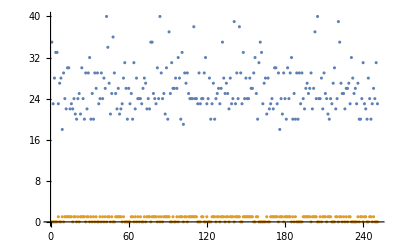

```mathematica
ListPlot[Transpose[bC⟦2;;,{bMI,menopause}⟧]]
```

```mathematica
meN46=LogitModelFit[bC⟦2;;,{M46,menopause}⟧,x,
x]
meN46["BestFit"]
meN46["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-0.363752+«22» x))]

1/(1+ⅇ^(-0.363752+0.00365689 x))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 0.363752 | 0.409682 | 0.887889 | 0.374601
x | -0.00365689 | 0.0417172 | -0.0876589 | 0.930148

```mathematica
meN47=LogitModelFit[bC⟦2;;,{M47,menopause}⟧,x,
x]
meN47["BestFit"]
meN47["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-0.409406+«21» x))]

1/(1+ⅇ^(-0.409406+0.042347 x))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 0.409406 | 0.37053 | 1.10492 | 0.269195
x | -0.042347 | 0.18447 | -0.22956 | 0.818433

```mathematica
meN48=LogitModelFit[bC⟦2;;,{M48,menopause}⟧,x,
x]
meN48["BestFit"]
meN48["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-0.497405+«21» x))]

1/(1+ⅇ^(-0.497405+0.0113884 x))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 0.497405 | 0.367811 | 1.35234 | 0.176266
x | -0.0113884 | 0.0233673 | -0.487362 | 0.626002

```mathematica
meN49=LogitModelFit[bC⟦2;;,{M49,menopause}⟧,x,
x]
meN49["BestFit"]
meN49["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-1.33739+«21» x))]

1/(1+ⅇ^(-1.33739+0.0134159 x))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 1.33739 | 0.376676 | 3.55052 | 0.000384471
x | -0.0134159 | 0.0046913 | -2.85974 | 0.00423994

```mathematica
meN50=LogitModelFit[bC⟦2;;,{M50,menopause}⟧,x,
x]
meN50["BestFit"]
meN50["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-1.11493+«21» x))]

1/(1+ⅇ^(-1.11493+0.0157888 x))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 1.11493 | 0.48422 | 2.30252 | 0.0213058
x | -0.0157888 | 0.00934149 | -1.69018 | 0.0909943

```mathematica
meN51=LogitModelFit[bC⟦2;;,{M51,menopause}⟧,x,
x]
meN51["BestFit"]
meN51["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(0.478734-«20» x))]

1/(1+ⅇ^(0.478734-0.268599 x))

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.478734 | 0.342669 | -1.39707 | 0.162391
x | 0.268599 | 0.107262 | 2.50415 | 0.0122747

```mathematica
meN52=LogitModelFit[bC⟦2;;,{M52,menopause}⟧,x,
x]
meN52["BestFit"]
meN52["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-0.502003+«20» x))]

1/(1+ⅇ^(-0.502003+0.247643 x))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 0.502003 | 0.278153 | 1.80478 | 0.0711098
x | -0.247643 | 0.353739 | -0.700072 | 0.483882

```mathematica
meN53=LogitModelFit[bC⟦2;;,{M53,menopause}⟧,x,
x]
meN53["BestFit"]
meN53["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(0.0633588-«19» x))]

1/(1+ⅇ^(0.0633588-0.392758 x))

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.0633588 | 0.306568 | -0.206671 | 0.836267
x | 0.392758 | 0.281677 | 1.39436 | 0.16321

```mathematica
meN54=LogitModelFit[bC⟦2;;,{M54,menopause}⟧,x,
x]
meN54["BestFit"]
meN54["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-0.986042+«19» x))]

1/(1+ⅇ^(-0.986042+0.36226 x))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 0.986042 | 0.354163 | 2.78415 | 0.00536685
x | -0.36226 | 0.181583 | -1.99501 | 0.0460416

```mathematica
meN55=LogitModelFit[bC⟦2;;,{M55,menopause}⟧,x,
x]
meN55["BestFit"]
meN55["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-0.325647-«22» x))]

1/(1+ⅇ^(-0.325647-0.000892854 x))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 0.325647 | 0.31637 | 1.02932 | 0.303328
x | 0.000892854 | 0.0646002 | 0.0138212 | 0.988973

```mathematica
meN56=LogitModelFit[bC⟦2;;,{M56,menopause}⟧,x,
x]
meN56["BestFit"]
meN56["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-1.12435+«20» x))]

1/(1+ⅇ^(-1.12435+0.10405 x))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 1.12435 | 0.359086 | 3.13115 | 0.00174125
x | -0.10405 | 0.0436553 | -2.38345 | 0.017151

```mathematica
meN57=LogitModelFit[bC⟦2;;,{M57,menopause}⟧,x,
x]
meN57["BestFit"]
meN57["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-2.18004+«20» x))]

1/(1+ⅇ^(-2.18004+0.0675667 x))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 2.18004 | 0.397702 | 5.48159 | 4.21525×10^-8
x | -0.0675667 | 0.013713 | -4.9272 | 8.34159×10^-7

```mathematica
meN58=LogitModelFit[bC⟦2;;,{M58,menopause}⟧,x,
x]
meN58["BestFit"]
meN58["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-1.862+«20» x))]

1/(1+ⅇ^(-1.862+0.0741751 x))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 1.862 | 0.438393 | 4.24734 | 0.0000216328
x | -0.0741751 | 0.0201432 | -3.68238 | 0.000231064

```mathematica
meN59=LogitModelFit[bC⟦2;;,{M59,menopause}⟧,x,
x]
meN59["BestFit"]
meN59["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-1.27347+«19» x))]

1/(1+ⅇ^(-1.27347+0.423824 x))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 1.27347 | 0.41347 | 3.07996 | 0.00207026
x | -0.423824 | 0.17585 | -2.41015 | 0.015946

```mathematica
meN60=LogitModelFit[bC⟦2;;,{M60,menopause}⟧,x,
x]
meN60["BestFit"]
meN60["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-0.13449-«21» x))]

1/(1+ⅇ^(-0.13449-0.020257 x))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 0.13449 | 0.414071 | 0.324799 | 0.745333
x | 0.020257 | 0.0409494 | 0.494683 | 0.620824

```mathematica
meN61=LogitModelFit[bC⟦2;;,{M61,menopause}⟧,x,
x]
meN61["BestFit"]
meN61["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-1.46458+«20» x))]

1/(1+ⅇ^(-1.46458+0.0204933 x))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 1.46458 | 0.417882 | 3.50477 | 0.000456996
x | -0.0204933 | 0.00715956 | -2.86237 | 0.0042049

```mathematica
meN62=LogitModelFit[bC⟦2;;,{M62,menopause}⟧,x,
x]
meN62["BestFit"]
meN62["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(0.174968-«20» x))]

1/(1+ⅇ^(0.174968-0.0163771 x))

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.174968 | 0.397226 | -0.440475 | 0.659593
x | 0.0163771 | 0.0122728 | 1.33442 | 0.182067

```mathematica
meN63=LogitModelFit[bC⟦2;;,{M63,menopause}⟧,x,
x]
meN63["BestFit"]
meN63["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-0.342614+«22» x))]

1/(1+ⅇ^(-0.342614+0.000678668 x))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 0.342614 | 0.394028 | 0.869519 | 0.384564
x | -0.000678668 | 0.0195007 | -0.0348021 | 0.972238

```mathematica
meN64=LogitModelFit[bC⟦2;;,{M64,menopause}⟧,x,
x]
meN64["BestFit"]
meN64["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-0.812983+«20» x))]

1/(1+ⅇ^(-0.812983+0.0244715 x))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 0.812983 | 0.377796 | 2.15191 | 0.0314046
x | -0.0244715 | 0.0179335 | -1.36457 | 0.172387

```mathematica
meN65=LogitModelFit[bC⟦2;;,{M65,menopause}⟧,x,
x]
meN65["BestFit"]
meN65["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-0.919589+«21» x))]

1/(1+ⅇ^(-0.919589+0.00231615 x))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 0.919589 | 0.382286 | 2.4055 | 0.0161503
x | -0.00231615 | 0.00140929 | -1.64348 | 0.100283

```mathematica
meN66=LogitModelFit[bC⟦2;;,{M66,menopause}⟧,x,
x]
meN66["BestFit"]
meN66["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-0.96326+«21» x))]

1/(1+ⅇ^(-0.96326+0.0373457 x))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 0.96326 | 0.340631 | 2.82787 | 0.00468594
x | -0.0373457 | 0.018508 | -2.01782 | 0.04361

```mathematica
meN67=LogitModelFit[bC⟦2;;,{M67,menopause}⟧,x,
x]
meN67["BestFit"]
meN67["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-0.176896-«21» x))]

1/(1+ⅇ^(-0.176896-0.0102368 x))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 0.176896 | 0.368147 | 0.480504 | 0.630869
x | 0.0102368 | 0.023176 | 0.441698 | 0.658708

```mathematica
meN68=LogitModelFit[bC⟦2;;,{M68,menopause}⟧,x,
x]
meN68["BestFit"]
meN68["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-1.04168+«20» x))]

1/(1+ⅇ^(-1.04168+0.0513942 x))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 1.04168 | 0.380277 | 2.73927 | 0.00615758
x | -0.0513942 | 0.0257675 | -1.99453 | 0.0460938

```mathematica
meN69=LogitModelFit[bC⟦2;;,{M69,menopause}⟧,x,
x]
meN69["BestFit"]
meN69["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-1.07307+«19» x))]

1/(1+ⅇ^(-1.07307+0.166653 x))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 1.07307 | 0.474921 | 2.25947 | 0.0238544
x | -0.166653 | 0.102163 | -1.63124 | 0.10284

```mathematica
meN70=LogitModelFit[bC⟦2;;,{M70,menopause}⟧,x,
x]
meN70["BestFit"]
meN70["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-0.561975+«22» x))]

1/(1+ⅇ^(-0.561975+0.0044191 x))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 0.561975 | 0.6129 | 0.916911 | 0.359189
x | -0.0044191 | 0.0113913 | -0.387935 | 0.698064

```mathematica
meN71=LogitModelFit[bC⟦2;;,{M71,menopause}⟧,x,
x]
meN71["BestFit"]
meN71["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-1.57543+«20» x))]

1/(1+ⅇ^(-1.57543+0.186243 x))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 1.57543 | 0.543134 | 2.90062 | 0.00372421
x | -0.186243 | 0.0785541 | -2.37089 | 0.0177454

```mathematica
meN72=LogitModelFit[bC⟦2;;,{M72,menopause}⟧,x,
x]
meN72["BestFit"]
meN72["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-1.3451+«20» x))]

1/(1+ⅇ^(-1.3451+0.0786235 x))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 1.3451 | 0.455037 | 2.95601 | 0.00311644
x | -0.0786235 | 0.0336555 | -2.33612 | 0.0194847

```mathematica
meN73=LogitModelFit[bC⟦2;;,{M73,menopause}⟧,x,
x]
meN73["BestFit"]
meN73["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-1.52033+«19» x))]

1/(1+ⅇ^(-1.52033+0.234289 x))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 1.52033 | 0.503465 | 3.01974 | 0.00252994
x | -0.234289 | 0.0953661 | -2.45674 | 0.0140206

```mathematica
meN74=LogitModelFit[bC⟦2;;,{M74,menopause}⟧,x,
x]
meN74["BestFit"]
meN74["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-1.15736+«20» x))]

1/(1+ⅇ^(-1.15736+0.0459108 x))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 1.15736 | 0.539137 | 2.14668 | 0.0318186
x | -0.0459108 | 0.0289487 | -1.58594 | 0.112754

```mathematica
meN75=LogitModelFit[bC⟦2;;,{M75,menopause}⟧,x,
x]
meN75["BestFit"]
meN75["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-0.459821+«21» x))]

1/(1+ⅇ^(-0.459821+0.0163668 x))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 0.459821 | 0.488405 | 0.941475 | 0.346462
x | -0.0163668 | 0.0592172 | -0.276385 | 0.782252

```mathematica
meN76=LogitModelFit[bC⟦2;;,{M76,menopause}⟧,x,
x]
meN76["BestFit"]
meN76["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-0.785187+«20» x))]

1/(1+ⅇ^(-0.785187+0.141517 x))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 0.785187 | 0.488725 | 1.6066 | 0.108142
x | -0.141517 | 0.146158 | -0.968247 | 0.332921

```mathematica
meN77=LogitModelFit[bC⟦2;;,{M77,menopause}⟧,x,
x]
meN77["BestFit"]
meN77["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-0.574705+«20» x))]

1/(1+ⅇ^(-0.574705+0.0709358 x))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 0.574705 | 0.381064 | 1.50816 | 0.131515
x | -0.0709358 | 0.103669 | -0.684256 | 0.493814

```mathematica
meN78=LogitModelFit[bC⟦2;;,{M78,menopause}⟧,x,
x]
meN78["BestFit"]
meN78["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-0.681289+«21» x))]

1/(1+ⅇ^(-0.681289+0.0220509 x))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 0.681289 | 0.487272 | 1.39817 | 0.162062
x | -0.0220509 | 0.0294257 | -0.749373 | 0.453633

```mathematica
meN79=LogitModelFit[bC⟦2;;,{M79,menopause}⟧,x,
x]
meN79["BestFit"]
meN79["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-0.57783+«20» x))]

1/(1+ⅇ^(-0.57783+0.0290019 x))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 0.57783 | 0.542246 | 1.06562 | 0.286593
x | -0.0290019 | 0.0615053 | -0.471535 | 0.637259

```mathematica
meN80=LogitModelFit[bC⟦2;;,{M80,menopause}⟧,x,
x]
meN80["BestFit"]
meN80["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-0.49814+«20» x))]

1/(1+ⅇ^(-0.49814+0.065917 x))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 0.49814 | 0.388901 | 1.28089 | 0.200231
x | -0.065917 | 0.143458 | -0.459487 | 0.645885

```mathematica
meN81=LogitModelFit[bC⟦2;;,{M81,menopause}⟧,x,
x]
meN81["BestFit"]
meN81["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-1.06992+«20» x))]

1/(1+ⅇ^(-1.06992+0.11553 x))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 1.06992 | 0.472536 | 2.26422 | 0.0235608
x | -0.11553 | 0.070688 | -1.63436 | 0.102183

```mathematica
meN82=LogitModelFit[bC⟦2;;,{M82,menopause}⟧,x,
x]
meN82["BestFit"]
meN82["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-0.706658+«20» x))]

1/(1+ⅇ^(-0.706658+0.0714302 x))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 0.706658 | 0.440506 | 1.6042 | 0.108671
x | -0.0714302 | 0.0796578 | -0.896713 | 0.369872

```mathematica
meN83=LogitModelFit[bC⟦2;;,{M83,menopause}⟧,x,
x]
meN83["BestFit"]
meN83["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-0.780589+«20» x))]

1/(1+ⅇ^(-0.780589+0.131338 x))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 0.780589 | 0.351623 | 2.21996 | 0.0264216
x | -0.131338 | 0.0950403 | -1.38192 | 0.166995

```mathematica
meN84=LogitModelFit[bC⟦2;;,{M84,menopause}⟧,x,
x]
meN84["BestFit"]
meN84["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-0.44106+«21» x))]

1/(1+ⅇ^(-0.44106+0.012074 x))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 0.44106 | 0.452829 | 0.974012 | 0.330051
x | -0.012074 | 0.0470368 | -0.256693 | 0.797416

```mathematica
meN85=LogitModelFit[bC⟦2;;,{M85,menopause}⟧,x,
x]
meN85["BestFit"]
meN85["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-1.15349+«21» x))]

1/(1+ⅇ^(-1.15349+0.0270027 x))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 1.15349 | 0.445429 | 2.58961 | 0.00960837
x | -0.0270027 | 0.0139227 | -1.93947 | 0.0524436

```mathematica
meN86=LogitModelFit[bC⟦2;;,{M86,menopause}⟧,x,
x]
meN86["BestFit"]
meN86["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-0.852479+«19» x))]

1/(1+ⅇ^(-0.852479+1.76932 x))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 0.852479 | 0.443341 | 1.92285 | 0.0544987
x | -1.76932 | 1.43107 | -1.23636 | 0.216325

```mathematica
meN87=LogitModelFit[bC⟦2;;,{M87,menopause}⟧,x,
x]
meN87["BestFit"]
meN87["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-0.66975+«21» x))]

1/(1+ⅇ^(-0.66975+0.015559 x))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 0.66975 | 0.185586 | 3.60884 | 0.00030757
x | -0.015559 | 0.00611516 | -2.54434 | 0.0109486

```mathematica
meN88=LogitModelFit[bC⟦2;;,{M88,menopause}⟧,x,
x]
meN88["BestFit"]
meN88["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-0.742069+«21» x))]

1/(1+ⅇ^(-0.742069+0.0184216 x))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 0.742069 | 0.183454 | 4.04499 | 0.0000523253
x | -0.0184216 | 0.00594743 | -3.0974 | 0.00195227

```mathematica
meN89=LogitModelFit[bC⟦2;;,{M89,menopause}⟧,x,
x]
meN89["BestFit"]
meN89["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-0.742478+«21» x))]

1/(1+ⅇ^(-0.742478+0.00624612 x))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 0.742478 | 0.189344 | 3.92132 | 0.0000880643
x | -0.00624612 | 0.00211328 | -2.95565 | 0.00312014

```mathematica
meN90=LogitModelFit[bC⟦2;;,{M90,menopause}⟧,x,
x]
meN90["BestFit"]
meN90["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-1.02687+«21» x))]

1/(1+ⅇ^(-1.02687+0.00415218 x))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 1.02687 | 0.232545 | 4.41577 | 0.0000100651
x | -0.00415218 | 0.00115255 | -3.60261 | 0.000315044

```mathematica
meN91=LogitModelFit[bC⟦2;;,{M91,menopause}⟧,x,
x]
meN91["BestFit"]
meN91["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-0.72719+«20» x))]

1/(1+ⅇ^(-0.72719+0.0345055 x))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 0.72719 | 0.181878 | 3.99824 | 0.0000638159
x | -0.0345055 | 0.0114942 | -3.00199 | 0.00268222

```mathematica
meN92=LogitModelFit[bC⟦2;;,{M92,menopause}⟧,x,
x]
meN92["BestFit"]
meN92["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-0.70326+«20» x))]

1/(1+ⅇ^(-0.70326+0.140746 x))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 0.70326 | 0.192274 | 3.65758 | 0.000254606
x | -0.140746 | 0.0558823 | -2.51862 | 0.0117815

```mathematica
meN93=LogitModelFit[bC⟦2;;,{M93,menopause}⟧,x,
x]
meN93["BestFit"]
meN93["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-0.886936+«21» x))]

1/(1+ⅇ^(-0.886936+0.00809567 x))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 0.886936 | 0.204501 | 4.33708 | 0.0000144387
x | -0.00809567 | 0.0023854 | -3.39385 | 0.000689177

```mathematica
meN94=LogitModelFit[bC⟦2;;,{M94,menopause}⟧,x,
x]
meN94["BestFit"]
meN94["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-0.413431+«21» x))]

1/(1+ⅇ^(-0.413431+0.00813962 x))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 0.413431 | 0.457185 | 0.904298 | 0.365837
x | -0.00813962 | 0.0426146 | -0.191006 | 0.848521

```mathematica
meN95=LogitModelFit[bC⟦2;;,{M95,menopause}⟧,x,
x]
meN95["BestFit"]
meN95["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-0.919853+«22» x))]

1/(1+ⅇ^(-0.919853+0.00336339 x))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 0.919853 | 0.21277 | 4.32323 | 0.0000153763
x | -0.00336339 | 0.000973584 | -3.45464 | 0.000551021

```mathematica
meN96=LogitModelFit[bC⟦2;;,{M96,menopause}⟧,x,
x]
meN96["BestFit"]
meN96["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-1.68307+«21» x))]

1/(1+ⅇ^(-1.68307+0.00209545 x))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 1.68307 | 0.317482 | 5.30131 | 1.14975×10^-7
x | -0.00209545 | 0.000446395 | -4.69416 | 2.677×10^-6

```mathematica
meN97=LogitModelFit[bC⟦2;;,{M97,menopause}⟧,x,
x]
meN97["BestFit"]
meN97["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-1.08762+«21» x))]

1/(1+ⅇ^(-1.08762+0.0119026 x))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 1.08762 | 0.242916 | 4.47735 | 7.55738×10^-6
x | -0.0119026 | 0.00329426 | -3.61312 | 0.000302538

```mathematica
meN98=LogitModelFit[bC⟦2;;,{M98,menopause}⟧,x,
x]
meN98["BestFit"]
meN98["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-1.37545+«22» x))]

1/(1+ⅇ^(-1.37545+0.00173486 x))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 1.37545 | 0.309427 | 4.44516 | 8.78259×10^-6
x | -0.00173486 | 0.000463152 | -3.74577 | 0.000179844

```mathematica
meN99=LogitModelFit[bC⟦2;;,{M99,menopause}⟧,x,
x]
meN99["BestFit"]
meN99["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-1.31523+«20» x))]

1/(1+ⅇ^(-1.31523+0.211273 x))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 1.31523 | 0.268148 | 4.90486 | 9.34944×10^-7
x | -0.211273 | 0.0516379 | -4.09142 | 0.0000428733

```mathematica
meN100=LogitModelFit[bC⟦2;;,{M100,menopause}⟧,x,
x]
meN100["BestFit"]
meN100["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-1.22327+«20» x))]

1/(1+ⅇ^(-1.22327+0.344472 x))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 1.22327 | 0.267454 | 4.57375 | 4.79061×10^-6
x | -0.344472 | 0.0906532 | -3.79988 | 0.000144765

```mathematica
meN101=LogitModelFit[bC⟦2;;,{M101,menopause}⟧,x,
x]
meN101["BestFit"]
meN101["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-0.794408+«22» x))]

1/(1+ⅇ^(-0.794408+0.00362956 x))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 0.794408 | 0.220552 | 3.60191 | 0.000315888
x | -0.00362956 | 0.00138903 | -2.61301 | 0.00897496

```mathematica
meN102=LogitModelFit[bC⟦2;;,{M102,menopause}⟧,x,
x]
meN102["BestFit"]
meN102["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-0.761533+«22» x))]

1/(1+ⅇ^(-0.761533+0.00439187 x))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 0.761533 | 0.208254 | 3.65675 | 0.000255433
x | -0.00439187 | 0.00167714 | -2.61867 | 0.00882725

```mathematica
meN103=LogitModelFit[bC⟦2;;,{M103,menopause}⟧,x,
x]
meN103["BestFit"]
meN103["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-0.997865+«20» x))]

1/(1+ⅇ^(-0.997865+0.206049 x))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 0.997865 | 0.256604 | 3.88873 | 0.00010077
x | -0.206049 | 0.0698477 | -2.94998 | 0.00317798

```mathematica
meN104=LogitModelFit[bC⟦2;;,{M104,menopause}⟧,x,
x]
meN104["BestFit"]
meN104["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-0.894865+«21» x))]

1/(1+ⅇ^(-0.894865+0.00465573 x))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 0.894865 | 0.230072 | 3.8895 | 0.000100452
x | -0.00465573 | 0.00156386 | -2.97708 | 0.00291009

```mathematica
meN105=LogitModelFit[bC⟦2;;,{M105,menopause}⟧,x,
x]
meN105["BestFit"]
meN105["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-0.49397+«20» x))]

1/(1+ⅇ^(-0.49397+0.0656012 x))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 0.49397 | 0.165775 | 2.97976 | 0.00288477
x | -0.0656012 | 0.0419081 | -1.56536 | 0.117499

```mathematica
meN106=LogitModelFit[bC⟦2;;,{M106,menopause}⟧,x,
x]
meN106["BestFit"]
meN106["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-0.410712+«20» x))]

1/(1+ⅇ^(-0.410712+0.0674283 x))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 0.410712 | 0.157423 | 2.60896 | 0.00908169
x | -0.0674283 | 0.0758044 | -0.889504 | 0.373732

```mathematica
meN107=LogitModelFit[bC⟦2;;,{M107,menopause}⟧,x,
x]
meN107["BestFit"]
meN107["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-0.552852+«20» x))]

1/(1+ⅇ^(-0.552852+0.0327861 x))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 0.552852 | 0.17051 | 3.24235 | 0.0011855
x | -0.0327861 | 0.0165037 | -1.98658 | 0.0469685

```mathematica
meN108=LogitModelFit[bC⟦2;;,{M108,menopause}⟧,x,
x]
meN108["BestFit"]
meN108["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-0.569127+«19» x))]

1/(1+ⅇ^(-0.569127+0.0534274 x))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 0.569127 | 0.165928 | 3.42997 | 0.000603658
x | -0.0534274 | 0.0236819 | -2.25605 | 0.0240676

```mathematica
meN109=LogitModelFit[bC⟦2;;,{M109,menopause}⟧,x,
x]
meN109["BestFit"]
meN109["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-0.59015+«20» x))]

1/(1+ⅇ^(-0.59015+0.189682 x))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 0.59015 | 0.181175 | 3.25734 | 0.00112461
x | -0.189682 | 0.0934388 | -2.03002 | 0.0423547

```mathematica
meN110=LogitModelFit[bC⟦2;;,{M110,menopause}⟧,x,
x]
meN110["BestFit"]
meN110["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-0.831318+«19» x))]

1/(1+ⅇ^(-0.831318+0.320881 x))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 0.831318 | 0.240473 | 3.45702 | 0.000546185
x | -0.320881 | 0.130627 | -2.45647 | 0.014031

```mathematica
meN111=LogitModelFit[bC⟦2;;,{M111,menopause}⟧,x,
x]
meN111["BestFit"]
meN111["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-0.599332+«20» x))]

1/(1+ⅇ^(-0.599332+0.015666 x))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 0.599332 | 0.17514 | 3.42201 | 0.000621601
x | -0.015666 | 0.0069403 | -2.25725 | 0.0239927

```mathematica
meN112=LogitModelFit[bC⟦2;;,{M112,menopause}⟧,x,
x]
meN112["BestFit"]
meN112["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-0.591722+«20» x))]

1/(1+ⅇ^(-0.591722+0.0452181 x))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 0.591722 | 0.182216 | 3.24736 | 0.0011648
x | -0.0452181 | 0.022463 | -2.013 | 0.0441145

```mathematica
meN113=LogitModelFit[bC⟦2;;,{M113,menopause}⟧,x,
x]
meN113["BestFit"]
meN113["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-0.928274+«20» x))]

1/(1+ⅇ^(-0.928274+0.231666 x))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 0.928274 | 0.229174 | 4.05052 | 0.0000511035
x | -0.231666 | 0.0742582 | -3.11973 | 0.00181015

```mathematica
meN114=LogitModelFit[bC⟦2;;,{M114,menopause}⟧,x,
x]
meN114["BestFit"]
meN114["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-1.06705+«20» x))]

1/(1+ⅇ^(-1.06705+0.24216 x))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 1.06705 | 0.228882 | 4.66201 | 3.13141×10^-6
x | -0.24216 | 0.0630079 | -3.84332 | 0.000121382

```mathematica
meN115=LogitModelFit[bC⟦2;;,{M115,menopause}⟧,x,
x]
meN115["BestFit"]
meN115["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-0.764367+«21» x))]

1/(1+ⅇ^(-0.764367+0.0135965 x))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 0.764367 | 0.20297 | 3.7659 | 0.000165948
x | -0.0135965 | 0.00493965 | -2.75253 | 0.00591371

```mathematica
meN116=LogitModelFit[bC⟦2;;,{M116,menopause}⟧,x,
x]
meN116["BestFit"]
meN116["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-0.715501+«20» x))]

1/(1+ⅇ^(-0.715501+0.0462598 x))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 0.715501 | 0.214832 | 3.33051 | 0.000866856
x | -0.0462598 | 0.0206081 | -2.24473 | 0.0247852

```mathematica
meN117=LogitModelFit[bC⟦2;;,{M117,menopause}⟧,x,
x]
meN117["BestFit"]
meN117["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-1.11368+«20» x))]

1/(1+ⅇ^(-1.11368+0.279423 x))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 1.11368 | 0.244819 | 4.54899 | 5.39031×10^-6
x | -0.279423 | 0.0755424 | -3.69889 | 0.000216546

```mathematica
meN118=LogitModelFit[bC⟦2;;,{M118,menopause}⟧,x,
x]
meN118["BestFit"]
meN118["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-1.12883+«20» x))]

1/(1+ⅇ^(-1.12883+0.110611 x))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 1.12883 | 0.232353 | 4.85824 | 1.18436×10^-6
x | -0.110611 | 0.0270923 | -4.08273 | 0.0000445094

```mathematica
meN119=LogitModelFit[bC⟦2;;,{M119,menopause}⟧,x,
x]
meN119["BestFit"]
meN119["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-1.36231+«19» x))]

1/(1+ⅇ^(-1.36231+0.177753 x))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 1.36231 | 0.269763 | 5.05002 | 4.41763×10^-7
x | -0.177753 | 0.041046 | -4.33057 | 0.0000148725

```mathematica
meN120=LogitModelFit[bC⟦2;;,{M120,menopause}⟧,x,
x]
meN120["BestFit"]
meN120["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-1.2809+«19» x))]

1/(1+ⅇ^(-1.2809+2.65313 x))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 1.2809 | 0.290983 | 4.40197 | 0.0000107273
x | -2.65313 | 0.734708 | -3.61113 | 0.000304867

```mathematica
meN121=LogitModelFit[bC⟦2;;,{M121,menopause}⟧,x,
x]
meN121["BestFit"]
meN121["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-1.08536+«21» x))]

1/(1+ⅇ^(-1.08536+0.00962229 x))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 1.08536 | 0.249747 | 4.34582 | 0.0000138753
x | -0.00962229 | 0.00270779 | -3.55356 | 0.000380052

```mathematica
meN122=LogitModelFit[bC⟦2;;,{M122,menopause}⟧,x,
x]
meN122["BestFit"]
meN122["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-0.898641+«20» x))]

1/(1+ⅇ^(-0.898641+0.0693466 x))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 0.898641 | 0.230015 | 3.90688 | 0.0000934948
x | -0.0693466 | 0.0232135 | -2.98733 | 0.00281421

```mathematica
meN123=LogitModelFit[bC⟦2;;,{M123,menopause}⟧,x,
x]
meN123["BestFit"]
meN123["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-0.979268+«19» x))]

1/(1+ⅇ^(-0.979268+0.541806 x))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 0.979268 | 0.26035 | 3.76135 | 0.000168997
x | -0.541806 | 0.189227 | -2.86326 | 0.00419301

```mathematica
meN124=LogitModelFit[bC⟦2;;,{M124,menopause}⟧,x,
x]
meN124["BestFit"]
meN124["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-1.54574+«20» x))]

1/(1+ⅇ^(-1.54574+0.0636565 x))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 1.54574 | 0.29063 | 5.31859 | 1.04572×10^-7
x | -0.0636565 | 0.0137219 | -4.63904 | 3.50038×10^-6

```mathematica
meN125=LogitModelFit[bC⟦2;;,{M125,menopause}⟧,x,
x]
meN125["BestFit"]
meN125["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-1.21832+«20» x))]

1/(1+ⅇ^(-1.21832+0.110683 x))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 1.21832 | 0.261198 | 4.66436 | 3.09578×10^-6
x | -0.110683 | 0.0285715 | -3.87391 | 0.000107103

```mathematica
meN126=LogitModelFit[bC⟦2;;,{M126,menopause}⟧,x,
x]
meN126["BestFit"]
meN126["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-1.21239+«19» x))]

1/(1+ⅇ^(-1.21239+0.596647 x))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 1.21239 | 0.26787 | 4.52605 | 6.00957×10^-6
x | -0.596647 | 0.158788 | -3.75752 | 0.000171606

```mathematica
meN127=LogitModelFit[bC⟦2;;,{M127,menopause}⟧,x,
x]
meN127["BestFit"]
meN127["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-0.885961+«21» x))]

1/(1+ⅇ^(-0.885961+0.0427939 x))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 0.885961 | 0.223722 | 3.96011 | 0.0000749162
x | -0.0427939 | 0.0141076 | -3.03341 | 0.00241809

```mathematica
meN128=LogitModelFit[bC⟦2;;,{M128,menopause}⟧,x,
x]
meN128["BestFit"]
meN128["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-1.05956+«19» x))]

1/(1+ⅇ^(-1.05956+0.513631 x))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 1.05956 | 0.255056 | 4.15425 | 0.0000326361
x | -0.513631 | 0.159013 | -3.23011 | 0.00123741

```mathematica
meN129=LogitModelFit[bC⟦2;;,{M129,menopause}⟧,x,
x]
meN129["BestFit"]
meN129["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-1.45947+«19» x))]

1/(1+ⅇ^(-1.45947+0.134668 x))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 1.45947 | 0.298389 | 4.89115 | 1.00247×10^-6
x | -0.134668 | 0.0320779 | -4.19815 | 0.0000269104

```mathematica
meN130=LogitModelFit[bC⟦2;;,{M130,menopause}⟧,x,
x]
meN130["BestFit"]
meN130["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-0.290982-«21» x))]

1/(1+ⅇ^(-0.290982-0.00641188 x))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 0.290982 | 0.260189 | 1.11835 | 0.263419
x | 0.00641188 | 0.0376112 | 0.170478 | 0.864634

```mathematica
meN131=LogitModelFit[bC⟦2;;,{M131,menopause}⟧,x,
x]
meN131["BestFit"]
meN131["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-0.534396+«21» x))]

1/(1+ⅇ^(-0.534396+0.0473415 x))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 0.534396 | 0.163555 | 3.26737 | 0.0010855
x | -0.0473415 | 0.024064 | -1.96732 | 0.0491468

```mathematica
meN131=LogitModelFit[bC⟦2;;,{M131,menopause}⟧,x,
x]
meN131["BestFit"]
meN131["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-0.534396+«21» x))]

1/(1+ⅇ^(-0.534396+0.0473415 x))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 0.534396 | 0.163555 | 3.26737 | 0.0010855
x | -0.0473415 | 0.024064 | -1.96732 | 0.0491468

```mathematica
meN132=LogitModelFit[bC⟦2;;,{M132,menopause}⟧,x,
x]
meN132["BestFit"]
meN132["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-1.36554+«20» x))]

1/(1+ⅇ^(-1.36554+0.0504483 x))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 1.36554 | 0.256696 | 5.31969 | 1.03945×10^-7
x | -0.0504483 | 0.0110196 | -4.57806 | 4.69298×10^-6

```mathematica
meN133=LogitModelFit[bC⟦2;;,{M133,menopause}⟧,x,
x]
meN133["BestFit"]
meN133["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-1.15036+«19» x))]

1/(1+ⅇ^(-1.15036+0.0851891 x))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 1.15036 | 0.244213 | 4.71047 | 2.47145×10^-6
x | -0.0851891 | 0.0218064 | -3.90661 | 0.0000936007

```mathematica
meN134=LogitModelFit[bC⟦2;;,{M134,menopause}⟧,x,
x]
meN134["BestFit"]
meN134["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-1.26281+«19» x))]

1/(1+ⅇ^(-1.26281+0.353354 x))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 1.26281 | 0.254757 | 4.95691 | 7.16249×10^-7
x | -0.353354 | 0.0853791 | -4.13865 | 0.0000349359

```mathematica
meN135=LogitModelFit[bC⟦2;;,{M135,menopause}⟧,x,
x]
meN135["BestFit"]
meN135["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-1.27193+«20» x))]

1/(1+ⅇ^(-1.27193+0.0775801 x))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 1.27193 | 0.262239 | 4.85027 | 1.23296×10^-6
x | -0.0775801 | 0.0188732 | -4.1106 | 0.0000394635

```mathematica
meN136=LogitModelFit[bC⟦2;;,{M136,menopause}⟧,x,
x]
meN136["BestFit"]
meN136["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-1.41336+«20» x))]

1/(1+ⅇ^(-1.41336+0.0831798 x))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 1.41336 | 0.270175 | 5.23127 | 1.68351×10^-7
x | -0.0831798 | 0.0185811 | -4.47659 | 7.58439×10^-6

```mathematica
meN137=LogitModelFit[bC⟦2;;,{M137,menopause}⟧,x,
x]
meN137["BestFit"]
meN137["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-1.08654+«21» x))]

1/(1+ⅇ^(-1.08654+0.0527067 x))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 1.08654 | 0.221233 | 4.91128 | 9.04825×10^-7
x | -0.0527067 | 0.0129095 | -4.08278 | 0.0000445007

```mathematica
meN138=LogitModelFit[bC⟦2;;,{M138,menopause}⟧,x,
x]
meN138["BestFit"]
meN138["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-1.29258+«19» x))]

1/(1+ⅇ^(-1.29258+0.632789 x))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 1.29258 | 0.284746 | 4.53941 | 5.64119×10^-6
x | -0.632789 | 0.167524 | -3.77729 | 0.000158541

```mathematica
metmen=Import["C:\\Users\\oreol\\Desktop\\proj\\MenMet1.xlsx"];
metmen2=Import["C:\\Users\\oreol\\Desktop\\proj\\MenMet2.xlsx"];
```

```mathematica
data1=Flatten[metmen,1];
data2=Flatten[metmen2,1];
Length[data1]
Length[data2]
```

73

67

```mathematica
sdata1=data1[[2;;,3]];
nsdata2=data2[[2;;,3]];
```

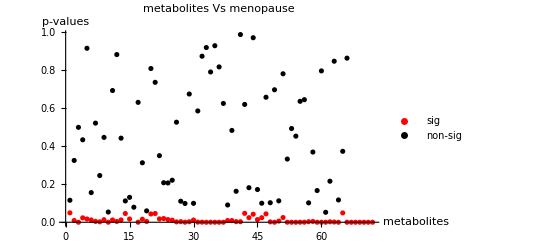

```mathematica
ListPlot[Tooltip[{sdata1,nsdata2}],PlotLegends->{"sig","non-sig"},PlotStyle->{Red, Black},PlotRange->All,PlotLabel->"metabolites Vs menopause",
	AxesLabel->{"metabolites", "p-values"}]
```

```mathematica
dt=Transpose[data1];
dt2=Transpose[data2];
```

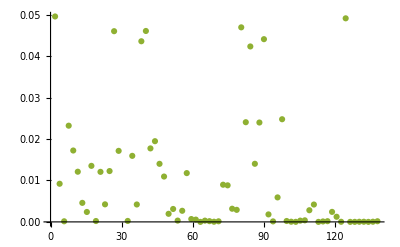

```mathematica
ListPlot[Tooltip[dt],DataRange->{0,138}]
```

```mathematica
data1[[2;;,1]];
```

```mathematica
metmenLM=LogitModelFit[bC⟦2;;,{M13,M20,M27,M31,M35,M36,M38,M41,M43,M44,M45,M49,M51,M54,M56,M57,M58,M59,M61,M66,M68,M71,M72,M73,M87,M88,M89,M90,M91,M92,M93,M95,M96,M97,M98,M99,M100,M101,M102,M103,M104,M107,M108,M109,M110,M111,M112,M113,M114,M115,M116,M117,M118,M119,M120,M121,M122,M123,M124,M125,M126,M127,M128,M129,M131,M132,M133,M134,M135,M136,M137,M138,menopause}⟧,{1,x,xM13,xM20,xM27,xM31,xM35,xM38,xM41,xM43,xM44,xM45,xM49,xM51,xM54,xM56,xM57,xM58,xM59,xM61,xM66,xM68,xM71,xM72,xM73,xM87,xM88,xM89,xM90,xM91,xM92,xM93,xM95,xM96,xM97,xM98,xM99,xM100,xM101,xM102,xM103,xM104,xM107,xM108,xM109,xM110,xM111,xM112,xM113,xM114,xM115,xM116,xM117,xM118,xM119,xM120,xM121,xM122,xM123,xM124,xM125,xM126,xM127,xM128,xM129,xM131,xM132,xM133,xM134,xM135,xM136,xM137,xM138},
{x,xM13,xM20,xM27,xM31,xM35,xM38,xM41,xM43,xM44,xM45,xM49,xM51,xM54,xM56,xM57,xM58,xM59,xM61,xM66,xM68,xM71,xM72,xM73,xM87,xM88,xM89,xM90,xM91,xM92,xM93,xM95,xM96,xM97,xM98,xM99,xM100,xM101,xM102,xM103,xM104,xM107,xM108,xM109,xM110,xM111,xM112,xM113,xM114,xM115,xM116,xM117,xM118,xM119,xM120,xM121,xM122,xM123,xM124,xM125,xM126,xM127,xM128,xM129,xM131,xM132,xM133,xM134,xM135,xM136,xM137,xM138}]
metmenLM["BestFit"]
metmenLM["ParameterTable"]
metmenLMent=metmenLM["ParameterTableEntries"];
metmenLMpos=Flatten[Position[metmenLMent[[All,4]],_?(#<0.05&)]]
```

FittedModel[1/(1+ⅇ^(«1»))]

1/(1+ⅇ^(-2.26501-1.79352 x+0.805819 xM100-0.00368839 xM101-0.0215799 xM102+0.362588 xM103+0.00802712 xM104-0.0499359 xM107+1.45277 xM108+1.00645 xM109-1.94772 xM110-0.27756 xM111+0.204149 xM112-2.31942 xM113+1.25016 xM114-0.187501 xM115-0.345947 xM116+1.80064 xM117+0.397104 xM118+0.573963 xM119+1.25252 xM120-0.00245662 xM121+0.514573 xM122+0.000937327 xM123+0.169014 xM124-0.202741 xM125-1.57876 xM126-0.105106 xM127+0.953545 xM128-0.305885 xM129+1.41928 xM13-0.25268 xM131-0.127239 xM132+0.105685 xM133+0.166217 xM134-0.0501949 xM135+0.21095 xM136+0.0520625 xM137-2.66802 xM138-0.0248308 xM20+0.0187678 xM27-0.00956798 xM31+0.379074 xM35-0.0820201 xM38+1.28093 xM41+0.060461 xM43+0.0613001 xM44-0.0257898 xM45-0.0491995 xM49-2.52438 xM51-0.779385 xM54-0.651417 xM56+0.129105 xM57+0.0668057 xM58+1.52685 xM59+0.00910192 xM61+0.00412322 xM66-0.0226436 xM68-0.337412 xM71-0.0272214 xM72-0.0503597 xM73-0.150209 xM87+0.0360956 xM88-0.00359937 xM89+0.000633242 xM90-0.206326 xM91-0.10329 xM92+0.0596706 xM93+0.00138565 xM95+0.00186474 xM96-0.00438292 xM97+0.00195942 xM98-0.168756 xM99))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 2.26501 | 1.47218 | 1.53854 | 0.123916
x | 1.79352 | 0.966374 | 1.85593 | 0.0634642
xM13 | -1.41928 | 0.978533 | -1.45041 | 0.146943
xM20 | 0.0248308 | 0.00855826 | 2.90139 | 0.00371513
xM27 | -0.0187678 | 0.0377826 | -0.496731 | 0.619379
xM31 | 0.00956798 | 0.0117038 | 0.817513 | 0.413636
xM35 | -0.379074 | 0.217816 | -1.74034 | 0.0817986
xM38 | 0.0820201 | 0.0485142 | 1.69064 | 0.0909051
xM41 | -1.28093 | 0.480387 | -2.66646 | 0.00766553
xM43 | -0.060461 | 0.0492038 | -1.22879 | 0.219152
xM44 | -0.0613001 | 0.0237528 | -2.58075 | 0.00985851
xM45 | 0.0257898 | 0.0479344 | 0.538023 | 0.590561
xM49 | 0.0491995 | 0.0306471 | 1.60536 | 0.108416
xM51 | 2.52438 | 1.04725 | 2.41048 | 0.0159315
xM54 | 0.779385 | 0.592866 | 1.31461 | 0.188643
xM56 | 0.651417 | 0.28725 | 2.26777 | 0.0233433
xM57 | -0.129105 | 0.0733821 | -1.75936 | 0.0785165
xM58 | -0.0668057 | 0.104538 | -0.639055 | 0.522787
xM59 | -1.52685 | 0.732458 | -2.08455 | 0.0371098
xM61 | -0.00910192 | 0.0324139 | -0.280803 | 0.778862
xM66 | -0.00412322 | 0.0642768 | -0.0641479 | 0.948852
xM68 | 0.0226436 | 0.111026 | 0.20395 | 0.838393
xM71 | 0.337412 | 0.447838 | 0.753426 | 0.451194
xM72 | 0.0272214 | 0.141935 | 0.191788 | 0.847908
xM73 | 0.0503597 | 0.432618 | 0.116407 | 0.90733
xM87 | 0.150209 | 0.109747 | 1.36868 | 0.171098
xM88 | -0.0360956 | 0.117844 | -0.306299 | 0.759377
xM89 | 0.00359937 | 0.0255143 | 0.141073 | 0.887813
xM90 | -0.000633242 | 0.01054 | -0.0600797 | 0.952092
xM91 | 0.206326 | 0.223433 | 0.923436 | 0.35578
xM92 | 0.10329 | 0.57692 | 0.179036 | 0.857909
xM93 | -0.0596706 | 0.0316842 | -1.88329 | 0.0596608
xM95 | -0.00138565 | 0.00947612 | -0.146226 | 0.883743
xM96 | -0.00186474 | 0.00358582 | -0.520033 | 0.603041
xM97 | 0.00438292 | 0.0391606 | 0.111922 | 0.910885
xM98 | -0.00195942 | 0.00380259 | -0.515285 | 0.606354
xM99 | 0.168756 | 0.394951 | 0.427283 | 0.669173
xM100 | -0.805819 | 0.708068 | -1.13805 | 0.255098
xM101 | 0.00368839 | 0.0110721 | 0.333126 | 0.739039
xM102 | 0.0215799 | 0.0127536 | 1.69207 | 0.0906331
xM103 | -0.362588 | 0.362015 | -1.00158 | 0.316546
xM104 | -0.00802712 | 0.0105357 | -0.761898 | 0.446121
xM107 | 0.0499359 | 0.160925 | 0.310305 | 0.756329
xM108 | -1.45277 | 0.475028 | -3.05829 | 0.00222607
xM109 | -1.00645 | 0.88521 | -1.13697 | 0.255552
xM110 | 1.94772 | 0.999351 | 1.94899 | 0.0512969
xM111 | 0.27756 | 0.132609 | 2.09308 | 0.0363422
xM112 | -0.204149 | 0.332737 | -0.613544 | 0.539517
xM113 | 2.31942 | 0.889069 | 2.60882 | 0.00908563
xM114 | -1.25016 | 0.615078 | -2.03252 | 0.042101
xM115 | 0.187501 | 0.0871478 | 2.15153 | 0.0314342
xM116 | 0.345947 | 0.210297 | 1.64504 | 0.099962
xM117 | -1.80064 | 0.788708 | -2.28303 | 0.0224287
xM118 | -0.397104 | 0.314925 | -1.26095 | 0.207327
xM119 | -0.573963 | 0.363716 | -1.57805 | 0.114554
xM120 | -1.25252 | 3.73256 | -0.335567 | 0.737197
xM121 | 0.00245662 | 0.0285999 | 0.085896 | 0.931549
xM122 | -0.514573 | 0.235787 | -2.18236 | 0.0290828
xM123 | -0.000937327 | 1.04388 | -0.000897926 | 0.999284
xM124 | -0.169014 | 0.187335 | -0.902202 | 0.366949
xM125 | 0.202741 | 0.262397 | 0.77265 | 0.43973
xM126 | 1.57876 | 1.1976 | 1.31827 | 0.187413
xM127 | 0.105106 | 0.0999214 | 1.05189 | 0.292851
xM128 | -0.953545 | 0.610477 | -1.56197 | 0.118296
xM129 | 0.305885 | 0.349838 | 0.87436 | 0.381922
xM131 | 0.25268 | 0.196844 | 1.28366 | 0.199262
xM132 | 0.127239 | 0.0718067 | 1.77196 | 0.0764005
xM133 | -0.105685 | 0.0734911 | -1.43807 | 0.150415
xM134 | -0.166217 | 0.452634 | -0.367221 | 0.713454
xM135 | 0.0501949 | 0.0852111 | 0.589065 | 0.555818
xM136 | -0.21095 | 0.153412 | -1.37506 | 0.169114
xM137 | -0.0520625 | 0.0763734 | -0.681684 | 0.495439
xM138 | 2.66802 | 1.01354 | 2.63238 | 0.00847887

{4,9,11,14,16,19,44,47,49,50,51,53,58,73}

```mathematica
bC⟦2;;,{M20,M41,M44,M51,M56,M59,M108,M111,M113,M114,M115,M117,M122,M138,menopause}⟧;
```

```mathematica
metmenLr1=LogitModelFit[bC⟦2;;,{M20,M41,M44,M51,M56,M59,M108,M111,M113,M114,M115,M117,M122,M138,menopause}⟧,
{1,xM20,xM41,xM44,xM51,xM56,xM59,xM108,xM111,xM113,xM114,xM115,xM117,xM122,xM138},
{xM20,xM41,xM44,xM51,xM56,xM59,xM108,xM111,xM113,xM114,xM115,xM117,xM122,xM138}]
metmenLr1["ParameterTable"]
metmenLr1ent=metmenLr1["ParameterTableEntries"];
metmenLr1pos=Flatten[Position[metmenLr1ent[[All,4]],_?(#<0.05&)]]
```

FittedModel[1/(1+ⅇ^(-3.09383+«19»+«20» xM59))]

| Estimate | Standard Error | z-Statistic | P-Value
1 | 3.09383 | 0.758834 | 4.07709 | 0.0000456029
xM20 | -0.347528 | 0.241893 | -1.4367 | 0.150802
xM41 | -0.525323 | 0.237999 | -2.20725 | 0.0272969
xM44 | -0.00911808 | 0.00609011 | -1.4972 | 0.134342
xM51 | 0.64949 | 0.16063 | 4.0434 | 0.0000526823
xM56 | 0.0706359 | 0.0788362 | 0.895983 | 0.370262
xM59 | -0.33879 | 0.234273 | -1.44613 | 0.14814
xM108 | -0.176486 | 0.146241 | -1.20681 | 0.227504
xM111 | 0.0724018 | 0.056009 | 1.29268 | 0.196121
xM113 | 1.1065 | 0.338848 | 3.26547 | 0.00109283
xM114 | -0.607884 | 0.234469 | -2.5926 | 0.00952544
xM115 | 0.0234835 | 0.0206697 | 1.13613 | 0.255903
xM117 | -0.959702 | 0.333524 | -2.87746 | 0.00400887
xM122 | -0.124838 | 0.0461034 | -2.70778 | 0.00677358
xM138 | 0.33463 | 0.278632 | 1.20097 | 0.229762

{1,3,5,10,11,13,14}

```mathematica
metmenLr2=LogitModelFit[bC⟦2;;,{M41,M51,M113,M114,M117,M122,menopause}⟧,
{1,xM41,xM51,xM113,xM114,xM117,xM122},
{xM41,xM51,xM113,xM114,xM117,xM122}]
metmenLr2["ParameterTable"]
metmenLr2ent=metmenLr2["ParameterTableEntries"];
metmenLr2pos=Flatten[Position[metmenLr2ent[[All,4]],_?(#<0.05&)]]
```

FittedModel[1/(1+ⅇ^(«1»))]

| Estimate | Standard Error | z-Statistic | P-Value
1 | 1.15043 | 0.534761 | 2.15129 | 0.031453
xM41 | -0.381067 | 0.156417 | -2.43623 | 0.0148412
xM51 | 0.45793 | 0.126422 | 3.62223 | 0.000292074
xM113 | 0.730684 | 0.289442 | 2.52445 | 0.0115878
xM114 | -0.234948 | 0.182275 | -1.28898 | 0.197406
xM117 | -0.630486 | 0.290013 | -2.17399 | 0.0297057
xM122 | -0.0456801 | 0.0289636 | -1.57715 | 0.11476

{1,2,3,4,6}

```mathematica
metmenLr3=LogitModelFit[bC⟦2;;,{M41,M51,M113,M117,menopause}⟧,
{1,xM41,xM51,xM113,xM117},
{xM41,xM51,xM113,xM117}]
metmenLr3["ParameterTable"]
metmenLr3ent=metmenLr3["ParameterTableEntries"];
metmenLr3pos=Flatten[Position[metmenLr3ent[[All,4]],_?(#<0.05&)]]
```

FittedModel[1/(1+ⅇ^(«1»))]

| Estimate | Standard Error | z-Statistic | P-Value
1 | 1.13003 | 0.521049 | 2.16877 | 0.0301004
xM41 | -0.41584 | 0.154345 | -2.69422 | 0.0070553
xM51 | 0.415618 | 0.123312 | 3.37046 | 0.00075044
xM113 | 0.532868 | 0.268078 | 1.98774 | 0.0468407
xM117 | -0.74389 | 0.264171 | -2.81594 | 0.0048635

{1,2,3,4,5}

Adding BMI to the equation while maintaining menopause as the response variable

```mathematica
meNbMimeT1=LogitModelFit[bC⟦2;;,{bMI,M1,menopause}⟧,{1,xM1,x},
{xM1,x}]
meNbMimeT1["BestFit"]
meNbMimeT1["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-2.57933-«1»+«20» xM1))]

1/(1+ⅇ^(-2.57933-1.49317 x+0.132327 xM1))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 2.57933 | 0.990889 | 2.60305 | 0.00923993
xM1 | -0.132327 | 0.0322342 | -4.10518 | 0.0000404002
x | 1.49317 | 0.781275 | 1.9112 | 0.0559793

```mathematica
meNbMimeT2=LogitModelFit[bC⟦2;;,{bMI,M2,menopause}⟧,{1,xM2,x},
{xM2,x}]
meNbMimeT2["BestFit"]
meNbMimeT2["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-4.63761+«1»+«20» xM2))]

1/(1+ⅇ^(-4.63761+0.0196067 x+0.126266 xM2))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 4.63761 | 1.34483 | 3.44847 | 0.000563782
xM2 | -0.126266 | 0.0317224 | -3.98034 | 0.0000688176
x | -0.0196067 | 0.0200691 | -0.976956 | 0.328591

```mathematica
meNbMimeT3=LogitModelFit[bC⟦2;;,{bMI,M3,menopause}⟧,{1,xM3,x},
{xM3,x}]
meNbMimeT3["BestFit"]
meNbMimeT3["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-3.86246+«1»+«20» xM3))]

1/(1+ⅇ^(-3.86246+0.116774 x+0.126794 xM3))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 3.86246 | 0.903413 | 4.27541 | 0.0000190787
xM3 | -0.126794 | 0.0317776 | -3.99003 | 0.0000660647
x | -0.116774 | 0.156331 | -0.746967 | 0.455084

```mathematica
meNbMimeT4=LogitModelFit[bC⟦2;;,{bMI,M4,menopause}⟧,{1,xM4,x},
{xM4,x}]
meNbMimeT4["BestFit"]
meNbMimeT4["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-3.38407-«1»+«20» xM4))]

1/(1+ⅇ^(-3.38407-0.2616 x+0.127117 xM4))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 3.38407 | 0.876791 | 3.85961 | 0.000113569
xM4 | -0.127117 | 0.0317531 | -4.00331 | 0.0000624637
x | 0.2616 | 0.290111 | 0.901723 | 0.367204

```mathematica
meNbMimeT5=LogitModelFit[bC⟦2;;,{bMI,M5,menopause}⟧,{1,xM5,x},
{xM5,x}]
meNbMimeT5["BestFit"]
meNbMimeT5["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-3.55787-«1»+«19» xM5))]

1/(1+ⅇ^(-3.55787-0.0339919 x+0.12672 xM5))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 3.55787 | 0.857866 | 4.14735 | 0.0000336343
xM5 | -0.12672 | 0.0317393 | -3.99252 | 0.0000653736
x | 0.0339919 | 0.0976389 | 0.348139 | 0.727736

```mathematica
meNbMimeT6=LogitModelFit[bC⟦2;;,{bMI,M6,menopause}⟧,{1,xM6,x},
{xM6,x}]
meNbMimeT6["BestFit"]
meNbMimeT6["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-3.94314+«1»+«20» xM6))]

1/(1+ⅇ^(-3.94314+0.0112277 x+0.124991 xM6))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 3.94314 | 0.883874 | 4.4612 | 8.15014×10^-6
xM6 | -0.124991 | 0.0317505 | -3.93668 | 0.000082617
x | -0.0112277 | 0.00897453 | -1.25107 | 0.21091

```mathematica
meNbMimeT7=LogitModelFit[bC⟦2;;,{bMI,M7,menopause}⟧,{1,xM7,x},
{xM7,x}]
meNbMimeT7["BestFit"]
meNbMimeT7["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-3.5054-«1»+«19» xM7))]

1/(1+ⅇ^(-3.5054-0.00498847 x+0.125316 xM7))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 3.5054 | 0.924461 | 3.79183 | 0.000149538
xM7 | -0.125316 | 0.0317369 | -3.9486 | 0.0000786106
x | 0.00498847 | 0.016826 | 0.296474 | 0.766868

```mathematica
meNbMimeT8=LogitModelFit[bC⟦2;;,{bMI,M8,menopause}⟧,{1,xM8,x},
{xM8,x}]
meNbMimeT8["BestFit"]
meNbMimeT8["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-3.43209-«1»+«19» xM8))]

1/(1+ⅇ^(-3.43209-0.00441854 x+0.123761 xM8))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 3.43209 | 0.953303 | 3.60021 | 0.000317958
xM8 | -0.123761 | 0.0320972 | -3.8558 | 0.00011535
x | 0.00441854 | 0.0107114 | 0.412506 | 0.679968

```mathematica
meNbMimeT9=LogitModelFit[bC⟦2;;,{bMI,M9,menopause}⟧,{1,xM9,x},
{xM9,x}]
meNbMimeT9["BestFit"]
meNbMimeT9["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-3.8424+«1»+«20» xM9))]

1/(1+ⅇ^(-3.8424+0.00979759 x+0.125994 xM9))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 3.8424 | 0.893706 | 4.2994 | 0.000017126
xM9 | -0.125994 | 0.0316458 | -3.98138 | 0.0000685171
x | -0.00979759 | 0.013368 | -0.732914 | 0.463611

```mathematica
meNbMimeT10=LogitModelFit[bC⟦2;;,{bMI,M10,menopause}⟧,{1,xM10,x},
{xM10,x}]
meNbMimeT10["BestFit"]
meNbMimeT10["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-3.94408+«1»+«20» xM10))]

1/(1+ⅇ^(-3.94408+0.0673213 x+0.122149 xM10))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 3.94408 | 0.870499 | 4.53083 | 5.87536×10^-6
xM10 | -0.122149 | 0.0318231 | -3.83837 | 0.000123856
x | -0.0673213 | 0.0425292 | -1.58294 | 0.113435

```mathematica
meNbMimeT10=LogitModelFit[bC⟦2;;,{bMI,M10,menopause}⟧,{1,xM10,x},
{xM10,x}]
meNbMimeT10["BestFit"]
meNbMimeT10["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-3.94408+«1»+«20» xM10))]

1/(1+ⅇ^(-3.94408+0.0673213 x+0.122149 xM10))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 3.94408 | 0.870499 | 4.53083 | 5.87536×10^-6
xM10 | -0.122149 | 0.0318231 | -3.83837 | 0.000123856
x | -0.0673213 | 0.0425292 | -1.58294 | 0.113435

```mathematica
meNbMimeT11=LogitModelFit[bC⟦2;;,{bMI,M11,menopause}⟧,{1,xM11,x},
{xM11,x}]
meNbMimeT11["BestFit"]
meNbMimeT11["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-3.60367-«1»+«19» xM11))]

1/(1+ⅇ^(-3.60367-0.00340668 x+0.12593 xM11))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 3.60367 | 0.916911 | 3.93023 | 0.0000848637
xM11 | -0.12593 | 0.0317426 | -3.96722 | 0.0000727161
x | 0.00340668 | 0.0673349 | 0.0505932 | 0.95965

```mathematica
meNbMimeT12=LogitModelFit[bC⟦2;;,{bMI,M12,menopause}⟧,{1,xM12,x},
{xM12,x}]
meNbMimeT12["BestFit"]
meNbMimeT12["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-3.60068-«1»+«20» xM12))]

1/(1+ⅇ^(-3.60068-0.00376113 x+0.126147 xM12))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 3.60068 | 0.887258 | 4.05821 | 0.000049451
xM12 | -0.126147 | 0.0316679 | -3.98345 | 0.0000679221
x | 0.00376113 | 0.0506386 | 0.0742741 | 0.940792

```mathematica
meNbMimeT13=LogitModelFit[bC⟦2;;,{bMI,M13,menopause}⟧,{1,xM13,x},
{xM13,x}]
meNbMimeT13["BestFit"]
meNbMimeT13["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-2.95174-«1»+«20» xM13))]

1/(1+ⅇ^(-2.95174-0.74419 x+0.127459 xM13))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 2.95174 | 0.89939 | 3.28193 | 0.00103099
xM13 | -0.127459 | 0.0319693 | -3.98692 | 0.0000669368
x | 0.74419 | 0.376645 | 1.97584 | 0.0481731

```mathematica
meNbMimeT14=LogitModelFit[bC⟦2;;,{bMI,M14,menopause}⟧,{1,xM14,x},
{xM14,x}]
meNbMimeT14["BestFit"]
meNbMimeT14["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-3.8812+«1»+«20» xM14))]

1/(1+ⅇ^(-3.8812+0.0478698 x+0.125913 xM14))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 3.8812 | 0.913978 | 4.24649 | 0.0000217149
xM14 | -0.125913 | 0.0316464 | -3.97874 | 0.000069281
x | -0.0478698 | 0.0660297 | -0.724974 | 0.468468

```mathematica
meNbMimeT15=LogitModelFit[bC⟦2;;,{bMI,M15,menopause}⟧,{1,xM15,x},
{xM15,x}]
meNbMimeT15["BestFit"]
meNbMimeT15["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-4.33998+«1»+«19» xM15))]

1/(1+ⅇ^(-4.33998+0.172911 x+0.130194 xM15))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 4.33998 | 0.934451 | 4.64441 | 3.41046×10^-6
xM15 | -0.130194 | 0.0318678 | -4.08543 | 0.0000439951
x | -0.172911 | 0.093056 | -1.85814 | 0.0631492

```mathematica
meNbMimeT16=LogitModelFit[bC⟦2;;,{bMI,M16,menopause}⟧,{1,xM16,x},
{xM16,x}]
meNbMimeT16["BestFit"]
meNbMimeT16["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-4.38971+«1»+«20» xM16))]

1/(1+ⅇ^(-4.38971+0.0590663 x+0.124872 xM16))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 4.38971 | 1.01025 | 4.34516 | 0.0000139171
xM16 | -0.124872 | 0.0315995 | -3.95171 | 0.0000775948
x | -0.0590663 | 0.0424225 | -1.39234 | 0.163821

```mathematica
meNbMimeT17=LogitModelFit[bC⟦2;;,{bMI,M17,menopause}⟧,{1,xM17,x},
{xM17,x}]
meNbMimeT17["BestFit"]
meNbMimeT17["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-2.96813-«1»+«20» xM17))]

1/(1+ⅇ^(-2.96813-0.268238 x+0.12273 xM17))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 2.96813 | 0.955907 | 3.10504 | 0.00190252
xM17 | -0.12273 | 0.0318922 | -3.84829 | 0.000118946
x | 0.268238 | 0.193811 | 1.38402 | 0.166352

```mathematica
meNbMimeT18=LogitModelFit[bC⟦2;;,{bMI,M18,menopause}⟧,{1,xM18,x},
{xM18,x}]
meNbMimeT18["BestFit"]
meNbMimeT18["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-3.64972+«1»+«20» xM18))]

1/(1+ⅇ^(-3.64972+0.00248608 x+0.125618 xM18))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 3.64972 | 0.850365 | 4.29195 | 0.0000177112
xM18 | -0.125618 | 0.0317116 | -3.96127 | 0.0000745528
x | -0.00248608 | 0.0135328 | -0.183708 | 0.854243

```mathematica
meNbMimeT19=LogitModelFit[bC⟦2;;,{bMI,M19,menopause}⟧,{1,xM19,x},
{xM19,x}]
meNbMimeT19["BestFit"]
meNbMimeT19["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-3.31804-«1»+«20» xM19))]

1/(1+ⅇ^(-3.31804-0.0860061 x+0.124681 xM19))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 3.31804 | 0.932191 | 3.5594 | 0.000371708
xM19 | -0.124681 | 0.0317128 | -3.93156 | 0.0000843965
x | 0.0860061 | 0.117989 | 0.728932 | 0.466044

```mathematica
meNbMimeT20=LogitModelFit[bC⟦2;;,{bMI,M20,menopause}⟧,{1,xM20,x},
{xM20,x}]
meNbMimeT20["BestFit"]
meNbMimeT20["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-4.32851+«1»+«20» xM20))]

1/(1+ⅇ^(-4.32851+0.374312 x+0.117478 xM20))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 4.32851 | 0.914066 | 4.73545 | 2.18568×10^-6
xM20 | -0.117478 | 0.0317498 | -3.70014 | 0.000215483
x | -0.374312 | 0.182042 | -2.05619 | 0.0397641

```mathematica
meNbMimeT21=LogitModelFit[bC⟦2;;,{bMI,M21,menopause}⟧,{1,xM21,x},
{xM21,x}]
meNbMimeT21["BestFit"]
meNbMimeT21["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-4.5366+«1»+«20» xM21))]

1/(1+ⅇ^(-4.5366+0.01132 x+0.131124 xM21))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 4.5366 | 0.949379 | 4.77849 | 1.76615×10^-6
xM21 | -0.131124 | 0.0317947 | -4.12408 | 0.0000372219
x | -0.01132 | 0.00521753 | -2.16961 | 0.0300367

```mathematica
meNbMimeT22=LogitModelFit[bC⟦2;;,{bMI,M22,menopause}⟧,{1,xM22,x},
{xM22,x}]
meNbMimeT22["BestFit"]
meNbMimeT22["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-3.89196+«1»+«20» xM22))]

1/(1+ⅇ^(-3.89196+0.00338077 x+0.128865 xM22))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 3.89196 | 0.990395 | 3.9297 | 0.0000850512
xM22 | -0.128865 | 0.032144 | -4.009 | 0.0000609775
x | -0.00338077 | 0.00654185 | -0.516791 | 0.605302

```mathematica
meNbMimeT23=LogitModelFit[bC⟦2;;,{bMI,M23,menopause}⟧,{1,xM23,x},
{xM23,x}]
meNbMimeT23["BestFit"]
meNbMimeT23["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-3.72282+«1»+«20» xM23))]

1/(1+ⅇ^(-3.72282+0.000482694 x+0.125841 xM23))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 3.72282 | 0.94107 | 3.95594 | 0.000076234
xM23 | -0.125841 | 0.0316389 | -3.97741 | 0.000069669
x | -0.000482694 | 0.00205966 | -0.234357 | 0.814708

```mathematica
meNbMimeT24=LogitModelFit[bC⟦2;;,{bMI,M24,menopause}⟧,{1,xM24,x},
{xM24,x}]
meNbMimeT24["BestFit"]
meNbMimeT24["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-3.45826-«1»+«20» xM24))]

1/(1+ⅇ^(-3.45826-0.00172346 x+0.124761 xM24))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 3.45826 | 1.02297 | 3.38061 | 0.000723255
xM24 | -0.124761 | 0.0319872 | -3.90034 | 0.0000960571
x | 0.00172346 | 0.00619885 | 0.278029 | 0.78099

```mathematica
meNbMimeT25=LogitModelFit[bC⟦2;;,{bMI,M25,menopause}⟧,{1,xM25,x},
{xM25,x}]
meNbMimeT25["BestFit"]
meNbMimeT25["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-2.93664-«1»+«19» xM25))]

1/(1+ⅇ^(-2.93664-0.00177598 x+0.125901 xM25))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 2.93664 | 1.02127 | 2.87547 | 0.00403433
xM25 | -0.125901 | 0.0318596 | -3.95175 | 0.000077583
x | 0.00177598 | 0.00153117 | 1.15988 | 0.246097

```mathematica
meNbMimeT26=LogitModelFit[bC⟦2;;,{bMI,M26,menopause}⟧,{1,xM26,x},
{xM26,x}]
meNbMimeT26["BestFit"]
meNbMimeT26["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-3.28746-«1»+«20» xM26))]

1/(1+ⅇ^(-3.28746-0.0639739 x+0.123904 xM26))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 3.28746 | 0.9151 | 3.59246 | 0.000327572
xM26 | -0.123904 | 0.0318129 | -3.89479 | 0.0000982854
x | 0.0639739 | 0.0721785 | 0.88633 | 0.37544

```mathematica
meNbMimeT27=LogitModelFit[bC⟦2;;,{bMI,M27,menopause}⟧,{1,xM27,x},
{xM27,x}]
meNbMimeT27["BestFit"]
meNbMimeT27["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-1.82785-«1»+«20» xM27))]

1/(1+ⅇ^(-1.82785-0.00909865 x+0.108457 xM27))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 1.82785 | 1.0028 | 1.82275 | 0.0683414
xM27 | -0.108457 | 0.0327639 | -3.31027 | 0.000932074
x | 0.00909865 | 0.00289887 | 3.13869 | 0.00169707

```mathematica
meNbMimeT28=LogitModelFit[bC⟦2;;,{bMI,M28,menopause}⟧,{1,xM28,x},
{xM28,x}]
meNbMimeT28["BestFit"]
meNbMimeT28["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-4.10087+«1»+«20» xM28))]

1/(1+ⅇ^(-4.10087+0.424911 x+0.128018 xM28))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 4.10087 | 0.919751 | 4.45868 | 8.24675×10^-6
xM28 | -0.128018 | 0.0318629 | -4.01776 | 0.0000587537
x | -0.424911 | 0.313518 | -1.3553 | 0.175322

```mathematica
meNbMimeT29=LogitModelFit[bC⟦2;;,{bMI,M29,menopause}⟧,{1,xM29,x},
{xM29,x}]
meNbMimeT29["BestFit"]
meNbMimeT29["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-3.65523+«1»+«20» xM29))]

1/(1+ⅇ^(-3.65523+0.0157541 x+0.12531 xM29))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 3.65523 | 0.847729 | 4.31179 | 0.0000161939
xM29 | -0.12531 | 0.0317559 | -3.94603 | 0.0000794563
x | -0.0157541 | 0.0637737 | -0.247031 | 0.804884

```mathematica
meNbMimeT30=LogitModelFit[bC⟦2;;,{bMI,M30,menopause}⟧,{1,xM30,x},
{xM30,x}]
meNbMimeT30["BestFit"]
meNbMimeT30["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-5.07172+«1»+«20» xM30))]

1/(1+ⅇ^(-5.07172+0.00888964 x+0.138156 xM30))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 5.07172 | 1.07614 | 4.71289 | 2.44231×10^-6
xM30 | -0.138156 | 0.0323806 | -4.26662 | 0.0000198456
x | -0.00888964 | 0.00390735 | -2.27511 | 0.0228993

```mathematica
meNbMimeT31=LogitModelFit[bC⟦2;;,{bMI,M31,menopause}⟧,{1,xM31,x},
{xM31,x}]
meNbMimeT31["BestFit"]
meNbMimeT31["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-4.34646+«1»+«20» xM31))]

1/(1+ⅇ^(-4.34646+0.0191075 x+0.123367 xM31))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 4.34646 | 0.919309 | 4.72797 | 2.26779×10^-6
xM31 | -0.123367 | 0.031695 | -3.89232 | 0.0000992903
x | -0.0191075 | 0.0092518 | -2.06527 | 0.0388975

```mathematica
meNbMimeT32=LogitModelFit[bC⟦2;;,{bMI,M32,menopause}⟧,{1,xM32,x},
{xM32,x}]
meNbMimeT32["BestFit"]
meNbMimeT32["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-4.45613+«1»+«20» xM32))]

1/(1+ⅇ^(-4.45613+0.00362562 x+0.124598 xM32))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 4.45613 | 1.0054 | 4.43222 | 9.32689×10^-6
xM32 | -0.124598 | 0.031507 | -3.95461 | 0.0000766598
x | -0.00362562 | 0.00236073 | -1.53581 | 0.124586

```mathematica
meNbMimeT33=LogitModelFit[bC⟦2;;,{bMI,M33,menopause}⟧,{1,xM33,x},
{xM33,x}]
meNbMimeT33["BestFit"]
meNbMimeT33["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-3.69918+«1»+«20» xM33))]

1/(1+ⅇ^(-3.69918+0.00134796 x+0.125688 xM33))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 3.69918 | 0.887341 | 4.16883 | 0.0000306164
xM33 | -0.125688 | 0.0316403 | -3.9724 | 0.0000711515
x | -0.00134796 | 0.00512871 | -0.262826 | 0.792685

```mathematica
meNbMimeT34=LogitModelFit[bC⟦2;;,{bMI,M34,menopause}⟧,{1,xM34,x},
{xM34,x}]
meNbMimeT34["BestFit"]
meNbMimeT34["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-3.07204-«1»+«20» xM34))]

1/(1+ⅇ^(-3.07204-0.290557 x+0.123646 xM34))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 3.07204 | 0.929559 | 3.30483 | 0.000950327
xM34 | -0.123646 | 0.0319049 | -3.87546 | 0.000106424
x | 0.290557 | 0.218827 | 1.32779 | 0.184246

```mathematica
meNbMimeT35=LogitModelFit[bC⟦2;;,{bMI,M35,menopause}⟧,{1,xM35,x},
{xM35,x}]
meNbMimeT35["BestFit"]
meNbMimeT35["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-4.59692+«1»+«20» xM35))]

1/(1+ⅇ^(-4.59692+0.00528815 x+0.121586 xM35))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 4.59692 | 0.978518 | 4.69784 | 2.62925×10^-6
xM35 | -0.121586 | 0.031708 | -3.83454 | 0.000125799
x | -0.00528815 | 0.00257478 | -2.05382 | 0.0399928

```mathematica
meNbMimeT36=LogitModelFit[bC⟦2;;,{bMI,M36,menopause}⟧,{1,xM36,x},
{xM36,x}]
meNbMimeT36["BestFit"]
meNbMimeT36["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-2.77122-«1»+«19» xM36))]

1/(1+ⅇ^(-2.77122-0.0385018 x+0.114624 xM36))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 2.77122 | 0.980667 | 2.82586 | 0.00471543
xM36 | -0.114624 | 0.0324449 | -3.53289 | 0.000411051
x | 0.0385018 | 0.0239411 | 1.60818 | 0.107795

```mathematica
meNbMimeT37=LogitModelFit[bC⟦2;;,{bMI,M37,menopause}⟧,{1,xM37,x},
{xM37,x}]
meNbMimeT37["BestFit"]
meNbMimeT37["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-3.33093-«1»+«20» xM37))]

1/(1+ⅇ^(-3.33093-0.00503745 x+0.126815 xM37))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 3.33093 | 0.941469 | 3.53802 | 0.000403144
xM37 | -0.126815 | 0.03174 | -3.99543 | 0.000064577
x | 0.00503745 | 0.00758972 | 0.66372 | 0.50687

```mathematica
meNbMimeT38=LogitModelFit[bC⟦2;;,{bMI,M38,menopause}⟧,{1,xM38,x},
{xM38,x}]
meNbMimeT38["BestFit"]
meNbMimeT38["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-3.98451+«1»+«20» xM38))]

1/(1+ⅇ^(-3.98451+0.0304325 x+0.118296 xM38))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 3.98451 | 0.868218 | 4.58929 | 4.44746×10^-6
xM38 | -0.118296 | 0.032188 | -3.67516 | 0.000237702
x | -0.0304325 | 0.0129842 | -2.34381 | 0.019088

```mathematica
meNbMimeT39=LogitModelFit[bC⟦2;;,{bMI,M39,menopause}⟧,{1,xM39,x},
{xM39,x}]
meNbMimeT39["BestFit"]
meNbMimeT39["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-3.74292+«1»+«19» xM39))]

1/(1+ⅇ^(-3.74292+0.000621746 x+0.126263 xM39))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 3.74292 | 0.930285 | 4.02341 | 0.0000573619
xM39 | -0.126263 | 0.0316167 | -3.99356 | 0.0000650895
x | -0.000621746 | 0.00208165 | -0.298679 | 0.765185

```mathematica
meNbMimeT40=LogitModelFit[bC⟦2;;,{bMI,M40,menopause}⟧,{1,xM40,x},
{xM40,x}]
meNbMimeT40["BestFit"]
meNbMimeT40["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-3.8209+«1»+«20» xM40))]

1/(1+ⅇ^(-3.8209+0.00132441 x+0.127733 xM40))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 3.8209 | 0.956983 | 3.99265 | 0.0000653393
xM40 | -0.127733 | 0.0319079 | -4.00319 | 0.0000624931
x | -0.00132441 | 0.00305178 | -0.43398 | 0.664303

```mathematica
meNbMimeT41=LogitModelFit[bC⟦2;;,{bMI,M41,menopause}⟧,{1,xM41,x},
{xM41,x}]
meNbMimeT41["BestFit"]
meNbMimeT41["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-4.50577+«1»+«20» xM41))]

1/(1+ⅇ^(-4.50577+0.348006 x+0.117003 xM41))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 4.50577 | 0.918921 | 4.90333 | 9.42278×10^-7
xM41 | -0.117003 | 0.0317002 | -3.6909 | 0.00022346
x | -0.348006 | 0.135197 | -2.57407 | 0.010051

```mathematica
meNbMimeT42=LogitModelFit[bC⟦2;;,{bMI,M42,menopause}⟧,{1,xM42,x},
{xM42,x}]
meNbMimeT42["BestFit"]
meNbMimeT42["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-3.86996+«1»+«20» xM42))]

1/(1+ⅇ^(-3.86996+0.256444 x+0.128066 xM42))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 3.86996 | 1.02988 | 3.75769 | 0.000171492
xM42 | -0.128066 | 0.0320318 | -3.99809 | 0.0000638556
x | -0.256444 | 0.615436 | -0.416687 | 0.676908

```mathematica
meNbMimeT43=LogitModelFit[bC⟦2;;,{bMI,M43,menopause}⟧,{1,xM43,x},
{xM43,x}]
meNbMimeT43["BestFit"]
meNbMimeT43["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-3.89381+«1»+«20» xM43))]

1/(1+ⅇ^(-3.89381+0.0151262 x+0.114871 xM43))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 3.89381 | 0.853551 | 4.5619 | 5.06927×10^-6
xM43 | -0.114871 | 0.03199 | -3.59086 | 0.000329589
x | -0.0151262 | 0.00916819 | -1.64986 | 0.0989716

```mathematica
meNbMimeT44=LogitModelFit[bC⟦2;;,{bMI,M44,menopause}⟧,{1,xM44,x},
{xM44,x}]
meNbMimeT44["BestFit"]
meNbMimeT44["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-4.88286+«1»+«20» xM44))]

1/(1+ⅇ^(-4.88286+0.0150462 x+0.115828 xM44))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 4.88286 | 0.953739 | 5.1197 | 3.06024×10^-7
xM44 | -0.115828 | 0.0320494 | -3.61405 | 0.000301456
x | -0.0150462 | 0.00462138 | -3.25578 | 0.00113081

```mathematica
meNbMimeT45=LogitModelFit[bC⟦2;;,{bMI,M45,menopause}⟧,{1,xM45,x},
{xM45,x}]
meNbMimeT45["BestFit"]
meNbMimeT45["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-4.82261+«1»+«19» xM45))]

1/(1+ⅇ^(-4.82261+0.0323416 x+0.127602 xM45))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 4.82261 | 0.978291 | 4.92962 | 8.23885×10^-7
xM45 | -0.127602 | 0.0317456 | -4.0195 | 0.0000583224
x | -0.0323416 | 0.0126935 | -2.5479 | 0.0108374

```mathematica
meNbMimeT46=LogitModelFit[bC⟦2;;,{bMI,M46,menopause}⟧,{1,xM46,x},
{xM46,x}]
meNbMimeT46["BestFit"]
meNbMimeT46["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-3.63511+«1»+«20» xM46))]

1/(1+ⅇ^(-3.63511+0.00139366 x+0.126035 xM46))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 3.63511 | 0.924434 | 3.93225 | 0.0000841541
xM46 | -0.126035 | 0.0316514 | -3.98198 | 0.0000683447
x | -0.00139366 | 0.0434631 | -0.0320654 | 0.97442

```mathematica
meNbMimeT47=LogitModelFit[bC⟦2;;,{bMI,M47,menopause}⟧,{1,xM47,x},
{xM47,x}]
meNbMimeT47["BestFit"]
meNbMimeT47["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-3.92926+«1»+«20» xM47))]

1/(1+ⅇ^(-3.92926+0.131524 x+0.128305 xM47))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 3.92926 | 0.953645 | 4.12025 | 0.0000378457
xM47 | -0.128305 | 0.0318473 | -4.02874 | 0.0000560754
x | -0.131524 | 0.191589 | -0.686493 | 0.492402

```mathematica
meNbMimeT48=LogitModelFit[bC⟦2;;,{bMI,M48,menopause}⟧,{1,xM48,x},
{xM48,x}]
meNbMimeT48["BestFit"]
meNbMimeT48["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-3.60158-«1»+«20» xM48))]

1/(1+ⅇ^(-3.60158-0.0020992 x+0.126436 xM48))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 3.60158 | 0.871929 | 4.13059 | 0.0000361836
xM48 | -0.126436 | 0.0319701 | -3.95481 | 0.000076596
x | 0.0020992 | 0.0242369 | 0.0866116 | 0.93098

```mathematica
meNbMimeT49=LogitModelFit[bC⟦2;;,{bMI,M49,menopause}⟧,{1,xM49,x},
{xM49,x}]
meNbMimeT49["BestFit"]
meNbMimeT49["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-4.46931+«1»+«20» xM49))]

1/(1+ⅇ^(-4.46931+0.0126239 x+0.122364 xM49))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 4.46931 | 0.928569 | 4.81311 | 1.48597×10^-6
xM49 | -0.122364 | 0.0321678 | -3.80392 | 0.000142425
x | -0.0126239 | 0.00493083 | -2.5602 | 0.0104613

```mathematica
meNbMimeT50=LogitModelFit[bC⟦2;;,{bMI,M50,menopause}⟧,{1,xM50,x},
{xM50,x}]
meNbMimeT50["BestFit"]
meNbMimeT50["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-4.25135+«1»+«19» xM50))]

1/(1+ⅇ^(-4.25135+0.0138965 x+0.123657 xM50))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 4.25135 | 0.952002 | 4.4657 | 7.98087×10^-6
xM50 | -0.123657 | 0.0316382 | -3.90847 | 0.0000928825
x | -0.0138965 | 0.00959197 | -1.44877 | 0.147403

```mathematica
meNbMimeT51=LogitModelFit[bC⟦2;;,{bMI,M51,menopause}⟧,{1,xM51,x},
{xM51,x}]
meNbMimeT51["BestFit"]
meNbMimeT51["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-2.77687-«1»+«20» xM51))]

1/(1+ⅇ^(-2.77687-0.181351 x+0.114553 xM51))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 2.77687 | 0.9762 | 2.84457 | 0.00444718
xM51 | -0.114553 | 0.0323964 | -3.53598 | 0.000406266
x | 0.181351 | 0.112193 | 1.61642 | 0.106003

```mathematica
meNbMimeT52=LogitModelFit[bC⟦2;;,{bMI,M52,menopause}⟧,{1,xM52,x},
{xM52,x}]
meNbMimeT52["BestFit"]
meNbMimeT52["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-3.70391+«1»+«20» xM52))]

1/(1+ⅇ^(-3.70391+0.146948 x+0.12525 xM52))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 3.70391 | 0.863025 | 4.29178 | 0.0000177248
xM52 | -0.12525 | 0.0317123 | -3.94958 | 0.0000782885
x | -0.146948 | 0.364818 | -0.402799 | 0.687096

```mathematica
meNbMimeT53=LogitModelFit[bC⟦2;;,{bMI,M53,menopause}⟧,{1,xM53,x},
{xM53,x}]
meNbMimeT53["BestFit"]
meNbMimeT53["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-3.27985-«1»+«20» xM53))]

1/(1+ⅇ^(-3.27985-0.24619 x+0.122349 xM53))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 3.27985 | 0.922396 | 3.5558 | 0.000376834
xM53 | -0.122349 | 0.0318371 | -3.84297 | 0.000121553
x | 0.24619 | 0.291472 | 0.844644 | 0.39831

```mathematica
meNbMimeT54=LogitModelFit[bC⟦2;;,{bMI,M54,menopause}⟧,{1,xM54,x},
{xM54,x}]
meNbMimeT54["BestFit"]
meNbMimeT54["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-4.00208+«1»+«20» xM54))]

1/(1+ⅇ^(-4.00208+0.284629 x+0.120758 xM54))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 4.00208 | 0.877263 | 4.56201 | 5.06662×10^-6
xM54 | -0.120758 | 0.0316844 | -3.81129 | 0.000138245
x | -0.284629 | 0.185198 | -1.53689 | 0.124321

```mathematica
meNbMimeT55=LogitModelFit[bC⟦2;;,{bMI,M55,menopause}⟧,{1,xM55,x},
{xM55,x}]
meNbMimeT55["BestFit"]
meNbMimeT55["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-3.70606+«1»+«20» xM55))]

1/(1+ⅇ^(-3.70606+0.015892 x+0.126521 xM55))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 3.70606 | 0.909497 | 4.07484 | 0.0000460457
xM55 | -0.126521 | 0.0317254 | -3.98799 | 0.0000666356
x | -0.015892 | 0.0667214 | -0.238184 | 0.811738

```mathematica
meNbMimeT56=LogitModelFit[bC⟦2;;,{bMI,M56,menopause}⟧,{1,xM56,x},
{xM56,x}]
meNbMimeT56["BestFit"]
meNbMimeT56["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-3.87815+«1»+«20» xM56))]

1/(1+ⅇ^(-3.87815+0.069596 x+0.115455 xM56))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 3.87815 | 0.854245 | 4.53985 | 5.62934×10^-6
xM56 | -0.115455 | 0.0320395 | -3.60351 | 0.000313943
x | -0.069596 | 0.0455963 | -1.52635 | 0.126922

```mathematica
meNbMimeT57=LogitModelFit[bC⟦2;;,{bMI,M57,menopause}⟧,{1,xM57,x},
{xM57,x}]
meNbMimeT57["BestFit"]
meNbMimeT57["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-4.67137+«1»+«20» xM57))]

1/(1+ⅇ^(-4.67137+0.0613188 x+0.102159 xM57))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 4.67137 | 0.922646 | 5.06301 | 4.12681×10^-7
xM57 | -0.102159 | 0.0330237 | -3.09352 | 0.00197799
x | -0.0613188 | 0.0140157 | -4.37502 | 0.0000121421

```mathematica
meNbMimeT58=LogitModelFit[bC⟦2;;,{bMI,M58,menopause}⟧,{1,xM58,x},
{xM58,x}]
meNbMimeT58["BestFit"]
meNbMimeT58["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-4.70404+«1»+«20» xM58))]

1/(1+ⅇ^(-4.70404+0.0665039 x+0.114915 xM58))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 4.70404 | 0.932596 | 5.04403 | 4.55835×10^-7
xM58 | -0.114915 | 0.0320803 | -3.58209 | 0.000340851
x | -0.0665039 | 0.0208037 | -3.19674 | 0.00138992

```mathematica
meNbMimeT59=LogitModelFit[bC⟦2;;,{bMI,M59,menopause}⟧,{1,xM59,x},
{xM59,x}]
meNbMimeT59["BestFit"]
meNbMimeT59["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-4.67569+«1»+«19» xM59))]

1/(1+ⅇ^(-4.67569+0.441277 x+0.128875 xM59))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 4.67569 | 0.965339 | 4.84357 | 1.27525×10^-6
xM59 | -0.128875 | 0.0322195 | -3.99991 | 0.0000633673
x | -0.441277 | 0.180434 | -2.44564 | 0.0144595

```mathematica
meNbMimeT60=LogitModelFit[bC⟦2;;,{bMI,M60,menopause}⟧,{1,xM60,x},
{xM60,x}]
meNbMimeT60["BestFit"]
meNbMimeT60["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-3.78087+«1»+«19» xM60))]

1/(1+ⅇ^(-3.78087+0.012026 x+0.127664 xM60))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 3.78087 | 1.00909 | 3.74682 | 0.000179092
xM60 | -0.127664 | 0.0321795 | -3.96723 | 0.0000727114
x | -0.012026 | 0.0424793 | -0.283104 | 0.777097

```mathematica
meNbMimeT61=LogitModelFit[bC⟦2;;,{bMI,M61,menopause}⟧,{1,xM61,x},
{xM61,x}]
meNbMimeT61["BestFit"]
meNbMimeT61["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-5.15816+«1»+«20» xM61))]

1/(1+ⅇ^(-5.15816+0.0235384 x+0.134853 xM61))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 5.15816 | 1.00606 | 5.12706 | 2.94296×10^-7
xM61 | -0.134853 | 0.0323498 | -4.16858 | 0.0000306509
x | -0.0235384 | 0.00759994 | -3.09718 | 0.00195371

```mathematica
meNbMimeT62=LogitModelFit[bC⟦2;;,{bMI,M62,menopause}⟧,{1,xM62,x},
{xM62,x}]
meNbMimeT62["BestFit"]
meNbMimeT62["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-3.36727-«1»+«19» xM62))]

1/(1+ⅇ^(-3.36727-0.00578049 x+0.123123 xM62))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 3.36727 | 1.00974 | 3.33478 | 0.000853669
xM62 | -0.123123 | 0.0322967 | -3.81224 | 0.000137715
x | 0.00578049 | 0.0129239 | 0.447273 | 0.654678

```mathematica
meNbMimeT63=LogitModelFit[bC⟦2;;,{bMI,M63,menopause}⟧,{1,xM63,x},
{xM63,x}]
meNbMimeT63["BestFit"]
meNbMimeT63["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-3.69048+«1»+«20» xM63))]

1/(1+ⅇ^(-3.69048+0.003356 x+0.126192 xM63))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 3.69048 | 0.932284 | 3.95853 | 0.0000754115
xM63 | -0.126192 | 0.0316507 | -3.98702 | 0.0000669087
x | -0.003356 | 0.0201463 | -0.166581 | 0.867699

```mathematica
meNbMimeT64=LogitModelFit[bC⟦2;;,{bMI,M64,menopause}⟧,{1,xM64,x},
{xM64,x}]
meNbMimeT64["BestFit"]
meNbMimeT64["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-4.5165+«1»+«18» xM64))]

1/(1+ⅇ^(-4.5165+0.0350887 x+0.133616 xM64))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 4.5165 | 0.983633 | 4.59165 | 4.39748×10^-6
xM64 | -0.133616 | 0.0321754 | -4.15276 | 0.0000328496
x | -0.0350887 | 0.0189343 | -1.85318 | 0.0638559

```mathematica
meNbMimeT65=LogitModelFit[bC⟦2;;,{bMI,M65,menopause}⟧,{1,xM65,x},
{xM65,x}]
meNbMimeT65["BestFit"]
meNbMimeT65["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-4.30565+«1»+«20» xM65))]

1/(1+ⅇ^(-4.30565+0.00252523 x+0.127463 xM65))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 4.30565 | 0.932011 | 4.61974 | 3.84216×10^-6
xM65 | -0.127463 | 0.0316139 | -4.03185 | 0.0000553384
x | -0.00252523 | 0.00144194 | -1.75127 | 0.0798995

```mathematica
meNbMimeT66=LogitModelFit[bC⟦2;;,{bMI,M66,menopause}⟧,{1,xM66,x},
{xM66,x}]
meNbMimeT66["BestFit"]
meNbMimeT66["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-4.09843+«1»+«19» xM66))]

1/(1+ⅇ^(-4.09843+0.0332638 x+0.122635 xM66))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 4.09843 | 0.885224 | 4.62982 | 3.65985×10^-6
xM66 | -0.122635 | 0.031562 | -3.88553 | 0.000102106
x | -0.0332638 | 0.0189974 | -1.75097 | 0.0799506

```mathematica
meNbMimeT67=LogitModelFit[bC⟦2;;,{bMI,M67,menopause}⟧,{1,xM67,x},
{xM67,x}]
meNbMimeT67["BestFit"]
meNbMimeT67["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-3.60024-«1»+«20» xM67))]

1/(1+ⅇ^(-3.60024-0.0012344 x+0.125904 xM67))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 3.60024 | 0.943423 | 3.81615 | 0.00013555
xM67 | -0.125904 | 0.0317791 | -3.96186 | 0.0000743675
x | 0.0012344 | 0.0240397 | 0.0513485 | 0.959048

```mathematica
meNbMimeT68=LogitModelFit[bC⟦2;;,{bMI,M68,menopause}⟧,{1,xM68,x},
{xM68,x}]
meNbMimeT68["BestFit"]
meNbMimeT68["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-4.60565+«1»+«20» xM68))]

1/(1+ⅇ^(-4.60565+0.0608505 x+0.131443 xM68))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 4.60565 | 0.972572 | 4.73554 | 2.18473×10^-6
xM68 | -0.131443 | 0.0321349 | -4.09036 | 0.0000430711
x | -0.0608505 | 0.0276819 | -2.1982 | 0.0279347

```mathematica
meNbMimeT69=LogitModelFit[bC⟦2;;,{bMI,M69,menopause}⟧,{1,xM69,x},
{xM69,x}]
meNbMimeT69["BestFit"]
meNbMimeT69["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-4.5594+«1»+«19» xM69))]

1/(1+ⅇ^(-4.5594+0.192048 x+0.129031 xM69))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 4.5594 | 0.994479 | 4.58471 | 4.54612×10^-6
xM69 | -0.129031 | 0.0317452 | -4.06457 | 0.000048121
x | -0.192048 | 0.105276 | -1.82423 | 0.0681174

```mathematica
meNbMimeT70=LogitModelFit[bC⟦2;;,{bMI,M70,menopause}⟧,{1,xM70,x},
{xM70,x}]
meNbMimeT70["BestFit"]
meNbMimeT70["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-3.97999+«1»+«20» xM70))]

1/(1+ⅇ^(-3.97999+0.00649002 x+0.126651 xM70))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 3.97999 | 1.06249 | 3.7459 | 0.00017975
xM70 | -0.126651 | 0.0316337 | -4.00367 | 0.0000623667
x | -0.00649002 | 0.0117567 | -0.552026 | 0.58093

```mathematica
meNbMimeT71=LogitModelFit[bC⟦2;;,{bMI,M71,menopause}⟧,{1,xM71,x},
{xM71,x}]
meNbMimeT71["BestFit"]
meNbMimeT71["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-4.4287+«1»+«20» xM71))]

1/(1+ⅇ^(-4.4287+0.149107 x+0.118681 xM71))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 4.4287 | 0.953221 | 4.64603 | 3.38378×10^-6
xM71 | -0.118681 | 0.0316996 | -3.74394 | 0.000181155
x | -0.149107 | 0.0806512 | -1.84879 | 0.0644883

```mathematica
meNbMimeT72=LogitModelFit[bC⟦2;;,{bMI,M72,menopause}⟧,{1,xM72,x},
{xM72,x}]
meNbMimeT72["BestFit"]
meNbMimeT72["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-4.37714+«1»+«20» xM72))]

1/(1+ⅇ^(-4.37714+0.0685867 x+0.120997 xM72))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 4.37714 | 0.934502 | 4.68393 | 2.81432×10^-6
xM72 | -0.120997 | 0.0317046 | -3.81639 | 0.000135419
x | -0.0685867 | 0.0348766 | -1.96655 | 0.0492351

```mathematica
meNbMimeT73=LogitModelFit[bC⟦2;;,{bMI,M73,menopause}⟧,{1,xM73,x},
{xM73,x}]
meNbMimeT73["BestFit"]
meNbMimeT73["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-4.25608+«1»+«20» xM73))]

1/(1+ⅇ^(-4.25608+0.174295 x+0.116347 xM73))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 4.25608 | 0.918659 | 4.63293 | 3.60529×10^-6
xM73 | -0.116347 | 0.0318339 | -3.65481 | 0.000257373
x | -0.174295 | 0.0986894 | -1.76609 | 0.0773801

```mathematica
meNbMimeT74=LogitModelFit[bC⟦2;;,{bMI,M74,menopause}⟧,{1,xM74,x},
{xM74,x}]
meNbMimeT74["BestFit"]
meNbMimeT74["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-4.60677+«1»+«20» xM74))]

1/(1+ⅇ^(-4.60677+0.0515862 x+0.128055 xM74))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 4.60677 | 1.02929 | 4.47568 | 7.61699×10^-6
xM74 | -0.128055 | 0.0316889 | -4.041 | 0.0000532242
x | -0.0515862 | 0.0300911 | -1.71433 | 0.086468

```mathematica
meNbMimeT75=LogitModelFit[bC⟦2;;,{bMI,M75,menopause}⟧,{1,xM75,x},
{xM75,x}]
meNbMimeT75["BestFit"]
meNbMimeT75["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-3.86336+«1»+«19» xM75))]

1/(1+ⅇ^(-3.86336+0.028176 x+0.126666 xM75))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 3.86336 | 0.989577 | 3.90405 | 0.0000945969
xM75 | -0.126666 | 0.0316675 | -3.99987 | 0.0000633782
x | -0.028176 | 0.0610248 | -0.461714 | 0.644287

```mathematica
meNbMimeT76=LogitModelFit[bC⟦2;;,{bMI,M76,menopause}⟧,{1,xM76,x},
{xM76,x}]
meNbMimeT76["BestFit"]
meNbMimeT76["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-3.92695+«1»+«20» xM76))]

1/(1+ⅇ^(-3.92695+0.105675 x+0.124649 xM76))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 3.92695 | 0.946937 | 4.147 | 0.0000336859
xM76 | -0.124649 | 0.0316405 | -3.93953 | 0.0000816429
x | -0.105675 | 0.150716 | -0.701155 | 0.483207

```mathematica
meNbMimeT77=LogitModelFit[bC⟦2;;,{bMI,M77,menopause}⟧,{1,xM77,x},
{xM77,x}]
meNbMimeT77["BestFit"]
meNbMimeT77["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-4.12443+«1»+«19» xM77))]

1/(1+ⅇ^(-4.12443+0.118167 x+0.129582 xM77))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 4.12443 | 0.963138 | 4.28228 | 0.0000184984
xM77 | -0.129582 | 0.0319138 | -4.06039 | 0.0000489908
x | -0.118167 | 0.107725 | -1.09693 | 0.272671

```mathematica
meNbMimeT78=LogitModelFit[bC⟦2;;,{bMI,M78,menopause}⟧,{1,xM78,x},
{xM78,x}]
meNbMimeT78["BestFit"]
meNbMimeT78["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-4.02393+«1»+«20» xM78))]

1/(1+ⅇ^(-4.02393+0.024512 x+0.126423 xM78))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 4.02393 | 0.978165 | 4.11375 | 0.0000389284
xM78 | -0.126423 | 0.0316314 | -3.99676 | 0.0000642143
x | -0.024512 | 0.0302964 | -0.809074 | 0.418473

```mathematica
meNbMimeT79=LogitModelFit[bC⟦2;;,{bMI,M79,menopause}⟧,{1,xM79,x},
{xM79,x}]
meNbMimeT79["BestFit"]
meNbMimeT79["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-3.91149+«1»+«20» xM79))]

1/(1+ⅇ^(-3.91149+0.0332518 x+0.126195 xM79))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 3.91149 | 1.00522 | 3.89119 | 0.0000997533
xM79 | -0.126195 | 0.0316087 | -3.9924 | 0.0000654091
x | -0.0332518 | 0.0633153 | -0.525178 | 0.59946

```mathematica
meNbMimeT80=LogitModelFit[bC⟦2;;,{bMI,M80,menopause}⟧,{1,xM80,x},
{xM80,x}]
meNbMimeT80["BestFit"]
meNbMimeT80["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-3.84482+«1»+«19» xM80))]

1/(1+ⅇ^(-3.84482+0.0824521 x+0.126473 xM80))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 3.84482 | 0.929854 | 4.13486 | 0.0000355171
xM80 | -0.126473 | 0.0316545 | -3.99543 | 0.0000645756
x | -0.0824521 | 0.147444 | -0.559211 | 0.576018

```mathematica
meNbMimeT81=LogitModelFit[bC⟦2;;,{bMI,M81,menopause}⟧,{1,xM81,x},
{xM81,x}]
meNbMimeT81["BestFit"]
meNbMimeT81["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-4.51157+«1»+«19» xM81))]

1/(1+ⅇ^(-4.51157+0.12946 x+0.128263 xM81))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 4.51157 | 0.99065 | 4.55415 | 5.25966×10^-6
xM81 | -0.128263 | 0.0317296 | -4.04238 | 0.0000529109
x | -0.12946 | 0.0732517 | -1.76732 | 0.0771738

```mathematica
meNbMimeT82=LogitModelFit[bC⟦2;;,{bMI,M82,menopause}⟧,{1,xM82,x},
{xM82,x}]
meNbMimeT82["BestFit"]
meNbMimeT82["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-4.40896+«1»+«19» xM82))]

1/(1+ⅇ^(-4.40896+0.119089 x+0.132034 xM82))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 4.40896 | 1.0191 | 4.32633 | 0.0000151617
xM82 | -0.132034 | 0.0321341 | -4.10884 | 0.0000397652
x | -0.119089 | 0.0838256 | -1.42067 | 0.155412

```mathematica
meNbMimeT83=LogitModelFit[bC⟦2;;,{bMI,M83,menopause}⟧,{1,xM83,x},
{xM83,x}]
meNbMimeT83["BestFit"]
meNbMimeT83["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-4.26789+«1»+«19» xM83))]

1/(1+ⅇ^(-4.26789+0.161108 x+0.129512 xM83))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 4.26789 | 0.936419 | 4.55767 | 5.17252×10^-6
xM83 | -0.129512 | 0.0318242 | -4.06961 | 0.0000470911
x | -0.161108 | 0.0987747 | -1.63107 | 0.102876

```mathematica
meNbMimeT84=LogitModelFit[bC⟦2;;,{bMI,M84,menopause}⟧,{1,xM84,x},
{xM84,x}]
meNbMimeT84["BestFit"]
meNbMimeT84["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-3.82421+«1»+«20» xM84))]

1/(1+ⅇ^(-3.82421+0.020562 x+0.126495 xM84))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 3.82421 | 0.964927 | 3.96321 | 0.0000739501
xM84 | -0.126495 | 0.0316362 | -3.99841 | 0.0000637703
x | -0.020562 | 0.0484524 | -0.424375 | 0.671293

```mathematica
meNbMimeT85=LogitModelFit[bC⟦2;;,{bMI,M85,menopause}⟧,{1,xM85,x},
{xM85,x}]
meNbMimeT85["BestFit"]
meNbMimeT85["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-4.26594+«1»+«20» xM85))]

1/(1+ⅇ^(-4.26594+0.0237076 x+0.123022 xM85))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 4.26594 | 0.934353 | 4.56567 | 4.97913×10^-6
xM85 | -0.123022 | 0.0317301 | -3.87713 | 0.000105694
x | -0.0237076 | 0.0143572 | -1.65126 | 0.0986848

```mathematica
meNbMimeT86=LogitModelFit[bC⟦2;;,{bMI,M86,menopause}⟧,{1,xM86,x},
{xM86,x}]
meNbMimeT86["BestFit"]
meNbMimeT86["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-4.47554+«1»+«18» xM86))]

1/(1+ⅇ^(-4.47554+2.4371 x+0.131031 xM86))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 4.47554 | 0.996873 | 4.48958 | 7.13637×10^-6
xM86 | -0.131031 | 0.0318232 | -4.11748 | 0.0000383045
x | -2.4371 | 1.48593 | -1.64012 | 0.100981

```mathematica
meNbMimeT87=LogitModelFit[bC⟦2;;,{bMI,M87,menopause}⟧,{1,xM87,x},
{xM87,x}]
meNbMimeT87["BestFit"]
meNbMimeT87["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-3.84399+«1»+«20» xM87))]

1/(1+ⅇ^(-3.84399+0.0144697 x+0.122327 xM87))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 3.84399 | 0.847158 | 4.53751 | 5.6922×10^-6
xM87 | -0.122327 | 0.0316591 | -3.86388 | 0.000111598
x | -0.0144697 | 0.00623832 | -2.31949 | 0.0203682

```mathematica
meNbMimeT88=LogitModelFit[bC⟦2;;,{bMI,M88,menopause}⟧,{1,xM88,x},
{xM88,x}]
meNbMimeT88["BestFit"]
meNbMimeT88["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-3.66954+«1»+«20» xM88))]

1/(1+ⅇ^(-3.66954+0.0158155 x+0.1142 xM88))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 3.66954 | 0.836982 | 4.38425 | 0.0000116385
xM88 | -0.1142 | 0.0316547 | -3.60767 | 0.000308955
x | -0.0158155 | 0.00605401 | -2.61241 | 0.00899075

```mathematica
meNbMimeT89=LogitModelFit[bC⟦2;;,{bMI,M89,menopause}⟧,{1,xM89,x},
{xM89,x}]
meNbMimeT89["BestFit"]
meNbMimeT89["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-3.67009+«1»+«20» xM89))]

1/(1+ⅇ^(-3.67009+0.00520994 x+0.114598 xM89))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 3.67009 | 0.835644 | 4.39193 | 0.0000112349
xM89 | -0.114598 | 0.0316632 | -3.61927 | 0.000295441
x | -0.00520994 | 0.00216059 | -2.41135 | 0.0158938

```mathematica
meNbMimeT90=LogitModelFit[bC⟦2;;,{bMI,M90,menopause}⟧,{1,xM90,x},
{xM90,x}]
meNbMimeT90["BestFit"]
meNbMimeT90["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-3.56896+«1»+«20» xM90))]

1/(1+ⅇ^(-3.56896+0.00322194 x+0.103226 xM90))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 3.56896 | 0.833481 | 4.28199 | 0.0000185226
xM90 | -0.103226 | 0.0322028 | -3.20549 | 0.00134833
x | -0.00322194 | 0.00119256 | -2.7017 | 0.00689856

```mathematica
meNbMimeT91=LogitModelFit[bC⟦2;;,{bMI,M91,menopause}⟧,{1,xM91,x},
{xM91,x}]
meNbMimeT91["BestFit"]
meNbMimeT91["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-3.68752+«1»+«20» xM91))]

1/(1+ⅇ^(-3.68752+0.0299987 x+0.115186 xM91))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 3.68752 | 0.838454 | 4.398 | 0.0000109251
xM91 | -0.115186 | 0.0316405 | -3.64045 | 0.000272165
x | -0.0299987 | 0.0116214 | -2.58134 | 0.00984187

```mathematica
meNbMimeT92=LogitModelFit[bC⟦2;;,{bMI,M92,menopause}⟧,{1,xM92,x},
{xM92,x}]
meNbMimeT92["BestFit"]
meNbMimeT92["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-3.76112+«1»+«20» xM92))]

1/(1+ⅇ^(-3.76112+0.123834 x+0.118643 xM92))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 3.76112 | 0.840194 | 4.47649 | 7.58791×10^-6
xM92 | -0.118643 | 0.0315536 | -3.76005 | 0.000169882
x | -0.123834 | 0.0559192 | -2.21451 | 0.0267934

```mathematica
meNbMimeT93=LogitModelFit[bC⟦2;;,{bMI,M93,menopause}⟧,{1,xM93,x},
{xM93,x}]
meNbMimeT93["BestFit"]
meNbMimeT93["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-3.59627+«1»+«20» xM93))]

1/(1+ⅇ^(-3.59627+0.00662646 x+0.107383 xM93))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 3.59627 | 0.834652 | 4.3087 | 0.0000164217
xM93 | -0.107383 | 0.0318304 | -3.37361 | 0.000741894
x | -0.00662646 | 0.00236267 | -2.80465 | 0.00503713

```mathematica
meNbMimeT94=LogitModelFit[bC⟦2;;,{bMI,M94,menopause}⟧,{1,xM94,x},
{xM94,x}]
meNbMimeT94["BestFit"]
meNbMimeT94["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-3.66787+«1»+«20» xM94))]

1/(1+ⅇ^(-3.66787+0.00456851 x+0.12599 xM94))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 3.66787 | 0.943693 | 3.88672 | 0.000101607
xM94 | -0.12599 | 0.0316539 | -3.98024 | 0.0000688447
x | -0.00456851 | 0.043732 | -0.104466 | 0.916799

```mathematica
meNbMimeT95=LogitModelFit[bC⟦2;;,{bMI,M95,menopause}⟧,{1,xM95,x},
{xM95,x}]
meNbMimeT95["BestFit"]
meNbMimeT95["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-3.51643+«1»+«19» xM95))]

1/(1+ⅇ^(-3.51643+0.00258591 x+0.104516 xM95))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 3.51643 | 0.832664 | 4.22311 | 0.0000240951
xM95 | -0.104516 | 0.032148 | -3.25109 | 0.00114963
x | -0.00258591 | 0.000988578 | -2.61579 | 0.00890211

```mathematica
meNbMimeT96=LogitModelFit[bC⟦2;;,{bMI,M96,menopause}⟧,{1,xM96,x},
{xM96,x}]
meNbMimeT96["BestFit"]
meNbMimeT96["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-3.78599+«1»+«20» xM96))]

1/(1+ⅇ^(-3.78599+0.00175386 x+0.088895 xM96))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 3.78599 | 0.846453 | 4.47277 | 7.72127×10^-6
xM96 | -0.088895 | 0.0326104 | -2.72597 | 0.00641125
x | -0.00175386 | 0.000464607 | -3.77494 | 0.000160045

```mathematica
meNbMimeT97=LogitModelFit[bC⟦2;;,{bMI,M97,menopause}⟧,{1,xM97,x},
{xM97,x}]
meNbMimeT97["BestFit"]
meNbMimeT97["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-3.66857+«1»+«20» xM97))]

1/(1+ⅇ^(-3.66857+0.00955046 x+0.104343 xM97))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 3.66857 | 0.836659 | 4.38479 | 0.0000116099
xM97 | -0.104343 | 0.032038 | -3.25687 | 0.00112649
x | -0.00955046 | 0.00327741 | -2.91403 | 0.00356801

```mathematica
meNbMimeT98=LogitModelFit[bC⟦2;;,{bMI,M98,menopause}⟧,{1,xM98,x},
{xM98,x}]
meNbMimeT98["BestFit"]
meNbMimeT98["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-3.82292+«1»+«20» xM98))]

1/(1+ⅇ^(-3.82292+0.00135432 x+0.102419 xM98))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 3.82292 | 0.842278 | 4.53878 | 5.658×10^-6
xM98 | -0.102419 | 0.0322672 | -3.1741 | 0.00150302
x | -0.00135432 | 0.000478702 | -2.82914 | 0.00466733

```mathematica
meNbMimeT99=LogitModelFit[bC⟦2;;,{bMI,M99,menopause}⟧,{1,xM99,x},
{xM99,x}]
meNbMimeT99["BestFit"]
meNbMimeT99["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-3.7742+«1»+«20» xM99))]

1/(1+ⅇ^(-3.7742+0.179053 x+0.0997377 xM99))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 3.7742 | 0.843975 | 4.47193 | 7.75159×10^-6
xM99 | -0.0997377 | 0.0320374 | -3.11317 | 0.0018509
x | -0.179053 | 0.0520352 | -3.441 | 0.000579564

```mathematica
meNbMimeT100=LogitModelFit[bC⟦2;;,{bMI,M100,menopause}⟧,{1,xM100,x},
{xM100,x}]
meNbMimeT100["BestFit"]
meNbMimeT100["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-3.91832+«1»+«20» xM100))]

1/(1+ⅇ^(-3.91832+0.293691 x+0.108132 xM100))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 3.91832 | 0.851387 | 4.60227 | 4.17905×10^-6
xM100 | -0.108132 | 0.0319234 | -3.38725 | 0.000705979
x | -0.293691 | 0.0920211 | -3.19156 | 0.00141509

```mathematica
meNbMimeT101=LogitModelFit[bC⟦2;;,{bMI,M101,menopause}⟧,{1,xM101,x},
{xM101,x}]
meNbMimeT101["BestFit"]
meNbMimeT101["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-3.69206+«1»+«20» «5»))]

1/(1+ⅇ^(-3.69206+0.00272974 x+0.115308 xM101))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 3.69206 | 0.837929 | 4.40617 | 0.0000105213
xM101 | -0.115308 | 0.0318992 | -3.61478 | 0.000300606
x | -0.00272974 | 0.00143596 | -1.90099 | 0.0573039

```mathematica
meNbMimeT102=LogitModelFit[bC⟦2;;,{bMI,M102,menopause}⟧,{1,xM102,x},
{xM102,x}]
meNbMimeT102["BestFit"]
meNbMimeT102["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-3.59708+«1»+«20» «5»))]

1/(1+ⅇ^(-3.59708+0.00310688 x+0.113357 xM102))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 3.59708 | 0.834769 | 4.30907 | 0.0000163939
xM102 | -0.113357 | 0.0320765 | -3.53396 | 0.000409379
x | -0.00310688 | 0.00171947 | -1.80688 | 0.0707813

```mathematica
meNbMimeT103=LogitModelFit[bC⟦2;;,{bMI,M103,menopause}⟧,{1,xM103,x},
{xM103,x}]
meNbMimeT103["BestFit"]
meNbMimeT103["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-3.72677+«1»+«20» «5»))]

1/(1+ⅇ^(-3.72677+0.161241 x+0.110023 xM103))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 3.72677 | 0.841599 | 4.4282 | 9.50247×10^-6
xM103 | -0.110023 | 0.0319658 | -3.4419 | 0.000577653
x | -0.161241 | 0.070962 | -2.27221 | 0.0230737

```mathematica
meNbMimeT104=LogitModelFit[bC⟦2;;,{bMI,M104,menopause}⟧,{1,xM104,x},
{xM104,x}]
meNbMimeT104["BestFit"]
meNbMimeT104["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-3.7944+«1»+«20» xM104))]

1/(1+ⅇ^(-3.7944+0.00386585 x+0.114645 xM104))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 3.7944 | 0.843111 | 4.50047 | 6.78021×10^-6
xM104 | -0.114645 | 0.0317227 | -3.61397 | 0.000301545
x | -0.00386585 | 0.00161749 | -2.39003 | 0.016847

```mathematica
meNbMimeT105=LogitModelFit[bC⟦2;;,{bMI,M105,menopause}⟧,{1,xM105,x},
{xM105,x}]
meNbMimeT105["BestFit"]
meNbMimeT105["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-3.91712+«1»+«18» xM105))]

1/(1+ⅇ^(-3.91712+0.0784195 x+0.129755 xM105))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 3.91712 | 0.860215 | 4.55365 | 5.27232×10^-6
xM105 | -0.129755 | 0.0318638 | -4.07217 | 0.0000465772
x | -0.0784195 | 0.0436653 | -1.79592 | 0.0725068

```mathematica
meNbMimeT106=LogitModelFit[bC⟦2;;,{bMI,M106,menopause}⟧,{1,xM106,x},
{xM106,x}]
meNbMimeT106["BestFit"]
meNbMimeT106["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-3.77166+«1»+«20» xM106))]

1/(1+ⅇ^(-3.77166+0.0858823 x+0.127788 xM106))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 3.77166 | 0.851275 | 4.4306 | 9.39717×10^-6
xM106 | -0.127788 | 0.0317237 | -4.02815 | 0.0000562179
x | -0.0858823 | 0.0790025 | -1.08708 | 0.277

```mathematica
meNbMimeT107=LogitModelFit[bC⟦2;;,{bMI,M107,menopause}⟧,{1,xM107,x},
{xM107,x}]
meNbMimeT107["BestFit"]
meNbMimeT107["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-3.93242+«1»+«20» xM107))]

1/(1+ⅇ^(-3.93242+0.0358109 x+0.128474 xM107))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 3.93242 | 0.856232 | 4.59271 | 4.37536×10^-6
xM107 | -0.128474 | 0.0317528 | -4.04606 | 0.0000520877
x | -0.0358109 | 0.0169832 | -2.10861 | 0.0349785

```mathematica
meNbMimeT108=LogitModelFit[bC⟦2;;,{bMI,M108,menopause}⟧,{1,xM108,x},
{xM108,x}]
meNbMimeT108["BestFit"]
meNbMimeT108["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-3.91093+«1»+«20» «5»))]

1/(1+ⅇ^(-3.91093+0.0562249 x+0.127363 xM108))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 3.91093 | 0.85382 | 4.58051 | 4.63842×10^-6
xM108 | -0.127363 | 0.0317611 | -4.01004 | 0.0000607083
x | -0.0562249 | 0.0245469 | -2.29051 | 0.0219921

```mathematica
meNbMimeT109=LogitModelFit[bC⟦2;;,{bMI,M109,menopause}⟧,{1,xM109,x},
{xM109,x}]
meNbMimeT109["BestFit"]
meNbMimeT109["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-3.91658+«1»+«20» «5»))]

1/(1+ⅇ^(-3.91658+0.19945 x+0.126808 xM109))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 3.91658 | 0.857199 | 4.56905 | 4.89945×10^-6
xM109 | -0.126808 | 0.0317523 | -3.99366 | 0.0000650599
x | -0.19945 | 0.0980211 | -2.03477 | 0.041874

```mathematica
meNbMimeT110=LogitModelFit[bC⟦2;;,{bMI,M110,menopause}⟧,{1,xM110,x},
{xM110,x}]
meNbMimeT110["BestFit"]
meNbMimeT110["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-4.07116+«1»+«20» xM110))]

1/(1+ⅇ^(-4.07116+0.311782 x+0.124456 xM110))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 4.07116 | 0.86926 | 4.68348 | 2.82046×10^-6
xM110 | -0.124456 | 0.0317584 | -3.91884 | 0.0000889748
x | -0.311782 | 0.133498 | -2.33548 | 0.0195181

```mathematica
meNbMimeT111=LogitModelFit[bC⟦2;;,{bMI,M111,menopause}⟧,{1,xM111,x},
{xM111,x}]
meNbMimeT111["BestFit"]
meNbMimeT111["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-3.82819+«1»+«20» xM111))]

1/(1+ⅇ^(-3.82819+0.0150904 x+0.123899 xM111))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 3.82819 | 0.84627 | 4.5236 | 6.07952×10^-6
xM111 | -0.123899 | 0.0316117 | -3.91942 | 0.0000887639
x | -0.0150904 | 0.00712939 | -2.11665 | 0.0342898

```mathematica
meNbMimeT112=LogitModelFit[bC⟦2;;,{bMI,M112,menopause}⟧,{1,xM112,x},
{xM112,x}]
meNbMimeT112["BestFit"]
meNbMimeT112["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-3.85326+«1»+«20» «5»))]

1/(1+ⅇ^(-3.85326+0.0451896 x+0.124826 xM112))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 3.85326 | 0.848642 | 4.54051 | 5.61196×10^-6
xM112 | -0.124826 | 0.031562 | -3.95493 | 0.000076558
x | -0.0451896 | 0.0235651 | -1.91765 | 0.0551552

```mathematica
meNbMimeT113=LogitModelFit[bC⟦2;;,{bMI,M113,menopause}⟧,{1,xM113,x},
{xM113,x}]
meNbMimeT113["BestFit"]
meNbMimeT113["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-4.04339+«1»+«20» xM113))]

1/(1+ⅇ^(-4.04339+0.217659 x+0.120471 xM113))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 4.04339 | 0.861407 | 4.69394 | 2.67993×10^-6
xM113 | -0.120471 | 0.0317674 | -3.79227 | 0.000149278
x | -0.217659 | 0.0757279 | -2.87422 | 0.00405026

```mathematica
meNbMimeT114=LogitModelFit[bC⟦2;;,{bMI,M114,menopause}⟧,{1,xM114,x},
{xM114,x}]
meNbMimeT114["BestFit"]
meNbMimeT114["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-4.20977+«1»+«20» xM114))]

1/(1+ⅇ^(-4.20977+0.232896 x+0.121124 xM114))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 4.20977 | 0.871029 | 4.8331 | 1.34422×10^-6
xM114 | -0.121124 | 0.0319828 | -3.78715 | 0.000152386
x | -0.232896 | 0.0636883 | -3.65681 | 0.000255373

```mathematica
meNbMimeT115=LogitModelFit[bC⟦2;;,{bMI,M115,menopause}⟧,{1,xM115,x},
{xM115,x}]
meNbMimeT115["BestFit"]
meNbMimeT115["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-3.72519+«1»+«20» «5»))]

1/(1+ⅇ^(-3.72519+0.0114007 x+0.115962 xM115))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 3.72519 | 0.836911 | 4.45112 | 8.54255×10^-6
xM115 | -0.115962 | 0.0316001 | -3.66968 | 0.000242856
x | -0.0114007 | 0.00506914 | -2.24905 | 0.0245094

```mathematica
meNbMimeT116=LogitModelFit[bC⟦2;;,{bMI,M116,menopause}⟧,{1,xM116,x},
{xM116,x}]
meNbMimeT116["BestFit"]
meNbMimeT116["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-3.92998+«1»+«20» «5»))]

1/(1+ⅇ^(-3.92998+0.0446826 x+0.123529 xM116))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 3.92998 | 0.852763 | 4.60853 | 4.05531×10^-6
xM116 | -0.123529 | 0.0315039 | -3.92106 | 0.0000881587
x | -0.0446826 | 0.021478 | -2.08039 | 0.0374901

```mathematica
meNbMimeT117=LogitModelFit[bC⟦2;;,{bMI,M117,menopause}⟧,{1,xM117,x},
{xM117,x}]
meNbMimeT117["BestFit"]
meNbMimeT117["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-4.1654+«1»+«20» xM117))]

1/(1+ⅇ^(-4.1654+0.2639 x+0.118287 xM117))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 4.1654 | 0.868196 | 4.79777 | 1.60445×10^-6
xM117 | -0.118287 | 0.0318533 | -3.7135 | 0.000204413
x | -0.2639 | 0.0766983 | -3.44076 | 0.000580088

```mathematica
meNbMimeT118=LogitModelFit[bC⟦2;;,{bMI,M118,menopause}⟧,{1,xM118,x},
{xM118,x}]
meNbMimeT118["BestFit"]
meNbMimeT118["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-4.0144+«1»+«20» xM118))]

1/(1+ⅇ^(-4.0144+0.101874 x+0.112693 xM118))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 4.0144 | 0.856607 | 4.6864 | 2.78054×10^-6
xM118 | -0.112693 | 0.0318029 | -3.54348 | 0.000394883
x | -0.101874 | 0.0275707 | -3.69502 | 0.000219872

```mathematica
meNbMimeT119=LogitModelFit[bC⟦2;;,{bMI,M119,menopause}⟧,{1,xM119,x},
{xM119,x}]
meNbMimeT119["BestFit"]
meNbMimeT119["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-4.0476+«1»+«20» xM119))]

1/(1+ⅇ^(-4.0476+0.159816 x+0.106638 xM119))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 4.0476 | 0.856042 | 4.72827 | 2.26438×10^-6
xM119 | -0.106638 | 0.0317864 | -3.35483 | 0.000794138
x | -0.159816 | 0.042044 | -3.80117 | 0.000144013

```mathematica
meNbMimeT120=LogitModelFit[bC⟦2;;,{bMI,M120,menopause}⟧,{1,xM120,x},
{xM120,x}]
meNbMimeT120["BestFit"]
meNbMimeT120["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-4.04234+«1»+«20» xM120))]

1/(1+ⅇ^(-4.04234+2.29172 x+0.110547 xM120))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 4.04234 | 0.855133 | 4.72715 | 2.27695×10^-6
xM120 | -0.110547 | 0.0317776 | -3.47878 | 0.0005037
x | -2.29172 | 0.738284 | -3.10412 | 0.00190847

```mathematica
meNbMimeT121=LogitModelFit[bC⟦2;;,{bMI,M121,menopause}⟧,{1,xM121,x},
{xM121,x}]
meNbMimeT121["BestFit"]
meNbMimeT121["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-3.73542+«1»+«20» xM121))]

1/(1+ⅇ^(-3.73542+0.00777321 x+0.106946 xM121))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 3.73542 | 0.837366 | 4.46091 | 8.16106×10^-6
xM121 | -0.106946 | 0.0319037 | -3.35214 | 0.000801902
x | -0.00777321 | 0.00279774 | -2.77839 | 0.00546285

```mathematica
meNbMimeT122=LogitModelFit[bC⟦2;;,{bMI,M122,menopause}⟧,{1,xM122,x},
{xM122,x}]
meNbMimeT122["BestFit"]
meNbMimeT122["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-3.83544+«1»+«20» xM122))]

1/(1+ⅇ^(-3.83544+0.0589484 x+0.115622 xM122))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 3.83544 | 0.84393 | 4.54474 | 5.50026×10^-6
xM122 | -0.115622 | 0.0316684 | -3.65104 | 0.000261182
x | -0.0589484 | 0.0236969 | -2.48759 | 0.012861

```mathematica
meNbMimeT123=LogitModelFit[bC⟦2;;,{bMI,M123,menopause}⟧,{1,xM123,x},
{xM123,x}]
meNbMimeT123["BestFit"]
meNbMimeT123["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-4.00473+«1»+«18» xM123))]

1/(1+ⅇ^(-4.00473+0.483746 x+0.118488 xM123))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 4.00473 | 0.863535 | 4.6376 | 3.52475×10^-6
xM123 | -0.118488 | 0.0317984 | -3.72622 | 0.000194373
x | -0.483746 | 0.196062 | -2.4673 | 0.0136135

```mathematica
meNbMimeT124=LogitModelFit[bC⟦2;;,{bMI,M124,menopause}⟧,{1,xM124,x},
{xM124,x}]
meNbMimeT124["BestFit"]
meNbMimeT124["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-3.92661+«1»+«20» «5»))]

1/(1+ⅇ^(-3.92661+0.0557227 x+0.0968829 xM124))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 3.92661 | 0.853809 | 4.59893 | 4.24656×10^-6
xM124 | -0.0968829 | 0.032142 | -3.01422 | 0.00257643
x | -0.0557227 | 0.0141027 | -3.95121 | 0.0000777563

```mathematica
meNbMimeT125=LogitModelFit[bC⟦2;;,{bMI,M125,menopause}⟧,{1,xM125,x},
{xM125,x}]
meNbMimeT125["BestFit"]
meNbMimeT125["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-3.82792+«1»+«20» xM125))]

1/(1+ⅇ^(-3.82792+0.0940157 x+0.10496 xM125))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 3.82792 | 0.845145 | 4.52931 | 5.91776×10^-6
xM125 | -0.10496 | 0.0319109 | -3.28917 | 0.00100482
x | -0.0940157 | 0.0292381 | -3.21552 | 0.00130209

```mathematica
meNbMimeT126=LogitModelFit[bC⟦2;;,{bMI,M126,menopause}⟧,{1,xM126,x},
{xM126,x}]
meNbMimeT126["BestFit"]
meNbMimeT126["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-3.96358+«1»+«20» «5»))]

1/(1+ⅇ^(-3.96358+0.514425 x+0.109958 xM126))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 3.96358 | 0.852915 | 4.6471 | 3.36639×10^-6
xM126 | -0.109958 | 0.0318906 | -3.44796 | 0.000564835
x | -0.514425 | 0.162075 | -3.17398 | 0.00150363

```mathematica
meNbMimeT127=LogitModelFit[bC⟦2;;,{bMI,M127,menopause}⟧,{1,xM127,x},
{xM127,x}]
meNbMimeT127["BestFit"]
meNbMimeT127["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-3.73186+«1»+«19» «5»))]

1/(1+ⅇ^(-3.73186+0.0344484 x+0.113058 xM127))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 3.73186 | 0.841572 | 4.43439 | 9.23337×10^-6
xM127 | -0.113058 | 0.0319045 | -3.54362 | 0.000394667
x | -0.0344484 | 0.014405 | -2.39142 | 0.0167835

```mathematica
meNbMimeT128=LogitModelFit[bC⟦2;;,{bMI,M128,menopause}⟧,{1,xM128,x},
{xM128,x}]
meNbMimeT128["BestFit"]
meNbMimeT128["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-3.77794+«1»+«20» «5»))]

1/(1+ⅇ^(-3.77794+0.435588 x+0.108443 xM128))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 3.77794 | 0.856492 | 4.41095 | 0.0000102919
xM128 | -0.108443 | 0.0321511 | -3.37293 | 0.000743736
x | -0.435588 | 0.165216 | -2.63648 | 0.00837719

```mathematica
meNbMimeT129=LogitModelFit[bC⟦2;;,{bMI,M129,menopause}⟧,{1,xM129,x},
{xM129,x}]
meNbMimeT129["BestFit"]
meNbMimeT129["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-3.88885+«1»+«20» xM129))]

1/(1+ⅇ^(-3.88885+0.112617 x+0.100069 xM129))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 3.88885 | 0.85013 | 4.57442 | 4.77542×10^-6
xM129 | -0.100069 | 0.0322113 | -3.10665 | 0.00189222
x | -0.112617 | 0.0329291 | -3.41999 | 0.000626223

```mathematica
meNbMimeT130=LogitModelFit[bC⟦2;;,{bMI,M130,menopause}⟧,{1,xM130,x},
{xM130,x}]
meNbMimeT130["BestFit"]
meNbMimeT130["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-3.69891+«1»+«19» «5»))]

1/(1+ⅇ^(-3.69891+0.0093686 x+0.126811 xM130))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 3.69891 | 0.896208 | 4.12729 | 0.0000367058
xM130 | -0.126811 | 0.0318257 | -3.98455 | 0.0000676084
x | -0.0093686 | 0.0386296 | -0.242524 | 0.808374

```mathematica
meNbMimeT131=LogitModelFit[bC⟦2;;,{bMI,M131,menopause}⟧,{1,xM131,x},
{xM131,x}]
meNbMimeT131["BestFit"]
meNbMimeT131["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-3.66954+«1»+«19» xM131))]

1/(1+ⅇ^(-3.66954+0.0391534 x+0.12125 xM131))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 3.66954 | 0.835578 | 4.39162 | 0.0000112509
xM131 | -0.12125 | 0.0315863 | -3.8387 | 0.000123689
x | -0.0391534 | 0.0234936 | -1.66656 | 0.0956027

```mathematica
meNbMimeT132=LogitModelFit[bC⟦2;;,{bMI,M132,menopause}⟧,{1,xM132,x},
{xM132,x}]
meNbMimeT132["BestFit"]
meNbMimeT132["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-3.71511+«1»+«20» «5»))]

1/(1+ⅇ^(-3.71511+0.0440616 x+0.0949347 xM132))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 3.71511 | 0.856477 | 4.33767 | 0.0000144004
xM132 | -0.0949347 | 0.0325016 | -2.92093 | 0.00348993
x | -0.0440616 | 0.0113161 | -3.89371 | 0.0000987246

```mathematica
meNbMimeT133=LogitModelFit[bC⟦2;;,{bMI,M133,menopause}⟧,{1,xM133,x},
{xM133,x}]
meNbMimeT133["BestFit"]
meNbMimeT133["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-3.76854+«1»+«20» «5»))]

1/(1+ⅇ^(-3.76854+0.0710342 x+0.105327 xM133))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 3.76854 | 0.854499 | 4.41023 | 0.0000103261
xM133 | -0.105327 | 0.0324149 | -3.24934 | 0.00115672
x | -0.0710342 | 0.0218594 | -3.24959 | 0.0011557

```mathematica
meNbMimeT134=LogitModelFit[bC⟦2;;,{bMI,M134,menopause}⟧,{1,xM134,x},
{xM134,x}]
meNbMimeT134["BestFit"]
meNbMimeT134["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-3.56844+«1»+«20» xM134))]

1/(1+ⅇ^(-3.56844+0.290509 x+0.0946472 xM134))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 3.56844 | 0.851481 | 4.19086 | 0.00002779
xM134 | -0.0946472 | 0.0328303 | -2.88293 | 0.00393998
x | -0.290509 | 0.0868304 | -3.34571 | 0.000820719

```mathematica
meNbMimeT135=LogitModelFit[bC⟦2;;,{bMI,M135,menopause}⟧,{1,xM135,x},
{xM135,x}]
meNbMimeT135["BestFit"]
meNbMimeT135["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-3.80172+«1»+«20» «5»))]

1/(1+ⅇ^(-3.80172+0.0651786 x+0.102656 xM135))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 3.80172 | 0.857458 | 4.43371 | 9.26247×10^-6
xM135 | -0.102656 | 0.0325348 | -3.15526 | 0.00160354
x | -0.0651786 | 0.0194314 | -3.35429 | 0.00079569

```mathematica
meNbMimeT136=LogitModelFit[bC⟦2;;,{bMI,M136,menopause}⟧,{1,xM136,x},
{xM136,x}]
meNbMimeT136["BestFit"]
meNbMimeT136["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-3.84043+«1»+«20» «5»))]

1/(1+ⅇ^(-3.84043+0.0722197 x+0.0983576 xM136))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 3.84043 | 0.857498 | 4.47865 | 7.51167×10^-6
xM136 | -0.0983576 | 0.032411 | -3.0347 | 0.00240777
x | -0.0722197 | 0.0188479 | -3.83172 | 0.000127251

```mathematica
meNbMimeT137=LogitModelFit[bC⟦2;;,{bMI,M137,menopause}⟧,{1,xM137,x},
{xM137,x}]
meNbMimeT137["BestFit"]
meNbMimeT137["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-3.39057+«1»+«19» «5»))]

1/(1+ⅇ^(-3.39057+0.0423769 x+0.0938812 xM137))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 3.39057 | 0.852875 | 3.97546 | 0.0000702433
xM137 | -0.0938812 | 0.0331347 | -2.83332 | 0.00460667
x | -0.0423769 | 0.0130345 | -3.25114 | 0.00114944

```mathematica
meNbMimeT138=LogitModelFit[bC⟦2;;,{bMI,M138,menopause}⟧,{1,xM138,x},
{xM138,x}]
meNbMimeT138["BestFit"]
meNbMimeT138["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-3.88192+«1»+«20» xM138))]

1/(1+ⅇ^(-3.88192+0.522521 x+0.105451 xM138))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 3.88192 | 0.851432 | 4.55929 | 5.13276×10^-6
xM138 | -0.105451 | 0.0321529 | -3.27968 | 0.00103925
x | -0.522521 | 0.169787 | -3.0775 | 0.00208743

```mathematica
bmimetmen=Import["C:\\Users\\oreol\\Desktop\\proj\\bMImenmet1.xlsx"];
bmimetmen2=Import["C:\\Users\\oreol\\Desktop\\proj\\bMIMenmet2.xlsx"];
```

```mathematica
databmimet=Flatten[bmimetmen,1];
databmimet2=Flatten[bmimetmen2,1];
Length[databmimet]
Length[databmimet2]
```

77

63

```mathematica
datns=databmimet[[2;;,3]];
dats=databmimet2[[2;;,3]];
```

```mathematica
databmimet2[[2;;,1]];
```

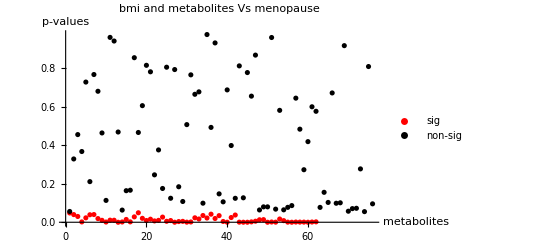

```mathematica
ListPlot[Tooltip[{dats,datns}],PlotLegends->{"sig","non-sig"},PlotStyle->{Red, Black},PlotRange->All,PlotLabel->"bmi and metabolites Vs menopause",
	AxesLabel->{"metabolites", "p-values"}]
```

```mathematica
sigdt=Transpose[databmimet2];
```

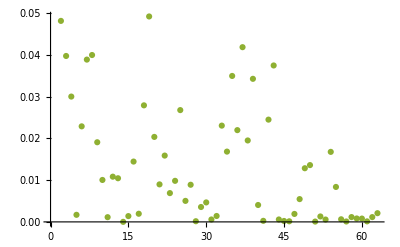

```mathematica
ListPlot[Tooltip[sigdt]]
```

Logistic regression of all the metabolites that showed significance when checked individually against bmi while keeping menopause as the response variable

```mathematica
bMimetLM=LogitModelFit[bC⟦2;;,{bMI,M13,M20,M21,M27,M30,M31,M35,M38,M41,M44,M45,M49,M57,M58,M59,M61,M68,M72,M87,M88,M89,M90,M91,M92,M93,M95,M96,M97,M98,M99,M100,M103,M104,M107,M108,M109,M110,M111,M113,M114,M115,M116,M117,M118,M119,M120,M121,M122,M123,M124,M125,M126,M127,M128,M129,M132,M133,M134,M135,M136,M137,M138,menopause}⟧,{1,x,xM13,xM20,xM21,xM27,xM30,xM31,xM35,xM38,xM41,xM44,xM45,xM49,xM57,xM58,xM59,xM61,xM68,xM72,xM87,xM88,xM89,xM90,xM91,xM92,xM93,xM95,xM96,xM97,xM98,xM99,xM100,xM103,xM104,xM107,xM108,xM109,xM110,xM111,xM113,xM114,xM115,xM116,xM117,xM118,xM119,xM120,xM121,xM122,xM123,xM124,xM125,xM126,xM127,xM128,xM129,xM132,xM133,xM134,xM135,xM136,xM137,xM138},
{x,xM13,xM20,xM21,xM27,xM30,xM31,xM35,xM38,xM41,xM44,xM45,xM49,xM57,xM58,xM59,xM61,xM68,xM72,xM87,xM88,xM89,xM90,xM91,xM92,xM93,xM95,xM96,xM97,xM98,xM99,xM100,xM103,xM104,xM107,xM108,xM109,xM110,xM111,xM113,xM114,xM115,xM116,xM117,xM118,xM119,xM120,xM121,xM122,xM123,xM124,xM125,xM126,xM127,xM128,xM129,xM132,xM133,xM134,xM135,xM136,xM137,xM138}]
bMimetLM["BestFit"]
bMimetLM["ParameterTable"]
bMimetLMent=bMimetLM["ParameterTableEntries"];
bMimetLMpos=Flatten[Position[bMimetLMent[[All,4]],_?(#<0.05&)]]
```

FittedModel[1/(1+ⅇ^(-4.57355+«97»))]

1/(1+ⅇ^(-4.57355+0.0875971 x+0.334643 xM100+0.0795534 xM103+0.0053033 xM104-0.130938 xM107+0.77092 xM108+0.339006 xM109-2.13163 xM110-0.0380171 xM111-1.64272 xM113+1.30435 xM114-0.118028 xM115-0.281853 xM116+1.68906 xM117-0.0757343 xM118+0.611133 xM119+0.414436 xM120-0.0131312 xM121+0.266429 xM122+0.367578 xM123+0.160285 xM124-0.292213 xM125-0.284854 xM126-0.0447329 xM127+0.169466 xM128-0.199302 xM129-0.969835 xM13-0.0388867 xM132+0.0526529 xM133-0.0957656 xM134-0.010702 xM135+0.141654 xM136+0.0662883 xM137-1.38493 xM138+0.00551153 xM20-0.0207159 xM21-0.0294935 xM27+0.0296585 xM30+0.00668024 xM31-0.00342557 xM35-0.0266437 xM38+0.45319 xM41+0.0385998 xM44-0.0104319 xM45-0.0259316 xM49+0.0911344 xM57-0.0207708 xM58+0.363687 xM59-0.00909144 xM61-0.0225363 xM68-0.0371625 xM72-0.042604 xM87+0.00984077 xM88-0.00338205 xM89+0.00567534 xM90-0.085599 xM91+0.138124 xM92+0.00945276 xM93-0.00593766 xM95+0.00181891 xM96-0.0157846 xM97-0.000266078 xM98-0.0760482 xM99))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 4.57355 | 2.02915 | 2.25392 | 0.0242013
x | -0.0875971 | 0.0573153 | -1.52834 | 0.126429
xM13 | 0.969835 | 0.797872 | 1.21553 | 0.224165
xM20 | -0.00551153 | 0.536538 | -0.0102724 | 0.991804
xM21 | 0.0207159 | 0.0253467 | 0.817301 | 0.413757
xM27 | 0.0294935 | 0.00734946 | 4.01302 | 0.0000599468
xM30 | -0.0296585 | 0.012195 | -2.43202 | 0.015015
xM31 | -0.00668024 | 0.0324389 | -0.205933 | 0.836843
xM35 | 0.00342557 | 0.0102099 | 0.335512 | 0.737239
xM38 | 0.0266437 | 0.0378711 | 0.703537 | 0.481721
xM41 | -0.45319 | 0.386221 | -1.17339 | 0.240638
xM44 | -0.0385998 | 0.0188846 | -2.04399 | 0.0409547
xM45 | 0.0104319 | 0.0414496 | 0.251677 | 0.801291
xM49 | 0.0259316 | 0.0248327 | 1.04425 | 0.296369
xM57 | -0.0911344 | 0.0585274 | -1.55712 | 0.119441
xM58 | 0.0207708 | 0.0890862 | 0.233153 | 0.815642
xM59 | -0.363687 | 0.562227 | -0.646868 | 0.517717
xM61 | 0.00909144 | 0.0310945 | 0.292381 | 0.769995
xM68 | 0.0225363 | 0.0936386 | 0.240673 | 0.809809
xM72 | 0.0371625 | 0.103914 | 0.357629 | 0.720621
xM87 | 0.042604 | 0.0811165 | 0.525221 | 0.59943
xM88 | -0.00984077 | 0.0911003 | -0.108021 | 0.913979
xM89 | 0.00338205 | 0.0227289 | 0.1488 | 0.881712
xM90 | -0.00567534 | 0.0095085 | -0.59687 | 0.550594
xM91 | 0.085599 | 0.168225 | 0.508835 | 0.610868
xM92 | -0.138124 | 0.463183 | -0.298207 | 0.765545
xM93 | -0.00945276 | 0.0208592 | -0.453169 | 0.650427
xM95 | 0.00593766 | 0.00782095 | 0.759199 | 0.447734
xM96 | -0.00181891 | 0.00281995 | -0.645016 | 0.518917
xM97 | 0.0157846 | 0.0249244 | 0.6333 | 0.526537
xM98 | 0.000266078 | 0.00319683 | 0.0832319 | 0.933667
xM99 | 0.0760482 | 0.325767 | 0.233444 | 0.815417
xM100 | -0.334643 | 0.603903 | -0.554134 | 0.579487
xM103 | -0.0795534 | 0.278932 | -0.285207 | 0.775485
xM104 | -0.0053033 | 0.00793176 | -0.668615 | 0.503741
xM107 | 0.130938 | 0.160582 | 0.815396 | 0.414846
xM108 | -0.77092 | 0.326747 | -2.35938 | 0.0183057
xM109 | -0.339006 | 0.673329 | -0.503477 | 0.614629
xM110 | 2.13163 | 0.949664 | 2.24461 | 0.024793
xM111 | 0.0380171 | 0.0959675 | 0.396146 | 0.691997
xM113 | 1.64272 | 0.701554 | 2.34154 | 0.0192044
xM114 | -1.30435 | 0.495672 | -2.63147 | 0.00850155
xM115 | 0.118028 | 0.0698476 | 1.68979 | 0.0910673
xM116 | 0.281853 | 0.162469 | 1.73481 | 0.0827747
xM117 | -1.68906 | 0.705728 | -2.39336 | 0.0166949
xM118 | 0.0757343 | 0.250773 | 0.302004 | 0.762649
xM119 | -0.611133 | 0.300719 | -2.03224 | 0.0421295
xM120 | -0.414436 | 2.97164 | -0.139464 | 0.889084
xM121 | 0.0131312 | 0.023726 | 0.553449 | 0.579956
xM122 | -0.266429 | 0.18486 | -1.44125 | 0.149514
xM123 | -0.367578 | 0.917027 | -0.400837 | 0.68854
xM124 | -0.160285 | 0.141868 | -1.12982 | 0.258554
xM125 | 0.292213 | 0.213007 | 1.37184 | 0.170112
xM126 | 0.284854 | 0.86866 | 0.327923 | 0.74297
xM127 | 0.0447329 | 0.0801343 | 0.558224 | 0.576691
xM128 | -0.169466 | 0.469561 | -0.360903 | 0.718172
xM129 | 0.199302 | 0.28284 | 0.704647 | 0.48103
xM132 | 0.0388867 | 0.0609227 | 0.638295 | 0.523282
xM133 | -0.0526529 | 0.0632015 | -0.833096 | 0.40479
xM134 | 0.0957656 | 0.369116 | 0.259446 | 0.795291
xM135 | 0.010702 | 0.074043 | 0.144538 | 0.885075
xM136 | -0.141654 | 0.141331 | -1.00229 | 0.316205
xM137 | -0.0662883 | 0.062355 | -1.06308 | 0.287746
xM138 | 1.38493 | 0.731892 | 1.89226 | 0.0584564

{1,6,7,12,37,39,41,42,45,47}

we build a logistic regression model of the metabolites we found significant while using menopause as response variable and keeping bmi as explanatory variable

```mathematica
bMimetLr1=LogitModelFit[bC⟦2;;,{bMI,M27,M30,M44,M108,M110,M113,M114,M117,M119,menopause}⟧,{1,x,xM27,xM30,xM44,xM108,xM110,xM113,xM114,xM117,xM119},{x,xM27,xM30,xM44,xM108,xM110,xM113,xM114,xM117,xM119}]
bMimetLr1["ParameterTable"]
bMimetLr1ent=bMimetLr1["ParameterTableEntries"];
bMimetLr1pos=Flatten[Position[bMimetLr1ent[[All,4]],_?(#<0.05&)]]
```

FittedModel[1/(1+ⅇ^(-4.92587+«14»+«21» xM44))]

| Estimate | Standard Error | z-Statistic | P-Value
1 | 4.92587 | 1.29654 | 3.79925 | 0.000145137
x | -0.0936369 | 0.0377176 | -2.48258 | 0.0130436
xM27 | 0.0249568 | 0.00481267 | 5.18564 | 2.15275×10^-7
xM30 | -0.0263516 | 0.00623696 | -4.22507 | 0.0000238864
xM44 | -0.0188685 | 0.00570033 | -3.31006 | 0.000932749
xM108 | 0.00978898 | 0.07108 | 0.137718 | 0.890463
xM110 | 0.662113 | 0.528326 | 1.25323 | 0.210123
xM113 | 0.729682 | 0.369895 | 1.97267 | 0.0485331
xM114 | -0.330133 | 0.239057 | -1.38098 | 0.167285
xM117 | -0.920742 | 0.328277 | -2.80477 | 0.0050353
xM119 | 0.0159832 | 0.0958176 | 0.166808 | 0.867521

{1,2,3,4,5,8,10}

```mathematica
bMimetLr2=LogitModelFit[bC⟦2;;,{bMI,M27,M30,M44,M113,M117,menopause}⟧,{1,x,xM27,xM30,xM44,xM113,xM117},{x,xM27,xM30,xM44,xM113,xM117}]
bMimetLr2["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-5.00501+«7»+«20» «4»))]

| Estimate | Standard Error | z-Statistic | P-Value
1 | 5.00501 | 1.26701 | 3.95026 | 0.0000780656
x | -0.0901677 | 0.0364449 | -2.47408 | 0.0133579
xM27 | 0.025136 | 0.00465719 | 5.39724 | 6.7672×10^-8
xM30 | -0.0257103 | 0.00585416 | -4.39181 | 0.0000112412
xM44 | -0.0206225 | 0.00549072 | -3.75588 | 0.000172731
xM113 | 0.867176 | 0.294171 | 2.94786 | 0.00319982
xM117 | -1.02295 | 0.290731 | -3.51854 | 0.000433923

```mathematica
meNmeT0=LogitModelFit[bC⟦2;;,{M1,menopause}⟧,xM1,
xM1]
meNmeT0["BestFit"]
meNmeT0["ParameterTable"]
meN0ent=meNmeT0["ParameterTableEntries"];
meN0pos=Flatten[Position[meN0ent[[All,4]],_?(#<0.05&)]]
```

FittedModel[1/(1+ⅇ^(0.632076-«19» xM1))]

1/(1+ⅇ^(0.632076-1.18954 xM1))

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.632076 | 0.622198 | -1.01588 | 0.309688
xM1 | 1.18954 | 0.756591 | 1.57224 | 0.115895

{}

```mathematica
meNmeT1=LogitModelFit[bC⟦2;;,{M1,M2,menopause}⟧,{1,xM1,xM2},
{xM1,xM2}]
meNmeT1["BestFit"]
meNmeT1["ParameterTable"]
meN1ent=meNmeT1["ParameterTableEntries"];
meN1pos=Flatten[Position[meN1ent[[All,4]],_?(#<0.05&)]]
```

FittedModel[1/(1+ⅇ^(-0.305258-«1»+«20» xM2))]

1/(1+ⅇ^(-0.305258-1.15524 xM1+0.0176713 xM2))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 0.305258 | 1.21092 | 0.252087 | 0.800974
xM1 | 1.15524 | 0.75767 | 1.52473 | 0.127326
xM2 | -0.0176713 | 0.0196047 | -0.901381 | 0.367386

{}

```mathematica
meNmeT2=LogitModelFit[bC⟦2;;,{M1,M2,M3,menopause}⟧,{1,xM1,xM2,xM3},
{xM1,xM2,xM3}]
meNmeT2["BestFit"]
meNmeT2["ParameterTable"]
meN2ent=meNmeT2["ParameterTableEntries"];
meN2pos=Flatten[Position[meN2ent[[All,4]],_?(#<0.05&)]]
```

FittedModel[1/(1+ⅇ^(«4»+«20» xM3))]

1/(1+ⅇ^(-0.426629-1.12444 xM1+0.0170027 xM2+0.0691113 xM3))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 0.426629 | 1.24027 | 0.34398 | 0.730861
xM1 | 1.12444 | 0.760435 | 1.47868 | 0.139227
xM2 | -0.0170027 | 0.0196693 | -0.864427 | 0.387353
xM3 | -0.0691113 | 0.152504 | -0.453177 | 0.650421

{}

```mathematica
meNmeT3=LogitModelFit[bC⟦2;;,{M1,M2,M3,M4,menopause}⟧,{1,xM1,xM2,xM3,xM4},
{xM1,xM2,xM3,xM4}]
meNmeT3["BestFit"]
meNmeT3["ParameterTable"]
meN3ent=meNmeT3["ParameterTableEntries"];
meN3pos=Flatten[Position[meN3ent[[All,4]],_?(#<0.05&)]]
```

FittedModel[1/(1+ⅇ^(«1»))]

1/(1+ⅇ^(-0.214626-1.07984 xM1+0.015659 xM2+0.173643 xM3-0.370468 xM4))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 0.214626 | 1.26267 | 0.169977 | 0.865028
xM1 | 1.07984 | 0.765764 | 1.41015 | 0.158495
xM2 | -0.015659 | 0.0197378 | -0.793353 | 0.427572
xM3 | -0.173643 | 0.177858 | -0.976297 | 0.328917
xM4 | 0.370468 | 0.322816 | 1.14761 | 0.251128

{}

```mathematica
meNmeT4=LogitModelFit[bC⟦2;;,{M1,M2,M3,M4,M5,menopause}⟧,{1,xM1,xM2,xM3,xM4,xM5},
{xM1,xM2,xM3,xM4,xM5}]
meNmeT4["BestFit"]
meNmeT4["ParameterTable"]
meN4ent=meNmeT4["ParameterTableEntries"];
meN4pos=Flatten[Position[meN4ent[[All,4]],_?(#<0.05&)]]
```

FittedModel[1/(1+ⅇ^(«1»))]

1/(1+ⅇ^(-0.168777-1.05407 xM1+0.0152926 xM2+0.24483 xM3-0.381524 xM4-0.0708948 xM5))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 0.168777 | 1.26396 | 0.13353 | 0.893774
xM1 | 1.05407 | 0.767671 | 1.37307 | 0.16973
xM2 | -0.0152926 | 0.0197347 | -0.77491 | 0.438393
xM3 | -0.24483 | 0.214805 | -1.13978 | 0.254379
xM4 | 0.381524 | 0.321786 | 1.18565 | 0.235762
xM5 | 0.0708948 | 0.120357 | 0.589037 | 0.555836

{}

```mathematica
meNmeT5=LogitModelFit[bC⟦2;;,{M1,M2,M3,M4,M5,M6,menopause}⟧,{1,xM1,xM2,xM3,xM4,xM5,xM6},
{xM1,xM2,xM3,xM4,xM5,xM6}]
meNmeT5["BestFit"]
meNmeT5["ParameterTable"]
meN5ent=meNmeT5["ParameterTableEntries"];
meN5pos=Flatten[Position[meN5ent[[All,4]],_?(#<0.05&)]]
```

FittedModel[1/(1+ⅇ^(«1»))]

1/(1+ⅇ^(-0.423196-1.0012 xM1+0.0185132 xM2+0.0252919 xM3-0.985256 xM4-0.114315 xM5+0.0379119 xM6))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 0.423196 | 1.29042 | 0.327952 | 0.742948
xM1 | 1.0012 | 0.775778 | 1.29058 | 0.196851
xM2 | -0.0185132 | 0.0201811 | -0.917351 | 0.358959
xM3 | -0.0252919 | 0.233448 | -0.10834 | 0.913726
xM4 | 0.985256 | 0.399886 | 2.46384 | 0.0137456
xM5 | 0.114315 | 0.124742 | 0.91641 | 0.359452
xM6 | -0.0379119 | 0.014727 | -2.57432 | 0.0100437

{5,7}

```mathematica
meNmeT6=LogitModelFit[bC⟦2;;,{M1,M2,M3,M4,M5,M6,M7,menopause}⟧,{1,xM1,xM2,xM3,xM4,xM5,xM6,xM7},
{xM1,xM2,xM3,xM4,xM5,xM6,xM7}]
meNmeT6["BestFit"]
meNmeT6["ParameterTable"]
meN6ent=meNmeT6["ParameterTableEntries"];
meN6pos=Flatten[Position[meN6ent[[All,4]],_?(#<0.05&)]]
```

FittedModel[1/(1+ⅇ^(«1»))]

1/(1+ⅇ^(-0.0310783-0.991792 xM1+0.015566 xM2+0.0462524 xM3-0.929565 xM4+0.0491012 xM5+0.0484381 xM6-0.0544683 xM7))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 0.0310783 | 1.31329 | 0.0236645 | 0.98112
xM1 | 0.991792 | 0.777178 | 1.27615 | 0.201904
xM2 | -0.015566 | 0.0202336 | -0.769317 | 0.441705
xM3 | -0.0462524 | 0.235939 | -0.196035 | 0.844582
xM4 | 0.929565 | 0.400173 | 2.32291 | 0.0201842
xM5 | -0.0491012 | 0.156114 | -0.314522 | 0.753124
xM6 | -0.0484381 | 0.0162514 | -2.98054 | 0.00287737
xM7 | 0.0544683 | 0.0311976 | 1.74591 | 0.0808261

{5,7}

```mathematica
meNmeT7=LogitModelFit[bC⟦2;;,{M1,M2,M3,M4,M5,M6,M7,M8,menopause}⟧,{1,xM1,xM2,xM3,xM4,xM5,xM6,xM7,xM8},
{xM1,xM2,xM3,xM4,xM5,xM6,xM7,xM8}]
meNmeT7["BestFit"]
meNmeT7["ParameterTable"]
meN7ent=meNmeT7["ParameterTableEntries"];
meN7pos=Flatten[Position[meN7ent[[All,4]],_?(#<0.05&)]]
```

FittedModel[1/(1+ⅇ^(«1»))]

1/(1+ⅇ^(0.206981-1.07547 xM1+0.0174586 xM2+0.0730815 xM3-1.00114 xM4+0.0178278 xM5+0.0490093 xM6-0.0380862 xM7-0.0172355 xM8))

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.206981 | 1.33158 | -0.15544 | 0.876474
xM1 | 1.07547 | 0.778315 | 1.38179 | 0.167037
xM2 | -0.0174586 | 0.0204431 | -0.85401 | 0.3931
xM3 | -0.0730815 | 0.240044 | -0.30445 | 0.760785
xM4 | 1.00114 | 0.406118 | 2.46515 | 0.0136955
xM5 | -0.0178278 | 0.158598 | -0.112409 | 0.910499
xM6 | -0.0490093 | 0.016355 | -2.99659 | 0.00273017
xM7 | 0.0380862 | 0.0330014 | 1.15408 | 0.248468
xM8 | 0.0172355 | 0.0121877 | 1.41417 | 0.157312

{5,7}

```mathematica
meNmeT8=LogitModelFit[bC⟦2;;,{M1,M2,M3,M4,M5,M6,M7,M8,M9,menopause}⟧,{1,xM1,xM2,xM3,xM4,xM5,xM6,xM7,xM8,xM9},
{xM1,xM2,xM3,xM4,xM5,xM6,xM7,xM8,xM9}]
meNmeT8["BestFit"]
meNmeT8["ParameterTable"]
meN8ent=meNmeT8["ParameterTableEntries"];
meN8pos=Flatten[Position[meN8ent[[All,4]],_?(#<0.05&)]]
```

FittedModel[1/(1+ⅇ^(«1»))]

1/(1+ⅇ^(0.225521-1.04804 xM1+0.0159991 xM2+0.0665851 xM3-1.0273 xM4+0.00590174 xM5+0.0477913 xM6-0.037392 xM7-0.0177532 xM8+0.00630602 xM9))

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.225521 | 1.33476 | -0.16896 | 0.865828
xM1 | 1.04804 | 0.785248 | 1.33466 | 0.181986
xM2 | -0.0159991 | 0.0208691 | -0.766642 | 0.443295
xM3 | -0.0665851 | 0.240915 | -0.276385 | 0.782253
xM4 | 1.0273 | 0.413174 | 2.48636 | 0.0129058
xM5 | -0.00590174 | 0.162018 | -0.0364263 | 0.970942
xM6 | -0.0477913 | 0.0167328 | -2.85614 | 0.00428829
xM7 | 0.037392 | 0.0331115 | 1.12928 | 0.258781
xM8 | 0.0177532 | 0.0123245 | 1.44048 | 0.149733
xM9 | -0.00630602 | 0.0180664 | -0.349047 | 0.727054

{5,7}

```mathematica
meNmeT9=LogitModelFit[bC⟦2;;,{M1,M2,M3,M4,M5,M6,M7,M8,M9,M10,menopause}⟧,{1,xM1,xM2,xM3,xM4,xM5,xM6,xM7,xM8,xM9,xM10},
{xM1,xM2,xM3,xM4,xM5,xM6,xM7,xM8,xM9,xM10}]
meNmeT9["BestFit"]
meNmeT9["ParameterTable"]
meN9ent=meNmeT9["ParameterTableEntries"];
meN9pos=Flatten[Position[meN9ent[[All,4]],_?(#<0.05&)]]
```

FittedModel[1/(1+ⅇ^(«14»+«22» xM9))]

1/(1+ⅇ^(0.844019-1.20735 xM1+0.179293 xM10+0.00756039 xM2+0.000295048 xM3-1.12392 xM4+0.00471897 xM5+0.0153724 xM6-0.0295428 xM7-0.0176234 xM8+0.00118544 xM9))

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.844019 | 1.4201 | -0.594337 | 0.552287
xM1 | 1.20735 | 0.79954 | 1.51006 | 0.131029
xM2 | -0.00756039 | 0.021753 | -0.347556 | 0.728174
xM3 | -0.000295048 | 0.246189 | -0.00119846 | 0.999044
xM4 | 1.12392 | 0.426673 | 2.63415 | 0.00843481
xM5 | -0.00471897 | 0.164165 | -0.0287452 | 0.977068
xM6 | -0.0153724 | 0.0267952 | -0.573701 | 0.56617
xM7 | 0.0295428 | 0.0334891 | 0.882161 | 0.37769
xM8 | 0.0176234 | 0.012273 | 1.43595 | 0.151016
xM9 | -0.00118544 | 0.0184863 | -0.0641254 | 0.94887
xM10 | -0.179293 | 0.116728 | -1.53598 | 0.124542

{5}

```mathematica
meNmeT10=LogitModelFit[bC⟦2;;,{M1,M2,M3,M4,M5,M6,M7,M8,M9,M10,M11,menopause}⟧,{1,xM1,xM2,xM3,xM4,xM5,xM6,xM7,xM8,xM9,xM10,xM11},
{xM1,xM2,xM3,xM4,xM5,xM6,xM7,xM8,xM9,xM10,xM11}]
meNmeT10["BestFit"]
meNmeT10["ParameterTable"]
meN10ent=meNmeT10["ParameterTableEntries"];
meN10pos=Flatten[Position[meN10ent[[All,4]],_?(#<0.05&)]]
```

FittedModel[1/(1+ⅇ^(«15»+«22» xM9))]

1/(1+ⅇ^(1.19564-1.23646 xM1+0.164556 xM10+0.220854 xM11+0.00166702 xM2+0.0292889 xM3-1.14818 xM4+0.00993592 xM5+0.0189396 xM6-0.0857487 xM7-0.0170831 xM8+0.00057081 xM9))

| Estimate | Standard Error | z-Statistic | P-Value
1 | -1.19564 | 1.51302 | -0.790233 | 0.429392
xM1 | 1.23646 | 0.802039 | 1.54165 | 0.12316
xM2 | -0.00166702 | 0.0233915 | -0.071266 | 0.943186
xM3 | -0.0292889 | 0.250574 | -0.116887 | 0.906949
xM4 | 1.14818 | 0.429155 | 2.67544 | 0.00746318
xM5 | -0.00993592 | 0.163862 | -0.060636 | 0.951649
xM6 | -0.0189396 | 0.0274983 | -0.688758 | 0.490976
xM7 | 0.0857487 | 0.0867066 | 0.988953 | 0.322686
xM8 | 0.0170831 | 0.0123227 | 1.38631 | 0.165652
xM9 | -0.00057081 | 0.0185159 | -0.0308281 | 0.975407
xM10 | -0.164556 | 0.119317 | -1.37914 | 0.167851
xM11 | -0.220854 | 0.313341 | -0.704834 | 0.480913

{5}

```mathematica
meNmeT11=LogitModelFit[bC⟦2;;,{M1,M2,M3,M4,M5,M6,M7,M8,M9,M10,M11,M12,menopause}⟧,{1,xM1,xM2,xM3,xM4,xM5,xM6,xM7,xM8,xM9,xM10,xM11,xM12},
{xM1,xM2,xM3,xM4,xM5,xM6,xM7,xM8,xM9,xM10,xM11,xM12}]
meNmeT11["BestFit"]
meNmeT11["ParameterTable"]
meN11ent=meNmeT11["ParameterTableEntries"];
meN11pos=Flatten[Position[meN11ent[[All,4]],_?(#<0.05&)]]
```

FittedModel[1/(1+ⅇ^(«17»+«22» xM9))]

1/(1+ⅇ^(1.13221-1.24475 xM1+0.154737 xM10+0.209733 xM11+0.0477677 xM12+0.00162436 xM2+0.0558981 xM3-1.18205 xM4-0.0122569 xM5+0.0194713 xM6-0.0903221 xM7-0.0178049 xM8+0.0010116 xM9))

| Estimate | Standard Error | z-Statistic | P-Value
1 | -1.13221 | 1.50963 | -0.749993 | 0.453259
xM1 | 1.24475 | 0.804071 | 1.54806 | 0.121608
xM2 | -0.00162436 | 0.0233375 | -0.0696028 | 0.94451
xM3 | -0.0558981 | 0.254353 | -0.219766 | 0.826054
xM4 | 1.18205 | 0.433044 | 2.72962 | 0.00634073
xM5 | 0.0122569 | 0.168094 | 0.0729172 | 0.941872
xM6 | -0.0194713 | 0.0272726 | -0.713951 | 0.475258
xM7 | 0.0903221 | 0.0869872 | 1.03834 | 0.299113
xM8 | 0.0178049 | 0.0123428 | 1.44253 | 0.149154
xM9 | -0.0010116 | 0.018534 | -0.0545809 | 0.956472
xM10 | -0.154737 | 0.119026 | -1.30003 | 0.193591
xM11 | -0.209733 | 0.314194 | -0.667527 | 0.504435
xM12 | -0.0477677 | 0.079818 | -0.598457 | 0.549535

{5}

```mathematica
meNmeT12=LogitModelFit[bC⟦2;;,{M1,M2,M3,M4,M5,M6,M7,M8,M9,M10,M11,M12,M13,menopause}⟧,{1,xM1,xM2,xM3,xM4,xM5,xM6,xM7,xM8,xM9,xM10,xM11,xM12,xM13},
{xM1,xM2,xM3,xM4,xM5,xM6,xM7,xM8,xM9,xM10,xM11,xM12,xM13}]
meNmeT12["BestFit"]
meNmeT12["ParameterTable"]
meN12ent=meNmeT12["ParameterTableEntries"];
meN12pos=Flatten[Position[meN12ent[[All,4]],_?(#<0.05&)]]
```

FittedModel[1/(1+ⅇ^(«19»+«21» xM9))]

1/(1+ⅇ^(1.42342-1.08306 xM1+0.143634 xM10+0.305818 xM11+0.100502 xM12-2.73008 xM13+0.000498993 xM2+0.129468 xM3-0.24316 xM4-0.0375573 xM5+0.0510147 xM6-0.111661 xM7-0.0229615 xM8+0.00461489 xM9))

| Estimate | Standard Error | z-Statistic | P-Value
1 | -1.42342 | 1.56026 | -0.912292 | 0.361615
xM1 | 1.08306 | 0.820883 | 1.31939 | 0.187039
xM2 | -0.000498993 | 0.0242539 | -0.0205737 | 0.983586
xM3 | -0.129468 | 0.26098 | -0.496085 | 0.619834
xM4 | 0.24316 | 0.490779 | 0.495456 | 0.620278
xM5 | 0.0375573 | 0.173432 | 0.216554 | 0.828556
xM6 | -0.0510147 | 0.0304739 | -1.67404 | 0.0941222
xM7 | 0.111661 | 0.0894182 | 1.24876 | 0.211755
xM8 | 0.0229615 | 0.0128688 | 1.78427 | 0.0743793
xM9 | -0.00461489 | 0.0196276 | -0.235122 | 0.814114
xM10 | -0.143634 | 0.125824 | -1.14154 | 0.253643
xM11 | -0.305818 | 0.32799 | -0.932399 | 0.35113
xM12 | -0.100502 | 0.0858853 | -1.17019 | 0.241925
xM13 | 2.73008 | 0.711432 | 3.83745 | 0.000124318

{14}

```mathematica
meNmeT13=LogitModelFit[bC⟦2;;,{M1,M2,M3,M4,M5,M6,M7,M8,M9,M10,M11,M12,M13,M14,menopause}⟧,{1,xM1,xM2,xM3,xM4,xM5,xM6,xM7,xM8,xM9,xM10,xM11,xM12,xM13,xM14},
{xM1,xM2,xM3,xM4,xM5,xM6,xM7,xM8,xM9,xM10,xM11,xM12,xM13,xM14}]
meNmeT13["BestFit"]
meNmeT13["ParameterTable"]
meN13ent=meNmeT13["ParameterTableEntries"];
meN13pos=Flatten[Position[meN13ent[[All,4]],_?(#<0.05&)]]
```

FittedModel[1/(1+ⅇ^(«1»))]

1/(1+ⅇ^(1.43637-1.12468 xM1+0.141267 xM10+0.320736 xM11+0.0994474 xM12-2.81783 xM13+0.179794 xM14-0.0000624885 xM2+0.0962596 xM3-0.341174 xM4-0.0642219 xM5+0.0461904 xM6-0.111985 xM7-0.0262133 xM8-0.0139536 xM9))

| Estimate | Standard Error | z-Statistic | P-Value
1 | -1.43637 | 1.56444 | -0.918132 | 0.35855
xM1 | 1.12468 | 0.818993 | 1.37324 | 0.169676
xM2 | 0.0000624885 | 0.0243497 | 0.00256629 | 0.997952
xM3 | -0.0962596 | 0.264331 | -0.364163 | 0.715736
xM4 | 0.341174 | 0.50213 | 0.679454 | 0.49685
xM5 | 0.0642219 | 0.177216 | 0.362394 | 0.717057
xM6 | -0.0461904 | 0.0301186 | -1.53362 | 0.125124
xM7 | 0.111985 | 0.0898774 | 1.24597 | 0.212775
xM8 | 0.0262133 | 0.0131824 | 1.9885 | 0.0467561
xM9 | 0.0139536 | 0.0260402 | 0.535848 | 0.592063
xM10 | -0.141267 | 0.123036 | -1.14817 | 0.250897
xM11 | -0.320736 | 0.330787 | -0.969615 | 0.332238
xM12 | -0.0994474 | 0.0856518 | -1.16107 | 0.245615
xM13 | 2.81783 | 0.720907 | 3.90873 | 0.0000927829
xM14 | -0.179794 | 0.16992 | -1.05811 | 0.290007

{9,14}

```mathematica
meNmeT14=LogitModelFit[bC⟦2;;,{M1,M2,M3,M4,M5,M6,M7,M8,M9,M10,M11,M12,M13,M14,menopause}⟧,{1,xM1,xM2,xM3,xM4,xM5,xM6,xM7,xM8,xM9,xM10,xM11,xM12,xM13,xM14},
{xM1,xM2,xM3,xM4,xM5,xM6,xM7,xM8,xM9,xM10,xM11,xM12,xM13,xM14}]
meNmeT14["BestFit"]
meNmeT14["ParameterTable"]
meN14ent=meNmeT14["ParameterTableEntries"];
meN14pos=Flatten[Position[meN14ent[[All,4]],_?(#<0.05&)]]
```

FittedModel[1/(1+ⅇ^(«1»))]

1/(1+ⅇ^(1.43637-1.12468 xM1+0.141267 xM10+0.320736 xM11+0.0994474 xM12-2.81783 xM13+0.179794 xM14-0.0000624885 xM2+0.0962596 xM3-0.341174 xM4-0.0642219 xM5+0.0461904 xM6-0.111985 xM7-0.0262133 xM8-0.0139536 xM9))

| Estimate | Standard Error | z-Statistic | P-Value
1 | -1.43637 | 1.56444 | -0.918132 | 0.35855
xM1 | 1.12468 | 0.818993 | 1.37324 | 0.169676
xM2 | 0.0000624885 | 0.0243497 | 0.00256629 | 0.997952
xM3 | -0.0962596 | 0.264331 | -0.364163 | 0.715736
xM4 | 0.341174 | 0.50213 | 0.679454 | 0.49685
xM5 | 0.0642219 | 0.177216 | 0.362394 | 0.717057
xM6 | -0.0461904 | 0.0301186 | -1.53362 | 0.125124
xM7 | 0.111985 | 0.0898774 | 1.24597 | 0.212775
xM8 | 0.0262133 | 0.0131824 | 1.9885 | 0.0467561
xM9 | 0.0139536 | 0.0260402 | 0.535848 | 0.592063
xM10 | -0.141267 | 0.123036 | -1.14817 | 0.250897
xM11 | -0.320736 | 0.330787 | -0.969615 | 0.332238
xM12 | -0.0994474 | 0.0856518 | -1.16107 | 0.245615
xM13 | 2.81783 | 0.720907 | 3.90873 | 0.0000927829
xM14 | -0.179794 | 0.16992 | -1.05811 | 0.290007

{9,14}

```mathematica
meNmeT16=LogitModelFit[bC⟦2;;,{M1,M2,M3,M4,M5,M6,M7,M8,M9,M10,M11,M12,M13,M14,M15,menopause}⟧,{1,xM1,xM2,xM3,xM4,xM5,xM6,xM7,xM8,xM9,xM10,xM11,xM12,xM13,xM14,xM15},
{xM1,xM2,xM3,xM4,xM5,xM6,xM7,xM8,xM9,xM10,xM11,xM12,xM13,xM14,xM15}]
meNmeT16["BestFit"]
meNmeT16["ParameterTable"]
meN16ent=meNmeT16["ParameterTableEntries"];
meN16pos=Flatten[Position[meN16ent[[All,4]],_?(#<0.05&)]]
```

FittedModel[1/(1+ⅇ^(«1»))]

1/(1+ⅇ^(0.650364-1.49473 xM1+0.198299 xM10+0.328537 xM11+0.114896 xM12-2.70573 xM13+0.15982 xM14+0.338391 xM15+0.0070376 xM2-0.347291 xM3-0.199394 xM4-0.136506 xM5+0.0443811 xM6-0.10952 xM7-0.031662 xM8-0.0105386 xM9))

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.650364 | 1.62581 | -0.400024 | 0.689139
xM1 | 1.49473 | 0.842508 | 1.77414 | 0.0760402
xM2 | -0.0070376 | 0.0249494 | -0.282075 | 0.777886
xM3 | 0.347291 | 0.323871 | 1.07231 | 0.28358
xM4 | 0.199394 | 0.511586 | 0.389757 | 0.696716
xM5 | 0.136506 | 0.18684 | 0.730606 | 0.46502
xM6 | -0.0443811 | 0.0300709 | -1.47588 | 0.139975
xM7 | 0.10952 | 0.0904504 | 1.21083 | 0.225959
xM8 | 0.031662 | 0.0134789 | 2.34901 | 0.0188233
xM9 | 0.0105386 | 0.0257568 | 0.409158 | 0.682424
xM10 | -0.198299 | 0.126457 | -1.56812 | 0.116854
xM11 | -0.328537 | 0.333747 | -0.984389 | 0.324924
xM12 | -0.114896 | 0.0865486 | -1.32754 | 0.184331
xM13 | 2.70573 | 0.73342 | 3.68919 | 0.000224966
xM14 | -0.15982 | 0.169872 | -0.940831 | 0.346792
xM15 | -0.338391 | 0.141269 | -2.39538 | 0.0166033

{9,14,16}

```mathematica
meNmeT17=LogitModelFit[bC⟦2;;,{M1,M2,M3,M4,M5,M6,M7,M8,M9,M10,M11,M12,M13,M14,M15,M16,menopause}⟧,{1,xM1,xM2,xM3,xM4,xM5,xM6,xM7,xM8,xM9,xM10,xM11,xM12,xM13,xM14,xM15,xM16},
{xM1,xM2,xM3,xM4,xM5,xM6,xM7,xM8,xM9,xM10,xM11,xM12,xM13,xM14,xM15,xM16}]
meNmeT17["BestFit"]
meNmeT17["ParameterTable"]
meN17ent=meNmeT17["ParameterTableEntries"];
meN17pos=Flatten[Position[meN17ent[[All,4]],_?(#<0.05&)]]
```

FittedModel[1/(1+ⅇ^(«1»))]

1/(1+ⅇ^(0.114591-1.82553 xM1+0.220632 xM10+0.435645 xM11+0.0705029 xM12-3.0077 xM13+0.158882 xM14+0.136823 xM15+0.13569 xM16+0.00409488 xM2-0.126417 xM3-0.194259 xM4-0.114499 xM5+0.0397389 xM6-0.143393 xM7-0.0271666 xM8-0.0115299 xM9))

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.114591 | 1.65675 | -0.0691658 | 0.944858
xM1 | 1.82553 | 0.866219 | 2.10747 | 0.0350772
xM2 | -0.00409488 | 0.0251647 | -0.162723 | 0.870736
xM3 | 0.126417 | 0.342198 | 0.369428 | 0.711809
xM4 | 0.194259 | 0.515927 | 0.376524 | 0.706527
xM5 | 0.114499 | 0.186088 | 0.615295 | 0.53836
xM6 | -0.0397389 | 0.0301535 | -1.31789 | 0.187541
xM7 | 0.143393 | 0.092524 | 1.5498 | 0.121191
xM8 | 0.0271666 | 0.0137986 | 1.96879 | 0.0489774
xM9 | 0.0115299 | 0.0260367 | 0.442833 | 0.657886
xM10 | -0.220632 | 0.128162 | -1.72152 | 0.0851574
xM11 | -0.435645 | 0.338566 | -1.28674 | 0.198186
xM12 | -0.0705029 | 0.0893526 | -0.789041 | 0.430088
xM13 | 3.0077 | 0.757075 | 3.97279 | 0.0000710347
xM14 | -0.158882 | 0.171575 | -0.92602 | 0.354436
xM15 | -0.136823 | 0.170725 | -0.801424 | 0.422886
xM16 | -0.13569 | 0.0650522 | -2.08587 | 0.0369907

{2,9,14,17}

```mathematica
meNmeT18=LogitModelFit[bC⟦2;;,{M1,M2,M3,M4,M5,M6,M7,M8,M9,M10,M11,M12,M13,M14,M15,M16,M17,menopause}⟧,{1,xM1,xM2,xM3,xM4,xM5,xM6,xM7,xM8,xM9,xM10,xM11,xM12,xM13,xM14,xM15,xM16,xM17},
{xM1,xM2,xM3,xM4,xM5,xM6,xM7,xM8,xM9,xM10,xM11,xM12,xM13,xM14,xM15,xM16,xM17}]
meNmeT18["BestFit"]
meNmeT18["ParameterTable"]
meN18ent=meNmeT18["ParameterTableEntries"];
meN18pos=Flatten[Position[meN18ent[[All,4]],_?(#<0.05&)]]
```

FittedModel[1/(1+ⅇ^(«1»))]

1/(1+ⅇ^(0.105687-1.63283 xM1+0.230474 xM10+0.492822 xM11+0.0452883 xM12-3.03133 xM13+0.116183 xM14+0.11557 xM15+0.228771 xM16-0.689061 xM17+0.00807898 xM2-0.251341 xM3+0.181659 xM4-0.106479 xM5+0.0390189 xM6-0.149534 xM7-0.0251103 xM8-0.0147592 xM9))

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.105687 | 1.69582 | -0.0623221 | 0.950306
xM1 | 1.63283 | 0.886346 | 1.84221 | 0.0654447
xM2 | -0.00807898 | 0.0260183 | -0.310512 | 0.756172
xM3 | 0.251341 | 0.352804 | 0.71241 | 0.476211
xM4 | -0.181659 | 0.54611 | -0.332642 | 0.739405
xM5 | 0.106479 | 0.186307 | 0.571525 | 0.567644
xM6 | -0.0390189 | 0.0299735 | -1.30178 | 0.192992
xM7 | 0.149534 | 0.0928288 | 1.61086 | 0.107211
xM8 | 0.0251103 | 0.0140954 | 1.78145 | 0.0748387
xM9 | 0.0147592 | 0.0265876 | 0.555115 | 0.578816
xM10 | -0.230474 | 0.126556 | -1.82112 | 0.0685886
xM11 | -0.492822 | 0.34263 | -1.43835 | 0.150335
xM12 | -0.0452883 | 0.0909859 | -0.49775 | 0.61866
xM13 | 3.03133 | 0.765803 | 3.95836 | 0.0000754653
xM14 | -0.116183 | 0.173985 | -0.667779 | 0.504275
xM15 | -0.11557 | 0.175858 | -0.657176 | 0.511068
xM16 | -0.228771 | 0.0777692 | -2.94167 | 0.00326448
xM17 | 0.689061 | 0.296971 | 2.32029 | 0.0203249

{14,17,18}

```mathematica
meNmeT19=LogitModelFit[bC⟦2;;,{M1,M2,M3,M4,M5,M6,M7,M8,M9,M10,M11,M12,M13,M14,M15,M16,M17,M18,menopause}⟧,{1,xM1,xM2,xM3,xM4,xM5,xM6,xM7,xM8,xM9,xM10,xM11,xM12,xM13,xM14,xM15,xM16,xM17,xM18},
{xM1,xM2,xM3,xM4,xM5,xM6,xM7,xM8,xM9,xM10,xM11,xM12,xM13,xM14,xM15,xM16,xM17,xM18}]
meNmeT19["BestFit"]
meNmeT19["ParameterTable"]
meN19ent=meNmeT19["ParameterTableEntries"];
meN19pos=Flatten[Position[meN19ent[[All,4]],_?(#<0.05&)]]
```

FittedModel[1/(1+ⅇ^(«1»))]

1/(1+ⅇ^(0.031934-1.55283 xM1+0.233946 xM10+0.496272 xM11+0.0372923 xM12-3.13857 xM13+0.12531 xM14+0.186068 xM15+0.235421 xM16-0.695318 xM17-0.0262347 xM18+0.00824827 xM2-0.307113 xM3+0.189207 xM4+0.0311614 xM5+0.0368013 xM6-0.146863 xM7-0.0279139 xM8-0.0141872 xM9))

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.031934 | 1.70158 | -0.0187672 | 0.985027
xM1 | 1.55283 | 0.895207 | 1.73461 | 0.0828107
xM2 | -0.00824827 | 0.0260079 | -0.317145 | 0.751134
xM3 | 0.307113 | 0.36158 | 0.849363 | 0.395679
xM4 | -0.189207 | 0.546934 | -0.345942 | 0.729387
xM5 | -0.0311614 | 0.270806 | -0.115069 | 0.90839
xM6 | -0.0368013 | 0.0301584 | -1.22027 | 0.222364
xM7 | 0.146863 | 0.0928035 | 1.58252 | 0.113532
xM8 | 0.0279139 | 0.0147067 | 1.89804 | 0.0576909
xM9 | 0.0141872 | 0.0266194 | 0.532963 | 0.594059
xM10 | -0.233946 | 0.127164 | -1.83971 | 0.0658108
xM11 | -0.496272 | 0.342968 | -1.44699 | 0.1479
xM12 | -0.0372923 | 0.0918526 | -0.406002 | 0.684741
xM13 | 3.13857 | 0.788864 | 3.97859 | 0.0000693242
xM14 | -0.12531 | 0.174838 | -0.716717 | 0.473549
xM15 | -0.186068 | 0.202282 | -0.919843 | 0.357655
xM16 | -0.235421 | 0.0784485 | -3.00097 | 0.00269125
xM17 | 0.695318 | 0.298139 | 2.3322 | 0.0196904
xM18 | 0.0262347 | 0.0373209 | 0.702949 | 0.482087

{14,17,18}

```mathematica
meNmeT20=LogitModelFit[bC⟦2;;,{M1,M2,M3,M4,M5,M6,M7,M8,M9,M10,M11,M12,M13,M14,M15,M16,M17,M18,M19,menopause}⟧,{1,xM1,xM2,xM3,xM4,xM5,xM6,xM7,xM8,xM9,xM10,xM11,xM12,xM13,xM14,xM15,xM16,xM17,xM18,xM19},
{xM1,xM2,xM3,xM4,xM5,xM6,xM7,xM8,xM9,xM10,xM11,xM12,xM13,xM14,xM15,xM16,xM17,xM18,xM19}]
meNmeT20["BestFit"]
meNmeT20["ParameterTable"]
meN20ent=meNmeT20["ParameterTableEntries"];
meN20pos=Flatten[Position[meN20ent[[All,4]],_?(#<0.05&)]]
```

FittedModel[1/(1+ⅇ^(«1»))]

1/(1+ⅇ^(0.195095-1.45167 xM1+0.231527 xM10+0.490289 xM11+0.0351283 xM12-2.93754 xM13+0.0950707 xM14+0.229178 xM15+0.242966 xM16-0.646122 xM17-0.0250066 xM18-0.225687 xM19+0.00855517 xM2-0.161852 xM3+0.00901303 xM4+0.0565478 xM5+0.0381933 xM6-0.15562 xM7-0.0240612 xM8-0.0158233 xM9))

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.195095 | 1.71484 | -0.113769 | 0.909421
xM1 | 1.45167 | 0.902512 | 1.60848 | 0.10773
xM2 | -0.00855517 | 0.0260515 | -0.328394 | 0.742614
xM3 | 0.161852 | 0.385185 | 0.420194 | 0.674344
xM4 | -0.00901303 | 0.569902 | -0.0158151 | 0.987382
xM5 | -0.0565478 | 0.275134 | -0.205529 | 0.837159
xM6 | -0.0381933 | 0.030771 | -1.24121 | 0.214529
xM7 | 0.15562 | 0.0939027 | 1.65725 | 0.0974692
xM8 | 0.0240612 | 0.0151141 | 1.59197 | 0.111391
xM9 | 0.0158233 | 0.02702 | 0.585614 | 0.558135
xM10 | -0.231527 | 0.129804 | -1.78367 | 0.0744765
xM11 | -0.490289 | 0.344367 | -1.42374 | 0.154522
xM12 | -0.0351283 | 0.092185 | -0.381063 | 0.703156
xM13 | 2.93754 | 0.805811 | 3.64544 | 0.000266933
xM14 | -0.0950707 | 0.177612 | -0.535272 | 0.592462
xM15 | -0.229178 | 0.206435 | -1.11017 | 0.266924
xM16 | -0.242966 | 0.0792661 | -3.06519 | 0.00217529
xM17 | 0.646122 | 0.300659 | 2.14902 | 0.031633
xM18 | 0.0250066 | 0.0374355 | 0.667993 | 0.504138
xM19 | 0.225687 | 0.186766 | 1.2084 | 0.226894

{14,17,18}

```mathematica
meNmeT21=LogitModelFit[bC⟦2;;,{M1,M2,M3,M4,M5,M6,M7,M8,M9,M10,M11,M12,M13,M14,M15,M16,M17,M18,M19,M20,menopause}⟧,{1,xM1,xM2,xM3,xM4,xM5,xM6,xM7,xM8,xM9,xM10,xM11,xM12,xM13,xM14,xM15,xM16,xM17,xM18,xM19,xM20},
{xM1,xM2,xM3,xM4,xM5,xM6,xM7,xM8,xM9,xM10,xM11,xM12,xM13,xM14,xM15,xM16,xM17,xM18,xM19,xM20}]
meNmeT21["BestFit"]
meNmeT21["ParameterTable"]
meN21ent=meNmeT21["ParameterTableEntries"];
meN21pos=Flatten[Position[meN21ent[[All,4]],_?(#<0.05&)]]
```

FittedModel[1/(1+ⅇ^(«1»))]

1/(1+ⅇ^(0.431838-1.50059 xM1+0.192014 xM10+0.541068 xM11+0.0442723 xM12-3.16563 xM13+0.0427359 xM14+0.199001 xM15+0.205769 xM16-0.718268 xM17-0.0302001 xM18-0.231355 xM19-0.00273291 xM2+0.484257 xM20+0.0043905 xM3+0.23968 xM4+0.081308 xM5+0.0358847 xM6-0.159712 xM7-0.0263794 xM8-0.0110127 xM9))

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.431838 | 1.73436 | -0.24899 | 0.803369
xM1 | 1.50059 | 0.912044 | 1.64531 | 0.0999067
xM2 | 0.00273291 | 0.0268561 | 0.101761 | 0.918946
xM3 | -0.0043905 | 0.396135 | -0.0110833 | 0.991157
xM4 | -0.23968 | 0.590196 | -0.406102 | 0.684668
xM5 | -0.081308 | 0.274865 | -0.29581 | 0.767375
xM6 | -0.0358847 | 0.0300847 | -1.19279 | 0.232951
xM7 | 0.159712 | 0.0935351 | 1.70751 | 0.0877277
xM8 | 0.0263794 | 0.0153355 | 1.72015 | 0.0854056
xM9 | 0.0110127 | 0.0278533 | 0.395382 | 0.692561
xM10 | -0.192014 | 0.128665 | -1.49236 | 0.135604
xM11 | -0.541068 | 0.344634 | -1.56998 | 0.11642
xM12 | -0.0442723 | 0.0927429 | -0.477365 | 0.633102
xM13 | 3.16563 | 0.828565 | 3.82062 | 0.000133116
xM14 | -0.0427359 | 0.182107 | -0.234675 | 0.814461
xM15 | -0.199001 | 0.209396 | -0.950357 | 0.341931
xM16 | -0.205769 | 0.0817595 | -2.51676 | 0.011844
xM17 | 0.718268 | 0.308077 | 2.33146 | 0.0197293
xM18 | 0.0302001 | 0.0375568 | 0.804119 | 0.421328
xM19 | 0.231355 | 0.187971 | 1.2308 | 0.218396
xM20 | -0.484257 | 0.256813 | -1.88564 | 0.0593438

{14,17,18}

```mathematica
meNmeT22=LogitModelFit[bC⟦2;;,{M1,M2,M3,M4,M5,M6,M7,M8,M9,M10,M11,M12,M13,M14,M15,M16,M17,M18,M19,M20,M21,menopause}⟧,{1,xM1,xM2,xM3,xM4,xM5,xM6,xM7,xM8,xM9,xM10,xM11,xM12,xM13,xM14,xM15,xM16,xM17,xM18,xM19,xM20,xM21},
{xM1,xM2,xM3,xM4,xM5,xM6,xM7,xM8,xM9,xM10,xM11,xM12,xM13,xM14,xM15,xM16,xM17,xM18,xM19,xM20,xM21}]
meNmeT22["BestFit"]
meNmeT22["ParameterTable"]
meN22ent=meNmeT22["ParameterTableEntries"];
meN22pos=Flatten[Position[meN22ent[[All,4]],_?(#<0.05&)]]
```

FittedModel[1/(1+ⅇ^(«1»))]

1/(1+ⅇ^(0.0920593-1.22685 xM1+0.19307 xM10+0.486462 xM11+0.0451184 xM12-3.11862 xM13+0.0582634 xM14+0.0933443 xM15+0.205689 xM16-0.749941 xM17-0.0360567 xM18-0.240015 xM19-0.00427132 xM2+0.478453 xM20+0.01147 xM21+0.0401412 xM3+0.236821 xM4+0.100122 xM5+0.0399875 xM6-0.162149 xM7-0.024116 xM8-0.0182523 xM9))

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.0920593 | 1.76739 | -0.0520878 | 0.958459
xM1 | 1.22685 | 0.934769 | 1.31247 | 0.189363
xM2 | 0.00427132 | 0.0271548 | 0.157296 | 0.875012
xM3 | -0.0401412 | 0.400238 | -0.100293 | 0.920111
xM4 | -0.236821 | 0.592292 | -0.399838 | 0.689276
xM5 | -0.100122 | 0.277091 | -0.361332 | 0.717851
xM6 | -0.0399875 | 0.0306488 | -1.3047 | 0.191995
xM7 | 0.162149 | 0.0935735 | 1.73285 | 0.0831229
xM8 | 0.024116 | 0.015429 | 1.56303 | 0.118045
xM9 | 0.0182523 | 0.028279 | 0.645437 | 0.518644
xM10 | -0.19307 | 0.129539 | -1.49043 | 0.13611
xM11 | -0.486462 | 0.348741 | -1.39491 | 0.163043
xM12 | -0.0451184 | 0.0933484 | -0.483333 | 0.628859
xM13 | 3.11862 | 0.835171 | 3.73411 | 0.00018838
xM14 | -0.0582634 | 0.1827 | -0.318902 | 0.749801
xM15 | -0.0933443 | 0.226895 | -0.411399 | 0.68078
xM16 | -0.205689 | 0.0826088 | -2.48992 | 0.0127771
xM17 | 0.749941 | 0.309919 | 2.41979 | 0.0155293
xM18 | 0.0360567 | 0.0383015 | 0.941391 | 0.346505
xM19 | 0.240015 | 0.189724 | 1.26507 | 0.205845
xM20 | -0.478453 | 0.259945 | -1.84059 | 0.0656814
xM21 | -0.01147 | 0.00906383 | -1.26547 | 0.205704

{14,17,18}

```mathematica
meNmeT23=LogitModelFit[bC⟦2;;,{M1,M2,M3,M4,M5,M6,M7,M8,M9,M10,M11,M12,M13,M14,M15,M16,M17,M18,M19,M20,M21,M22,menopause}⟧,{1,xM1,xM2,xM3,xM4,xM5,xM6,xM7,xM8,xM9,xM10,xM11,xM12,xM13,xM14,xM15,xM16,xM17,xM18,xM19,xM20,xM21,xM22},
{xM1,xM2,xM3,xM4,xM5,xM6,xM7,xM8,xM9,xM10,xM11,xM12,xM13,xM14,xM15,xM16,xM17,xM18,xM19,xM20,xM21,xM22}]
meNmeT23["BestFit"]
meNmeT23["ParameterTable"]
meN23ent=meNmeT23["ParameterTableEntries"];
meN23pos=Flatten[Position[meN23ent[[All,4]],_?(#<0.05&)]]
```

FittedModel[1/(1+ⅇ^(«1»))]

1/(1+ⅇ^(-0.00748713-1.26396 xM1+0.204367 xM10+0.466194 xM11+0.0410234 xM12-3.17279 xM13+0.0688183 xM14+0.066151 xM15+0.20758 xM16-0.689289 xM17-0.052839 xM18-0.106063 xM19-0.000986493 xM2+0.532232 xM20+0.0213624 xM21-0.0167572 xM22+0.0212529 xM3+0.190978 xM4+0.0909025 xM5+0.0391454 xM6-0.164359 xM7-0.0200922 xM8-0.0185093 xM9))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 0.00748713 | 1.783 | 0.00419918 | 0.99665
xM1 | 1.26396 | 0.93988 | 1.34481 | 0.178688
xM2 | 0.000986493 | 0.0274109 | 0.0359891 | 0.971291
xM3 | -0.0212529 | 0.397992 | -0.0534004 | 0.957413
xM4 | -0.190978 | 0.593494 | -0.321785 | 0.747615
xM5 | -0.0909025 | 0.279143 | -0.325648 | 0.74469
xM6 | -0.0391454 | 0.0309585 | -1.26445 | 0.20607
xM7 | 0.164359 | 0.0938725 | 1.75087 | 0.0799678
xM8 | 0.0200922 | 0.0157417 | 1.27636 | 0.201827
xM9 | 0.0185093 | 0.0279425 | 0.662407 | 0.50771
xM10 | -0.204367 | 0.130885 | -1.56142 | 0.118424
xM11 | -0.466194 | 0.35042 | -1.33039 | 0.18339
xM12 | -0.0410234 | 0.0942404 | -0.435306 | 0.66334
xM13 | 3.17279 | 0.841908 | 3.76857 | 0.000164188
xM14 | -0.0688183 | 0.182761 | -0.376548 | 0.70651
xM15 | -0.066151 | 0.229065 | -0.288787 | 0.772744
xM16 | -0.20758 | 0.0827031 | -2.50994 | 0.0120752
xM17 | 0.689289 | 0.309056 | 2.2303 | 0.0257273
xM18 | 0.052839 | 0.0406459 | 1.29998 | 0.193607
xM19 | 0.106063 | 0.212497 | 0.499129 | 0.617689
xM20 | -0.532232 | 0.263711 | -2.01824 | 0.0435662
xM21 | -0.0213624 | 0.0114877 | -1.85959 | 0.0629441
xM22 | 0.0167572 | 0.01169 | 1.43347 | 0.151724

{14,17,18,21}

```mathematica
meNmeT24=LogitModelFit[bC⟦2;;,{M1,M2,M3,M4,M5,M6,M7,M8,M9,M10,M11,M12,M13,M14,M15,M16,M17,M18,M19,M20,M21,M22,M23,menopause}⟧,{1,xM1,xM2,xM3,xM4,xM5,xM6,xM7,xM8,xM9,xM10,xM11,xM12,xM13,xM14,xM15,xM16,xM17,xM18,xM19,xM20,xM21,xM22,xM23},
{xM1,xM2,xM3,xM4,xM5,xM6,xM7,xM8,xM9,xM10,xM11,xM12,xM13,xM14,xM15,xM16,xM17,xM18,xM19,xM20,xM21,xM22,xM23}]
meNmeT24["BestFit"]
meNmeT24["ParameterTable"]
meN24ent=meNmeT24["ParameterTableEntries"];
meN24pos=Flatten[Position[meN24ent[[All,4]],_?(#<0.05&)]]
```

FittedModel[1/(1+ⅇ^(«1»))]

1/(1+ⅇ^(0.0013671-1.23546 xM1+0.202923 xM10+0.456011 xM11+0.0387554 xM12-3.15484 xM13+0.0706817 xM14+0.058594 xM15+0.216317 xM16-0.68303 xM17-0.0481043 xM18-0.0991691 xM19-0.000680065 xM2+0.544322 xM20+0.0221812 xM21-0.017478 xM22-0.00145269 xM23+0.0246373 xM3+0.172014 xM4+0.0761984 xM5+0.0387174 xM6-0.156634 xM7-0.0202096 xM8-0.0191884 xM9))

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.0013671 | 1.78513 | -0.000765827 | 0.999389
xM1 | 1.23546 | 0.947318 | 1.30417 | 0.192176
xM2 | 0.000680065 | 0.0274234 | 0.0247987 | 0.980215
xM3 | -0.0246373 | 0.398175 | -0.0618756 | 0.950662
xM4 | -0.172014 | 0.59745 | -0.287914 | 0.773413
xM5 | -0.0761984 | 0.285092 | -0.267277 | 0.789256
xM6 | -0.0387174 | 0.0310558 | -1.2467 | 0.212507
xM7 | 0.156634 | 0.0982583 | 1.5941 | 0.110914
xM8 | 0.0202096 | 0.0157416 | 1.28383 | 0.199202
xM9 | 0.0191884 | 0.0280945 | 0.682994 | 0.49461
xM10 | -0.202923 | 0.130975 | -1.54933 | 0.121302
xM11 | -0.456011 | 0.352141 | -1.29497 | 0.195331
xM12 | -0.0387554 | 0.0946101 | -0.409633 | 0.682075
xM13 | 3.15484 | 0.843779 | 3.73895 | 0.000184793
xM14 | -0.0706817 | 0.183077 | -0.386077 | 0.69944
xM15 | -0.058594 | 0.230669 | -0.254017 | 0.799482
xM16 | -0.216317 | 0.0893183 | -2.42186 | 0.0154412
xM17 | 0.68303 | 0.309663 | 2.20572 | 0.0274036
xM18 | 0.0481043 | 0.0444717 | 1.08168 | 0.279393
xM19 | 0.0991691 | 0.214043 | 0.463314 | 0.643139
xM20 | -0.544322 | 0.26779 | -2.03265 | 0.042088
xM21 | -0.0221812 | 0.0119162 | -1.86144 | 0.0626823
xM22 | 0.017478 | 0.0120198 | 1.45409 | 0.14592
xM23 | 0.00145269 | 0.00555288 | 0.26161 | 0.793622

{14,17,18,21}

```mathematica
meNmeT25=LogitModelFit[bC⟦2;;,{M1,M2,M3,M4,M5,M6,M7,M8,M9,M10,M11,M12,M13,M14,M15,M16,M17,M18,M19,M20,M21,M22,M23,M24,menopause}⟧,{1,xM1,xM2,xM3,xM4,xM5,xM6,xM7,xM8,xM9,xM10,xM11,xM12,xM13,xM14,xM15,xM16,xM17,xM18,xM19,xM20,xM21,xM22,xM23,xM24},
{xM1,xM2,xM3,xM4,xM5,xM6,xM7,xM8,xM9,xM10,xM11,xM12,xM13,xM14,xM15,xM16,xM17,xM18,xM19,xM20,xM21,xM22,xM23,xM24}]
meNmeT25["BestFit"]
meNmeT25["ParameterTable"]
meN25ent=meNmeT25["ParameterTableEntries"];
meN25pos=Flatten[Position[meN25ent[[All,4]],_?(#<0.05&)]]
```

FittedModel[1/(1+ⅇ^(«1»))]

1/(1+ⅇ^(0.263161-1.26127 xM1+0.180205 xM10+0.54916 xM11+0.0272819 xM12-3.28566 xM13+0.0576327 xM14+0.0204076 xM15+0.221116 xM16-0.442272 xM17-0.0501119 xM18-0.119586 xM19+0.00126432 xM2+0.593797 xM20+0.0270358 xM21-0.0167554 xM22-0.00234431 xM23-0.0132354 xM24+0.0314423 xM3+0.247261 xM4+0.0686849 xM5+0.0407127 xM6-0.177335 xM7-0.0181706 xM8-0.0102868 xM9))

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.263161 | 1.80347 | -0.145919 | 0.883985
xM1 | 1.26127 | 0.951534 | 1.32551 | 0.185002
xM2 | -0.00126432 | 0.0274509 | -0.0460576 | 0.963264
xM3 | -0.0314423 | 0.400647 | -0.0784788 | 0.937447
xM4 | -0.247261 | 0.601495 | -0.411078 | 0.681015
xM5 | -0.0686849 | 0.289786 | -0.237019 | 0.812642
xM6 | -0.0407127 | 0.0308241 | -1.32081 | 0.186566
xM7 | 0.177335 | 0.100446 | 1.76547 | 0.0774848
xM8 | 0.0181706 | 0.0159364 | 1.14019 | 0.254207
xM9 | 0.0102868 | 0.02922 | 0.352048 | 0.724802
xM10 | -0.180205 | 0.131605 | -1.36929 | 0.17091
xM11 | -0.54916 | 0.363977 | -1.50878 | 0.131356
xM12 | -0.0272819 | 0.0954478 | -0.28583 | 0.775008
xM13 | 3.28566 | 0.856373 | 3.83672 | 0.000124688
xM14 | -0.0576327 | 0.184189 | -0.3129 | 0.754357
xM15 | -0.0204076 | 0.233083 | -0.0875551 | 0.93023
xM16 | -0.221116 | 0.0896599 | -2.46617 | 0.0136566
xM17 | 0.442272 | 0.364437 | 1.21358 | 0.224909
xM18 | 0.0501119 | 0.0449473 | 1.11491 | 0.264891
xM19 | 0.119586 | 0.215472 | 0.554997 | 0.578897
xM20 | -0.593797 | 0.27089 | -2.19202 | 0.0283778
xM21 | -0.0270358 | 0.0126254 | -2.14137 | 0.0322438
xM22 | 0.0167554 | 0.0120426 | 1.39133 | 0.164124
xM23 | 0.00234431 | 0.00561814 | 0.417275 | 0.676477
xM24 | 0.0132354 | 0.0111562 | 1.18637 | 0.235475

{14,17,21,22}

```mathematica
meNmeT26=LogitModelFit[bC⟦2;;,{M1,M2,M3,M4,M5,M6,M7,M8,M9,M10,M11,M12,M13,M14,M15,M16,M17,M18,M19,M20,M21,M22,M23,M24,M25,menopause}⟧,{1,xM1,xM2,xM3,xM4,xM5,xM6,xM7,xM8,xM9,xM10,xM11,xM12,xM13,xM14,xM15,xM16,xM17,xM18,xM19,xM20,xM21,xM22,xM23,xM24,xM25},
{xM1,xM2,xM3,xM4,xM5,xM6,xM7,xM8,xM9,xM10,xM11,xM12,xM13,xM14,xM15,xM16,xM17,xM18,xM19,xM20,xM21,xM22,xM23,xM24,xM25}]
meNmeT26["BestFit"]
meNmeT26["ParameterTable"]
meN26ent=meNmeT26["ParameterTableEntries"];
meN26pos=Flatten[Position[meN26ent[[All,4]],_?(#<0.05&)]]
```

FittedModel[1/(1+ⅇ^(«1»))]

1/(1+ⅇ^(0.568109-1.38162 xM1+0.195876 xM10+0.52026 xM11+0.0242072 xM12-3.40037 xM13+0.0500094 xM14-0.0614696 xM15+0.263961 xM16-0.429247 xM17-0.0573141 xM18+0.0192037 xM19+0.00198184 xM2+0.578283 xM20+0.0235985 xM21-0.0108532 xM22+0.00149499 xM23-0.014263 xM24-0.00429235 xM25-0.00775887 xM3+0.283368 xM4+0.0780431 xM5+0.040026 xM6-0.173117 xM7-0.0149141 xM8-0.0105713 xM9))

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.568109 | 1.82541 | -0.311223 | 0.755631
xM1 | 1.38162 | 0.9597 | 1.43964 | 0.149971
xM2 | -0.00198184 | 0.0274972 | -0.0720744 | 0.942543
xM3 | 0.00775887 | 0.40245 | 0.0192791 | 0.984618
xM4 | -0.283368 | 0.605224 | -0.468203 | 0.639639
xM5 | -0.0780431 | 0.292887 | -0.266462 | 0.789884
xM6 | -0.040026 | 0.0315169 | -1.26999 | 0.204089
xM7 | 0.173117 | 0.101238 | 1.71001 | 0.0872639
xM8 | 0.0149141 | 0.0162542 | 0.917557 | 0.358851
xM9 | 0.0105713 | 0.0292234 | 0.361742 | 0.717545
xM10 | -0.195876 | 0.134851 | -1.45253 | 0.146353
xM11 | -0.52026 | 0.367515 | -1.41561 | 0.156888
xM12 | -0.0242072 | 0.0962911 | -0.251396 | 0.801508
xM13 | 3.40037 | 0.872018 | 3.89943 | 0.0000964193
xM14 | -0.0500094 | 0.184864 | -0.270521 | 0.78676
xM15 | 0.0614696 | 0.244849 | 0.251051 | 0.801774
xM16 | -0.263961 | 0.0962234 | -2.74321 | 0.00608418
xM17 | 0.429247 | 0.364786 | 1.17671 | 0.239311
xM18 | 0.0573141 | 0.0459764 | 1.2466 | 0.212544
xM19 | -0.0192037 | 0.241148 | -0.0796345 | 0.936528
xM20 | -0.578283 | 0.271471 | -2.13018 | 0.0331568
xM21 | -0.0235985 | 0.0129342 | -1.82451 | 0.0680754
xM22 | 0.0108532 | 0.0128978 | 0.841478 | 0.40008
xM23 | -0.00149499 | 0.00641188 | -0.23316 | 0.815637
xM24 | 0.014263 | 0.0112329 | 1.26975 | 0.204173
xM25 | 0.00429235 | 0.00337062 | 1.27346 | 0.202855

{14,17,21}

```mathematica
meNmeT27=LogitModelFit[bC⟦2;;,{M1,M2,M3,M4,M5,M6,M7,M8,M9,M10,M11,M12,M13,M14,M15,M16,M17,M18,M19,M20,M21,M22,M23,M24,M25,M26,menopause}⟧,{1,xM1,xM2,xM3,xM4,xM5,xM6,xM7,xM8,xM9,xM10,xM11,xM12,xM13,xM14,xM15,xM16,xM17,xM18,xM19,xM20,xM21,xM22,xM23,xM24,xM25,xM26},
{xM1,xM2,xM3,xM4,xM5,xM6,xM7,xM8,xM9,xM10,xM11,xM12,xM13,xM14,xM15,xM16,xM17,xM18,xM19,xM20,xM21,xM22,xM23,xM24,xM25,xM26}]
meNmeT27["BestFit"]
meNmeT27["ParameterTable"]
meN27ent=meNmeT27["ParameterTableEntries"];
meN27pos=Flatten[Position[meN27ent[[All,4]],_?(#<0.05&)]]
```

FittedModel[1/(1+ⅇ^(«1»))]

1/(1+ⅇ^(0.58869-1.40351 xM1+0.207244 xM10+0.519162 xM11+0.0228453 xM12-3.41009 xM13+0.0532887 xM14-0.0777298 xM15+0.271618 xM16-0.428418 xM17-0.0559186 xM18+0.0129615 xM19+0.00239271 xM2+0.562241 xM20+0.0236198 xM21-0.0103897 xM22+0.00150105 xM23-0.0155625 xM24-0.00465969 xM25+0.0473895 xM26-0.0077004 xM3+0.209438 xM4+0.100033 xM5+0.0389779 xM6-0.17559 xM7-0.0153072 xM8-0.00992769 xM9))

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.58869 | 1.8288 | -0.3219 | 0.747528
xM1 | 1.40351 | 0.959578 | 1.46264 | 0.143566
xM2 | -0.00239271 | 0.0275689 | -0.0867904 | 0.930838
xM3 | 0.0077004 | 0.402982 | 0.0191086 | 0.984755
xM4 | -0.209438 | 0.624113 | -0.335578 | 0.737189
xM5 | -0.100033 | 0.296696 | -0.337158 | 0.735998
xM6 | -0.0389779 | 0.0317781 | -1.22656 | 0.219987
xM7 | 0.17559 | 0.101497 | 1.73 | 0.0836307
xM8 | 0.0153072 | 0.016227 | 0.94332 | 0.345517
xM9 | 0.00992769 | 0.0293097 | 0.338717 | 0.734823
xM10 | -0.207244 | 0.137959 | -1.50221 | 0.133042
xM11 | -0.519162 | 0.367443 | -1.41291 | 0.157683
xM12 | -0.0228453 | 0.0961932 | -0.237493 | 0.812274
xM13 | 3.41009 | 0.871987 | 3.91071 | 0.0000920234
xM14 | -0.0532887 | 0.184955 | -0.288116 | 0.773258
xM15 | 0.0777298 | 0.247878 | 0.313581 | 0.753839
xM16 | -0.271618 | 0.0975163 | -2.78536 | 0.00534684
xM17 | 0.428418 | 0.366231 | 1.1698 | 0.24208
xM18 | 0.0559186 | 0.0460246 | 1.21497 | 0.224377
xM19 | -0.0129615 | 0.241931 | -0.0535754 | 0.957273
xM20 | -0.562241 | 0.27333 | -2.05701 | 0.0396855
xM21 | -0.0236198 | 0.012907 | -1.83 | 0.0672499
xM22 | 0.0103897 | 0.0129516 | 0.802199 | 0.422438
xM23 | -0.00150105 | 0.0064194 | -0.23383 | 0.815117
xM24 | 0.0155625 | 0.0115659 | 1.34555 | 0.178449
xM25 | 0.00465969 | 0.00345719 | 1.34783 | 0.177714
xM26 | -0.0473895 | 0.0955089 | -0.496179 | 0.619768

{14,17,21}

```mathematica
meNmeT28=LogitModelFit[bC⟦2;;,{M1,M2,M3,M4,M5,M6,M7,M8,M9,M10,M11,M12,M13,M14,M15,M16,M17,M18,M19,M20,M21,M22,M23,M24,M25,M26,M27,menopause}⟧,{1,xM1,xM2,xM3,xM4,xM5,xM6,xM7,xM8,xM9,xM10,xM11,xM12,xM13,xM14,xM15,xM16,xM17,xM18,xM19,xM20,xM21,xM22,xM23,xM24,xM25,xM26,xM27},
{xM1,xM2,xM3,xM4,xM5,xM6,xM7,xM8,xM9,xM10,xM11,xM12,xM13,xM14,xM15,xM16,xM17,xM18,xM19,xM20,xM21,xM22,xM23,xM24,xM25,xM26,xM27}]
meNmeT28["BestFit"]
meNmeT28["ParameterTable"]
meN28ent=meNmeT28["ParameterTableEntries"];
meN28pos=Flatten[Position[meN28ent[[All,4]],_?(#<0.05&)]]
```

FittedModel[1/(1+ⅇ^(«1»))]

1/(1+ⅇ^(0.70134-2.48945 xM1+0.272828 xM10+0.347603 xM11-0.0148961 xM12-2.20459 xM13-0.105169 xM14+0.0399826 xM15+0.295749 xM16-0.644819 xM17-0.0277492 xM18-0.0340514 xM19+0.00346245 xM2+0.729162 xM20+0.0289605 xM21-0.000824591 xM22-0.00563568 xM23+0.0114892 xM24-0.000627999 xM25+0.220821 xM26-0.0280706 xM27-0.179589 xM3-0.365727 xM4+0.122962 xM5+0.0489047 xM6-0.137644 xM7-0.00958631 xM8-0.00626906 xM9))

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.70134 | 1.95612 | -0.358537 | 0.719942
xM1 | 2.48945 | 1.04906 | 2.37304 | 0.0176424
xM2 | -0.00346245 | 0.0292704 | -0.118292 | 0.905836
xM3 | 0.179589 | 0.424695 | 0.422865 | 0.672394
xM4 | 0.365727 | 0.665806 | 0.5493 | 0.5828
xM5 | -0.122962 | 0.317253 | -0.387583 | 0.698324
xM6 | -0.0489047 | 0.0318259 | -1.53663 | 0.124384
xM7 | 0.137644 | 0.10913 | 1.26128 | 0.207209
xM8 | 0.00958631 | 0.0177721 | 0.539402 | 0.58961
xM9 | 0.00626906 | 0.0295992 | 0.211798 | 0.832265
xM10 | -0.272828 | 0.137479 | -1.9845 | 0.0471996
xM11 | -0.347603 | 0.398032 | -0.873305 | 0.382497
xM12 | 0.0148961 | 0.103919 | 0.143344 | 0.886019
xM13 | 2.20459 | 0.95519 | 2.30801 | 0.0209987
xM14 | 0.105169 | 0.197165 | 0.533407 | 0.593752
xM15 | -0.0399826 | 0.260373 | -0.153559 | 0.877958
xM16 | -0.295749 | 0.102956 | -2.87257 | 0.00407146
xM17 | 0.644819 | 0.416257 | 1.54909 | 0.12136
xM18 | 0.0277492 | 0.0499548 | 0.555485 | 0.578563
xM19 | 0.0340514 | 0.250009 | 0.136201 | 0.891663
xM20 | -0.729162 | 0.289583 | -2.51797 | 0.0118034
xM21 | -0.0289605 | 0.0145471 | -1.99081 | 0.0465017
xM22 | 0.000824591 | 0.0139464 | 0.0591256 | 0.952852
xM23 | 0.00563568 | 0.00685054 | 0.822662 | 0.4107
xM24 | -0.0114892 | 0.0139081 | -0.826082 | 0.408758
xM25 | 0.000627999 | 0.0036799 | 0.170656 | 0.864494
xM26 | -0.220821 | 0.111023 | -1.98897 | 0.0467048
xM27 | 0.0280706 | 0.00618849 | 4.53593 | 5.73489×10^-6

{2,11,14,17,21,22,27,28}

```mathematica
meNmeT29=LogitModelFit[bC⟦2;;,{M1,M2,M3,M4,M5,M6,M7,M8,M9,M10,M11,M12,M13,M14,M15,M16,M17,M18,M19,M20,M21,M22,M23,M24,M25,M26,M27,M28,menopause}⟧,{1,xM1,xM2,xM3,xM4,xM5,xM6,xM7,xM8,xM9,xM10,xM11,xM12,xM13,xM14,xM15,xM16,xM17,xM18,xM19,xM20,xM21,xM22,xM23,xM24,xM25,xM26,xM27,xM28},
{xM1,xM2,xM3,xM4,xM5,xM6,xM7,xM8,xM9,xM10,xM11,xM12,xM13,xM14,xM15,xM16,xM17,xM18,xM19,xM20,xM21,xM22,xM23,xM24,xM25,xM26,xM27,xM28}]
meNmeT29["BestFit"]
meNmeT29["ParameterTable"]
meN29ent=meNmeT29["ParameterTableEntries"];
meN29pos=Flatten[Position[meN29ent[[All,4]],_?(#<0.05&)]]
```

FittedModel[1/(1+ⅇ^(«1»))]

1/(1+ⅇ^(0.624153-2.60096 xM1+0.276602 xM10+0.299928 xM11-0.0770797 xM12-2.09286 xM13-0.103223 xM14+0.00975773 xM15+0.299799 xM16-0.664237 xM17-0.0487965 xM18-0.21914 xM19+0.00168666 xM2+0.761547 xM20+0.029522 xM21-0.00165684 xM22-0.00590744 xM23+0.0133994 xM24+0.000179021 xM25+0.210268 xM26-0.0284196 xM27+0.920127 xM28-0.237223 xM3-0.33818 xM4+0.172878 xM5+0.0461384 xM6-0.113216 xM7-0.00654875 xM8-0.00991087 xM9))

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.624153 | 1.95589 | -0.319114 | 0.74964
xM1 | 2.60096 | 1.05712 | 2.46043 | 0.0138771
xM2 | -0.00168666 | 0.0294218 | -0.0573269 | 0.954285
xM3 | 0.237223 | 0.430643 | 0.550858 | 0.581731
xM4 | 0.33818 | 0.668767 | 0.505676 | 0.613084
xM5 | -0.172878 | 0.32151 | -0.537705 | 0.590781
xM6 | -0.0461384 | 0.0314163 | -1.46861 | 0.141937
xM7 | 0.113216 | 0.111226 | 1.01789 | 0.308732
xM8 | 0.00654875 | 0.0180304 | 0.363206 | 0.716451
xM9 | 0.00991087 | 0.0297311 | 0.333351 | 0.73887
xM10 | -0.276602 | 0.136867 | -2.02096 | 0.0432844
xM11 | -0.299928 | 0.402078 | -0.745945 | 0.4557
xM12 | 0.0770797 | 0.11431 | 0.674305 | 0.500118
xM13 | 2.09286 | 0.956499 | 2.18805 | 0.0286662
xM14 | 0.103223 | 0.198061 | 0.521167 | 0.60225
xM15 | -0.00975773 | 0.264037 | -0.0369559 | 0.97052
xM16 | -0.299799 | 0.103354 | -2.9007 | 0.00372326
xM17 | 0.664237 | 0.424601 | 1.56438 | 0.117728
xM18 | 0.0487965 | 0.0529789 | 0.921056 | 0.357021
xM19 | 0.21914 | 0.289183 | 0.75779 | 0.448576
xM20 | -0.761547 | 0.290653 | -2.62013 | 0.00878971
xM21 | -0.029522 | 0.0148426 | -1.989 | 0.0467015
xM22 | 0.00165684 | 0.0140066 | 0.11829 | 0.905838
xM23 | 0.00590744 | 0.00682531 | 0.86552 | 0.386753
xM24 | -0.0133994 | 0.0141475 | -0.947126 | 0.343575
xM25 | -0.000179021 | 0.00372178 | -0.0481009 | 0.961636
xM26 | -0.210268 | 0.111757 | -1.88147 | 0.0599083
xM27 | 0.0284196 | 0.00623278 | 4.55971 | 5.12246×10^-6
xM28 | -0.920127 | 0.71077 | -1.29455 | 0.195475

{2,11,14,17,21,22,28}

```mathematica
meNmeT30=LogitModelFit[bC⟦2;;,{M1,M2,M3,M4,M5,M6,M7,M8,M9,M10,M11,M12,M13,M14,M15,M16,M17,M18,M19,M20,M21,M22,M23,M24,M25,M26,M27,M28,M29,menopause}⟧,{1,xM1,xM2,xM3,xM4,xM5,xM6,xM7,xM8,xM9,xM10,xM11,xM12,xM13,xM14,xM15,xM16,xM17,xM18,xM19,xM20,xM21,xM22,xM23,xM24,xM25,xM26,xM27,xM28,xM29},
{xM1,xM2,xM3,xM4,xM5,xM6,xM7,xM8,xM9,xM10,xM11,xM12,xM13,xM14,xM15,xM16,xM17,xM18,xM19,xM20,xM21,xM22,xM23,xM24,xM25,xM26,xM27,xM28,xM29}]
meNmeT30["BestFit"]
meNmeT30["ParameterTable"]
meN30ent=meNmeT30["ParameterTableEntries"];
meN30pos=Flatten[Position[meN30ent[[All,4]],_?(#<0.05&)]]
```

FittedModel[1/(1+ⅇ^(«1»))]

1/(1+ⅇ^(0.499043-2.77459 xM1+0.297088 xM10+0.303856 xM11-0.0700008 xM12-2.0875 xM13-0.0951774 xM14+0.0236358 xM15+0.289327 xM16-0.687011 xM17+0.0723763 xM18-0.227359 xM19+0.00633285 xM2+0.839365 xM20+0.030589 xM21-0.0025875 xM22-0.00666474 xM23+0.0149184 xM24+0.0000260814 xM25+0.212004 xM26-0.0287292 xM27+1.01573 xM28-0.565242 xM29-0.286385 xM3-0.348581 xM4+0.168737 xM5+0.042601 xM6-0.114568 xM7-0.00557643 xM8-0.0098749 xM9))

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.499043 | 1.96713 | -0.253691 | 0.799734
xM1 | 2.77459 | 1.08531 | 2.5565 | 0.0105732
xM2 | -0.00633285 | 0.0299006 | -0.211797 | 0.832266
xM3 | 0.286385 | 0.434019 | 0.659845 | 0.509353
xM4 | 0.348581 | 0.670568 | 0.519829 | 0.603183
xM5 | -0.168737 | 0.323704 | -0.52127 | 0.602179
xM6 | -0.042601 | 0.0321485 | -1.32513 | 0.185128
xM7 | 0.114568 | 0.112515 | 1.01825 | 0.308561
xM8 | 0.00557643 | 0.0181604 | 0.307066 | 0.758793
xM9 | 0.0098749 | 0.0298622 | 0.330682 | 0.740885
xM10 | -0.297088 | 0.142347 | -2.08707 | 0.036882
xM11 | -0.303856 | 0.405945 | -0.748517 | 0.454149
xM12 | 0.0700008 | 0.114635 | 0.610642 | 0.541437
xM13 | 2.0875 | 0.954905 | 2.18608 | 0.0288094
xM14 | 0.0951774 | 0.199278 | 0.477612 | 0.632926
xM15 | -0.0236358 | 0.264149 | -0.0894792 | 0.928701
xM16 | -0.289327 | 0.10383 | -2.78655 | 0.00532731
xM17 | 0.687011 | 0.426152 | 1.61213 | 0.106934
xM18 | -0.0723763 | 0.132326 | -0.546953 | 0.584411
xM19 | 0.227359 | 0.289064 | 0.786537 | 0.431553
xM20 | -0.839365 | 0.30446 | -2.7569 | 0.00583529
xM21 | -0.030589 | 0.0150721 | -2.02952 | 0.0424058
xM22 | 0.0025875 | 0.0140724 | 0.18387 | 0.854115
xM23 | 0.00666474 | 0.00688445 | 0.968086 | 0.333001
xM24 | -0.0149184 | 0.0142856 | -1.0443 | 0.296348
xM25 | -0.0000260814 | 0.00372569 | -0.00700043 | 0.994415
xM26 | -0.212004 | 0.113209 | -1.87267 | 0.0611145
xM27 | 0.0287292 | 0.00629171 | 4.5662 | 4.96634×10^-6
xM28 | -1.01573 | 0.717728 | -1.41521 | 0.157008
xM29 | 0.565242 | 0.569781 | 0.992034 | 0.321181

{2,11,14,17,21,22,28}

```mathematica
menmetall=Import["C:\\Users\\oreol\\Desktop\\proj\\metmencomb.xlsx"];
```

```mathematica
menmetallf=menmetall//Flatten;
```

```mathematica
Tally[menmetallf]//TableForm
```

meN5ent | 1
5. | 7
7. | 4
 | 805
meN6ent | 1
meN7ent | 1
meN8ent | 1
meN9ent | 1
meN10ent | 1
meN11ent | 1
meN12ent | 1
14. | 47
meN13ent | 1
9. | 4
meN14ent | 1
meN16ent | 1
16. | 26
meN17ent | 1
2. | 10
17. | 22
meN18ent | 1
18. | 9
meN19ent | 1
meN20ent | 1
meN21ent | 1
meN22ent | 1
meN23ent | 1
21. | 49
meN24ent | 1
meN25ent | 1
22. | 4
meN26ent | 1
meN27ent | 1
meN28ent | 1
11. | 31
27. | 6
28. | 60
meN29ent | 1
meN30ent | 1
meN31ent | 1
31. | 36
meN32ent | 1
meN33ent | 1
meN34ent | 1
meN35ent | 1
meN36ent | 1
meN37ent | 1
33. | 35
37. | 15
meN38ent | 1
meN39ent | 1
meN40ent | 1
meN41ent | 1
meN42ent | 1
meN43ent | 1
meN44ent | 1
meN45ent | 1
meN46ent | 1
13. | 5
43. | 23
46. | 34
meN47ent | 1
meN48ent | 1
meN49ent | 1
meN50ent | 1
meN51ent | 1
meN52ent | 1
meN53ent | 1
meN54ent | 1
meN55ent | 1
36. | 32
meN56ent | 1
meN57ent | 1
24. | 27
meN58ent | 1
57. | 2
meN59ent | 1
4. | 1
meN60ent | 1
50. | 28
60. | 28
meN61ent | 1
meN62ent | 1
meN63ent | 1
51. | 18
meN64ent | 1
meN65ent | 1
3. | 10
29. | 14
52. | 9
53. | 11
65. | 23
meN66ent | 1
meN67ent | 1
meN68ent | 1
47. | 5
meN69ent | 1
meN70ent | 1
meN71ent | 1
meN72ent | 1
meN73ent | 1
meN74ent | 1
meN75ent | 1
meN76ent | 1
meN77ent | 1
26. | 4
71. | 11
74. | 5
77. | 7
meN78ent | 1
meN79ent | 1
meN80ent | 1
meN81ent | 1
meN82ent | 1
58. | 4
82. | 3
meN83ent | 1
meN84ent | 1
meN85ent | 1
meN86ent | 1
86. | 2
meN87ent | 1

```mathematica
Tally[menmetallf]//TableForm;
```

```mathematica
meNmeT= Import["C:\\Users\\oreol\\Desktop\\proj\\MetMenop.xlsx"];
```

```mathematica
data=Flatten[meNmeT,1];
dt=Transpose[data];
```

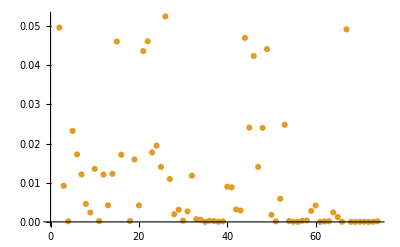

```mathematica
ListPlot[Tooltip[dt]]
```

```mathematica
meNmeTbMi=LogitModelFit[bC⟦2;;,{bMI,M1,menopause}⟧,{x,xM1},
{x,xM1}]
meNmeTbMi["BestFit"]
meNmeTbMi["ParameterTable"]
meNmeTbMient=meNmeTbMi["ParameterTableEntries"];
meNmeTbMif=Flatten[Position[meNmeTbMient[[All,4]],_?(#<0.05&)]]
```

FittedModel[1/(1+ⅇ^(-2.57933+«1»-«19» xM1))]

1/(1+ⅇ^(-2.57933+0.132327 x-1.49317 xM1))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 2.57933 | 0.990889 | 2.60305 | 0.00923993
x | -0.132327 | 0.0322342 | -4.10518 | 0.0000404002
xM1 | 1.49317 | 0.781275 | 1.9112 | 0.0559793

{1,2}

```mathematica
meNmeTbMi2=LogitModelFit[bC⟦2;;,{bMI,M1,M2,menopause}⟧,{1,x,xM1,xM2},
{x,xM1,xM2}]
meNmeTbMi2["BestFit"]
meNmeTbMi2["ParameterTable"]
meNmeTbMi2ent=meNmeTbMi2["ParameterTableEntries"];
meNmeTbMi2f=Flatten[Position[meNmeTbMi2ent[[All,4]],_?(#<0.05&)]]
```

FittedModel[1/(1+ⅇ^(-3.52854+«3»+«21» xM2))]

1/(1+ⅇ^(-3.52854+0.132481 x-1.46191 xM1+0.0178652 xM2))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 3.52854 | 1.46512 | 2.40837 | 0.0160241
x | -0.132481 | 0.0323061 | -4.1008 | 0.0000411718
xM1 | 1.46191 | 0.78258 | 1.86806 | 0.0617538
xM2 | -0.0178652 | 0.0201441 | -0.886871 | 0.375149

{1,2}

```mathematica
meNmeTbMi3=LogitModelFit[bC⟦2;;,{bMI,M1,M2,M3,menopause}⟧,{1,x,xM1,xM2,xM3},
{x,xM1,xM2,xM3}]
meNmeTbMi3["BestFit"]
meNmeTbMi3["ParameterTable"]
meNmeTbMi3ent=meNmeTbMi3["ParameterTableEntries"];
meNmeTbMi3f=Flatten[Position[meNmeTbMi3ent[[All,4]],_?(#<0.05&)]]
```

FittedModel[1/(1+ⅇ^(-3.67795+«4»+«20» xM3))]

1/(1+ⅇ^(-3.67795+0.132917 x-1.43035 xM1+0.0171049 xM2+0.0803872 xM3))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 3.67795 | 1.4959 | 2.45869 | 0.0139447
x | -0.132917 | 0.0323829 | -4.10453 | 0.0000405135
xM1 | 1.43035 | 0.785403 | 1.82116 | 0.0685821
xM2 | -0.0171049 | 0.0201924 | -0.847097 | 0.396941
xM3 | -0.0803872 | 0.158692 | -0.506561 | 0.612463

{1,2}

```mathematica
meNmeTbMi4=LogitModelFit[bC⟦2;;,{bMI,M1,M2,M3,M4,menopause}⟧,{1,x,xM1,xM2,xM3,xM4},
{x,xM1,xM2,xM3,xM4}]
meNmeTbMi4["BestFit"]
meNmeTbMi4["ParameterTable"]
meNmeTbMi4ent=meNmeTbMi4["ParameterTableEntries"];
meNmeTbMi4f=Flatten[Position[meNmeTbMi4ent[[All,4]],_?(#<0.05&)]]
```

FittedModel[1/(1+ⅇ^(-3.49625+«7»))]

1/(1+ⅇ^(-3.49625+0.135176 x-1.36798 xM1+0.0154464 xM2+0.206232 xM3-0.434743 xM4))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 3.49625 | 1.51131 | 2.31338 | 0.0207017
x | -0.135176 | 0.0326876 | -4.13539 | 0.000035436
xM1 | 1.36798 | 0.789569 | 1.73256 | 0.083173
xM2 | -0.0154464 | 0.0202326 | -0.763442 | 0.4452
xM3 | -0.206232 | 0.18629 | -1.10705 | 0.268272
xM4 | 0.434743 | 0.333728 | 1.30269 | 0.192682

{1,2}

```mathematica
meNmeTbMi5=LogitModelFit[bC⟦2;;,{bMI,M1,M2,M3,M4,M5,menopause}⟧,{1,x,xM1,xM2,xM3,xM4,xM5},
{x,xM1,xM2,xM3,xM4,xM5}]
meNmeTbMi5["BestFit"]
meNmeTbMi5["ParameterTable"]
meNmeTbMi5ent=meNmeTbMi5["ParameterTableEntries"];
meNmeTbMi5f=Flatten[Position[meNmeTbMi5ent[[All,4]],_?(#<0.05&)]]
```

FittedModel[1/(1+ⅇ^(-3.5079+«9»))]

1/(1+ⅇ^(-3.5079+0.138693 x-1.32849 xM1+0.0148976 xM2+0.333528 xM3-0.464008 xM4-0.122022 xM5))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 3.5079 | 1.51445 | 2.3163 | 0.0205422
x | -0.138693 | 0.0331697 | -4.18132 | 0.0000289817
xM1 | 1.32849 | 0.792554 | 1.67622 | 0.0936957
xM2 | -0.0148976 | 0.0202165 | -0.736901 | 0.461182
xM3 | -0.333528 | 0.226552 | -1.47219 | 0.140969
xM4 | 0.464008 | 0.332597 | 1.39511 | 0.162984
xM5 | 0.122022 | 0.123408 | 0.98877 | 0.322776

{1,2}

```mathematica
meNmeTbMi6=LogitModelFit[bC⟦2;;,{bMI,M1,M2,M3,M4,M5,M6,menopause}⟧,{1,x,xM1,xM2,xM3,xM4,xM5,xM6},
{x,xM1,xM2,xM3,xM4,xM5,xM6}]
meNmeTbMi6["BestFit"]
meNmeTbMi6["ParameterTable"]
meNmeTbMi6ent=meNmeTbMi6["ParameterTableEntries"];
meNmeTbMi6f=Flatten[Position[meNmeTbMi6ent[[All,4]],_?(#<0.05&)]]
```

FittedModel[1/(1+ⅇ^(-3.70806+«9»+«21» xM6))]

1/(1+ⅇ^(-3.70806+0.139194 x-1.32488 xM1+0.0176163 xM2+0.118093 xM3-1.05574 xM4-0.164962 xM5+0.0373471 xM6))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 3.70806 | 1.53436 | 2.41669 | 0.0156623
x | -0.139194 | 0.0339264 | -4.10283 | 0.000040812
xM1 | 1.32488 | 0.805034 | 1.64575 | 0.0998151
xM2 | -0.0176163 | 0.0205666 | -0.856551 | 0.391693
xM3 | -0.118093 | 0.245011 | -0.481992 | 0.629812
xM4 | 1.05574 | 0.414278 | 2.54838 | 0.0108223
xM5 | 0.164962 | 0.127796 | 1.29082 | 0.196766
xM6 | -0.0373471 | 0.0152837 | -2.44359 | 0.0145418

{1,2,6,8}

```mathematica
meNmeTbMi7=LogitModelFit[bC⟦2;;,{bMI,M1,M2,M3,M4,M5,M6,M7,menopause}⟧,{1,x,xM1,xM2,xM3,xM4,xM5,xM6,xM7},
{x,xM1,xM2,xM3,xM4,xM5,xM6,xM7}]
meNmeTbMi7["BestFit"]
meNmeTbMi7["ParameterTable"]
meNmeTbMi7ent=meNmeTbMi7["ParameterTableEntries"];
meNmeTbMi7f=Flatten[Position[meNmeTbMi7ent[[All,4]],_?(#<0.05&)]]
```

FittedModel[1/(1+ⅇ^(-3.37233+«12»))]

1/(1+ⅇ^(-3.37233+0.133303 x-1.31871 xM1+0.0161328 xM2+0.124513 xM3-1.02894 xM4-0.087633 xM5+0.0421693 xM6-0.0248111 xM7))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 3.37233 | 1.58934 | 2.12184 | 0.033851
x | -0.133303 | 0.0346452 | -3.84766 | 0.00011925
xM1 | 1.31871 | 0.805567 | 1.637 | 0.101631
xM2 | -0.0161328 | 0.0206168 | -0.78251 | 0.433915
xM3 | -0.124513 | 0.245696 | -0.506776 | 0.612312
xM4 | 1.02894 | 0.414408 | 2.48292 | 0.013031
xM5 | 0.087633 | 0.16211 | 0.540576 | 0.5888
xM6 | -0.0421693 | 0.0166143 | -2.53813 | 0.0111447
xM7 | 0.0248111 | 0.031911 | 0.777508 | 0.436859

{1,2,6,8}

```mathematica
meNmeTbMi8=LogitModelFit[bC⟦2;;,{bMI,M1,M2,M3,M4,M5,M6,M7,M8,menopause}⟧,{1,x,xM1,xM2,xM3,xM4,xM5,xM6,xM7,xM8},
{x,xM1,xM2,xM3,xM4,xM5,xM6,xM7,xM8}]
meNmeTbMi8["BestFit"]
meNmeTbMi8["ParameterTable"]
meNmeTbMi8ent=meNmeTbMi8["ParameterTableEntries"];
meNmeTbMi8f=Flatten[Position[meNmeTbMi8ent[[All,4]],_?(#<0.05&)]]
```

FittedModel[1/(1+ⅇ^(-3.11486+«14»))]

1/(1+ⅇ^(-3.11486+0.129301 x-1.35723 xM1+0.0171345 xM2+0.135113 xM3-1.06857 xM4-0.102881 xM5+0.0426081 xM6-0.0153751 xM7-0.0106608 xM8))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 3.11486 | 1.6167 | 1.92668 | 0.0540196
x | -0.129301 | 0.0349175 | -3.70303 | 0.000213038
xM1 | 1.35723 | 0.805721 | 1.68449 | 0.0920873
xM2 | -0.0171345 | 0.0207085 | -0.827415 | 0.408002
xM3 | -0.135113 | 0.247963 | -0.54489 | 0.585829
xM4 | 1.06857 | 0.418249 | 2.55487 | 0.0106227
xM5 | 0.102881 | 0.16343 | 0.629512 | 0.529014
xM6 | -0.0426081 | 0.0166875 | -2.5533 | 0.0106708
xM7 | 0.0153751 | 0.0335373 | 0.45845 | 0.646629
xM8 | 0.0106608 | 0.0126251 | 0.844411 | 0.39844

{2,6,8}

```mathematica
meNmeTbMi9=LogitModelFit[bC⟦2;;,{bMI,M1,M2,M3,M4,M5,M6,M7,M8,M9,menopause}⟧,{1,x,xM1,xM2,xM3,xM4,xM5,xM6,xM7,xM8,xM9},
{x,xM1,xM2,xM3,xM4,xM5,xM6,xM7,xM8,xM9}]
meNmeTbMi9["BestFit"]
meNmeTbMi9["ParameterTable"]
meNmeTbMi9ent=meNmeTbMi9["ParameterTableEntries"];
meNmeTbMi9f=Flatten[Position[meNmeTbMi9ent[[All,4]],_?(#<0.05&)]]
```

FittedModel[1/(1+ⅇ^(-3.08451+«14»+«22» xM9))]

1/(1+ⅇ^(-3.08451+0.129324 x-1.32676 xM1+0.0153004 xM2+0.125127 xM3-1.1011 xM4-0.115833 xM5+0.041306 xM6-0.0147854 xM7-0.0113269 xM8+0.0075623 xM9))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 3.08451 | 1.61804 | 1.90633 | 0.0566075
x | -0.129324 | 0.03488 | -3.70767 | 0.000209174
xM1 | 1.32676 | 0.812723 | 1.63249 | 0.102576
xM2 | -0.0153004 | 0.0212224 | -0.720956 | 0.470936
xM3 | -0.125127 | 0.249507 | -0.501498 | 0.616021
xM4 | 1.1011 | 0.426362 | 2.58256 | 0.00980715
xM5 | 0.115833 | 0.166469 | 0.695824 | 0.486539
xM6 | -0.041306 | 0.0170343 | -2.42487 | 0.0153139
xM7 | 0.0147854 | 0.0336571 | 0.439295 | 0.660447
xM8 | 0.0113269 | 0.0127965 | 0.885155 | 0.376073
xM9 | -0.0075623 | 0.0188879 | -0.400378 | 0.688878

{2,6,8}

```mathematica
meNmeTbMi10=LogitModelFit[bC⟦2;;,{bMI,M1,M2,M3,M4,M5,M6,M7,M8,M9,M10,menopause}⟧,{1,x,xM1,xM2,xM3,xM4,xM5,xM6,xM7,xM8,xM9,xM10},
{x,xM1,xM2,xM3,xM4,xM5,xM6,xM7,xM8,xM9,xM10}]
meNmeTbMi10["BestFit"]
meNmeTbMi10["ParameterTable"]
meNmeTbMi10ent=meNmeTbMi10["ParameterTableEntries"];
meNmeTbMi10f=Flatten[Position[meNmeTbMi10ent[[All,4]],_?(#<0.05&)]]
```

FittedModel[1/(1+ⅇ^(-2.54157+«15»+«22» xM9))]

1/(1+ⅇ^(-2.54157+0.124452 x-1.42322 xM1+0.128614 xM10+0.00950049 xM2+0.0686315 xM3-1.16483 xM4-0.109771 xM5+0.0187979 xM6-0.00957889 xM7-0.0114039 xM8+0.00329747 xM9))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 2.54157 | 1.70631 | 1.48951 | 0.136354
x | -0.124452 | 0.0349797 | -3.55784 | 0.000373923
xM1 | 1.42322 | 0.822914 | 1.72949 | 0.0837208
xM2 | -0.00950049 | 0.021963 | -0.432569 | 0.665328
xM3 | -0.0686315 | 0.254811 | -0.269343 | 0.787666
xM4 | 1.16483 | 0.434045 | 2.68365 | 0.00728232
xM5 | 0.109771 | 0.168089 | 0.65305 | 0.513724
xM6 | -0.0187979 | 0.0265647 | -0.707627 | 0.479177
xM7 | 0.00957889 | 0.0339819 | 0.281882 | 0.778034
xM8 | 0.0114039 | 0.0127391 | 0.895191 | 0.370685
xM9 | -0.00329747 | 0.019275 | -0.171075 | 0.864165
xM10 | -0.128614 | 0.115241 | -1.11605 | 0.264402

{2,6}

```mathematica
meNmeTbMi11=LogitModelFit[bC⟦2;;,{bMI,M1,M2,M3,M4,M5,M6,M7,M8,M9,M10,M11,menopause}⟧,{1,x,xM1,xM2,xM3,xM4,xM5,xM6,xM7,xM8,xM9,xM10,xM11},
{x,xM1,xM2,xM3,xM4,xM5,xM6,xM7,xM8,xM9,xM10,xM11}]
meNmeTbMi11["BestFit"]
meNmeTbMi11["ParameterTable"]
meNmeTbMi11ent=meNmeTbMi11["ParameterTableEntries"];
meNmeTbMi11f=Flatten[Position[meNmeTbMi11ent[[All,4]],_?(#<0.05&)]]
```

FittedModel[1/(1+ⅇ^(-2.14978+«16»+«21» xM9))]

1/(1+ⅇ^(-2.14978+0.125264 x-1.45061 xM1+0.108981 xM10+0.256508 xM11+0.00260095 xM2+0.106328 xM3-1.19008 xM4-0.105564 xM5+0.0232144 xM6-0.0750988 xM7-0.010775 xM8+0.00249529 xM9))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 2.14978 | 1.78355 | 1.20534 | 0.228073
x | -0.125264 | 0.0350302 | -3.57589 | 0.000349038
xM1 | 1.45061 | 0.824452 | 1.75949 | 0.0784949
xM2 | -0.00260095 | 0.0237146 | -0.109677 | 0.912665
xM3 | -0.106328 | 0.260426 | -0.408285 | 0.683065
xM4 | 1.19008 | 0.436142 | 2.72866 | 0.00635927
xM5 | 0.105564 | 0.167825 | 0.629013 | 0.529341
xM6 | -0.0232144 | 0.0273622 | -0.84841 | 0.396209
xM7 | 0.0750988 | 0.0885142 | 0.848438 | 0.396194
xM8 | 0.010775 | 0.0128312 | 0.839752 | 0.401047
xM9 | -0.00249529 | 0.0193231 | -0.129135 | 0.897251
xM10 | -0.108981 | 0.118859 | -0.916891 | 0.3592
xM11 | -0.256508 | 0.319061 | -0.803948 | 0.421427

{2,6}

```mathematica
meNmeTbMi12=LogitModelFit[bC⟦2;;,{bMI,M1,M2,M3,M4,M5,M6,M7,M8,M9,M10,M11,M12,menopause}⟧,{1,x,xM1,xM2,xM3,xM4,xM5,xM6,xM7,xM8,xM9,xM10,xM11,xM12},
{x,xM1,xM2,xM3,xM4,xM5,xM6,xM7,xM8,xM9,xM10,xM11,xM12}]
meNmeTbMi12["BestFit"]
meNmeTbMi12["ParameterTable"]
meNmeTbMi12ent=meNmeTbMi12["ParameterTableEntries"];
meNmeTbMi12f=Flatten[Position[meNmeTbMi12ent[[All,4]],_?(#<0.05&)]]
```

FittedModel[1/(1+ⅇ^(-2.16373+«17»+«22» xM9))]

1/(1+ⅇ^(-2.16373+0.124755 x-1.46116 xM1+0.104305 xM10+0.248207 xM11+0.0305967 xM12+0.00233978 xM2+0.122956 xM3-1.21543 xM4-0.118497 xM5+0.0235767 xM6-0.0779105 xM7-0.0113621 xM8+0.00283731 xM9))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 2.16373 | 1.77878 | 1.21641 | 0.223828
x | -0.124755 | 0.0351082 | -3.55344 | 0.000380233
xM1 | 1.46116 | 0.827222 | 1.76634 | 0.0773383
xM2 | -0.00233978 | 0.023661 | -0.0988876 | 0.921228
xM3 | -0.122956 | 0.264493 | -0.464873 | 0.642022
xM4 | 1.21543 | 0.442063 | 2.74945 | 0.00596957
xM5 | 0.118497 | 0.171747 | 0.68995 | 0.490226
xM6 | -0.0235767 | 0.0272015 | -0.866743 | 0.386083
xM7 | 0.0779105 | 0.0887385 | 0.877979 | 0.379955
xM8 | 0.0113621 | 0.0128921 | 0.881323 | 0.378143
xM9 | -0.00283731 | 0.0193303 | -0.146781 | 0.883305
xM10 | -0.104305 | 0.118421 | -0.880799 | 0.378427
xM11 | -0.248207 | 0.319719 | -0.776331 | 0.437554
xM12 | -0.0305967 | 0.083914 | -0.36462 | 0.715395

{2,6}

```mathematica
meNmeTbMi13=LogitModelFit[bC⟦2;;,{bMI,M1,M2,M3,M4,M5,M6,M7,M8,M9,M10,M11,M12,M13,menopause}⟧,{1,x,xM1,xM2,xM3,xM4,xM5,xM6,xM7,xM8,xM9,xM10,xM11,xM12,xM13},
{x,xM1,xM2,xM3,xM4,xM5,xM6,xM7,xM8,xM9,xM10,xM11,xM12,xM13}]
meNmeTbMi13["BestFit"]
meNmeTbMi13["ParameterTable"]
meNmeTbMi13ent=meNmeTbMi13["ParameterTableEntries"];
meNmeTbMi13f=Flatten[Position[meNmeTbMi13ent[[All,4]],_?(#<0.05&)]]
```

FittedModel[1/(1+ⅇ^(-1.8547+«19»+«21» xM9))]

1/(1+ⅇ^(-1.8547+0.125093 x-1.34314 xM1+0.0976081 xM10+0.339413 xM11+0.0875293 xM12-2.74864 xM13+0.00097433 xM2+0.194294 xM3-0.281199 xM4-0.143992 xM5+0.0536389 xM6-0.0968392 xM7-0.0172156 xM8+0.00805545 xM9))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 1.8547 | 1.83998 | 1.008 | 0.313453
x | -0.125093 | 0.0363914 | -3.43744 | 0.000587247
xM1 | 1.34314 | 0.851184 | 1.57797 | 0.114572
xM2 | -0.00097433 | 0.0245681 | -0.0396584 | 0.968365
xM3 | -0.194294 | 0.270647 | -0.717888 | 0.472827
xM4 | 0.281199 | 0.50361 | 0.558366 | 0.576595
xM5 | 0.143992 | 0.17857 | 0.806359 | 0.420036
xM6 | -0.0536389 | 0.0297651 | -1.80207 | 0.0715337
xM7 | 0.0968392 | 0.0910423 | 1.06367 | 0.287477
xM8 | 0.0172156 | 0.0134226 | 1.28258 | 0.199638
xM9 | -0.00805545 | 0.0205041 | -0.39287 | 0.694416
xM10 | -0.0976081 | 0.124406 | -0.784595 | 0.432691
xM11 | -0.339413 | 0.332286 | -1.02145 | 0.307042
xM12 | -0.0875293 | 0.0888702 | -0.984911 | 0.324668
xM13 | 2.74864 | 0.736448 | 3.73229 | 0.000189743

{2,15}

```mathematica
meNmeTbMi14=LogitModelFit[bC⟦2;;,{bMI,M1,M2,M3,M4,M5,M6,M7,M8,M9,M10,M11,M12,M13,M14,menopause}⟧,{1,x,xM1,xM2,xM3,xM4,xM5,xM6,xM7,xM8,xM9,xM10,xM11,xM12,xM13,xM14},
{x,xM1,xM2,xM3,xM4,xM5,xM6,xM7,xM8,xM9,xM10,xM11,xM12,xM13,xM14}]
meNmeTbMi14["BestFit"]
meNmeTbMi14["ParameterTable"]
meNmeTbMi14ent=meNmeTbMi14["ParameterTableEntries"];
meNmeTbMi14f=Flatten[Position[meNmeTbMi14ent[[All,4]],_?(#<0.05&)]]
```

FittedModel[1/(1+ⅇ^(-1.85654+«22»))]

1/(1+ⅇ^(-1.85654+0.125453 x-1.3984 xM1+0.0940436 xM10+0.361218 xM11+0.085941 xM12-2.82755 xM13+0.183183 xM14+0.00072379 xM2+0.166033 xM3-0.385427 xM4-0.168072 xM5+0.0491157 xM6-0.0990572 xM7-0.0203071 xM8-0.0120011 xM9))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 1.85654 | 1.84386 | 1.00687 | 0.313996
x | -0.125453 | 0.0365627 | -3.43118 | 0.000600958
xM1 | 1.3984 | 0.849886 | 1.64539 | 0.0998888
xM2 | -0.00072379 | 0.0246595 | -0.0293514 | 0.976584
xM3 | -0.166033 | 0.273988 | -0.605985 | 0.544524
xM4 | 0.385427 | 0.515602 | 0.747527 | 0.454746
xM5 | 0.168072 | 0.182316 | 0.92187 | 0.356596
xM6 | -0.0491157 | 0.0294777 | -1.6662 | 0.0956739
xM7 | 0.0990572 | 0.0914283 | 1.08344 | 0.278612
xM8 | 0.0203071 | 0.0136944 | 1.48287 | 0.138108
xM9 | 0.0120011 | 0.0279611 | 0.429208 | 0.667772
xM10 | -0.0940436 | 0.121659 | -0.773012 | 0.439515
xM11 | -0.361218 | 0.335161 | -1.07774 | 0.281148
xM12 | -0.085941 | 0.0887356 | -0.968507 | 0.332791
xM13 | 2.82755 | 0.745535 | 3.79264 | 0.000149054
xM14 | -0.183183 | 0.177324 | -1.03304 | 0.301585

{2,15}

```mathematica
meNmeTbMi15=LogitModelFit[bC⟦2;;,{bMI,M1,M2,M3,M4,M5,M6,M7,M8,M9,M10,M11,M12,M13,M14,M15,menopause}⟧,{1,x,xM1,xM2,xM3,xM4,xM5,xM6,xM7,xM8,xM9,xM10,xM11,xM12,xM13,xM14,xM15},
{x,xM1,xM2,xM3,xM4,xM5,xM6,xM7,xM8,xM9,xM10,xM11,xM12,xM13,xM14,xM15}]
meNmeTbMi15["BestFit"]
meNmeTbMi15["ParameterTable"]
meNmeTbMi15ent=meNmeTbMi15["ParameterTableEntries"];
meNmeTbMi15f=Flatten[Position[meNmeTbMi15ent[[All,4]],_?(#<0.05&)]]
```

FittedModel[1/(1+ⅇ^(-2.70226+«24»))]

1/(1+ⅇ^(-2.70226+0.125213 x-1.74779 xM1+0.154244 xM10+0.354524 xM11+0.102819 xM12-2.71374 xM13+0.158317 xM14+0.344786 xM15+0.00821299 xM2-0.295423 xM3-0.220196 xM4-0.236148 xM5+0.0468833 xM6-0.093162 xM7-0.0259525 xM8-0.00767453 xM9))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 2.70226 | 1.91604 | 1.41034 | 0.158439
x | -0.125213 | 0.0364657 | -3.43373 | 0.000595346
xM1 | 1.74779 | 0.871924 | 2.00452 | 0.0450143
xM2 | -0.00821299 | 0.0253847 | -0.323541 | 0.746285
xM3 | 0.295423 | 0.335924 | 0.879432 | 0.379167
xM4 | 0.220196 | 0.527094 | 0.417755 | 0.676126
xM5 | 0.236148 | 0.190562 | 1.23922 | 0.215264
xM6 | -0.0468833 | 0.0296839 | -1.57942 | 0.114239
xM7 | 0.093162 | 0.0924732 | 1.00745 | 0.313719
xM8 | 0.0259525 | 0.014007 | 1.85282 | 0.0639087
xM9 | 0.00767453 | 0.0275517 | 0.27855 | 0.78059
xM10 | -0.154244 | 0.126367 | -1.2206 | 0.222238
xM11 | -0.354524 | 0.340173 | -1.04219 | 0.297324
xM12 | -0.102819 | 0.0901809 | -1.14014 | 0.254227
xM13 | 2.71374 | 0.758815 | 3.57629 | 0.000348509
xM14 | -0.158317 | 0.177175 | -0.893561 | 0.371557
xM15 | -0.344786 | 0.143871 | -2.3965 | 0.0165526

{2,3,15,17}

```mathematica
meNmeTbMi16=LogitModelFit[bC⟦2;;,{bMI,M1,M2,M3,M4,M5,M6,M7,M8,M9,M10,M11,M12,M13,M14,M15,M16,menopause}⟧,{1,x,xM1,xM2,xM3,xM4,xM5,xM6,xM7,xM8,xM9,xM10,xM11,xM12,xM13,xM14,xM15,xM16},
{x,xM1,xM2,xM3,xM4,xM5,xM6,xM7,xM8,xM9,xM10,xM11,xM12,xM13,xM14,xM15,xM16}]
meNmeTbMi16["BestFit"]
meNmeTbMi16["ParameterTable"]
meNmeTbMi16ent=meNmeTbMi16["ParameterTableEntries"];
meNmeTbMi16f=Flatten[Position[meNmeTbMi16ent[[All,4]],_?(#<0.05&)]]
```

FittedModel[1/(1+ⅇ^(-3.0723+«25»))]

1/(1+ⅇ^(-3.0723+0.121072 x-2.0241 xM1+0.178492 xM10+0.449433 xM11+0.0611245 xM12-2.93827 xM13+0.165704 xM14+0.164272 xM15+0.121249 xM16+0.00569737 xM2-0.0989206 xM3-0.244913 xM4-0.21554 xM5+0.0410879 xM6-0.12329 xM7-0.0223731 xM8-0.00962374 xM9))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 3.0723 | 1.94186 | 1.58215 | 0.113616
x | -0.121072 | 0.0367012 | -3.29885 | 0.000970809
xM1 | 2.0241 | 0.892145 | 2.2688 | 0.0232806
xM2 | -0.00569737 | 0.0255611 | -0.222892 | 0.82362
xM3 | 0.0989206 | 0.354736 | 0.278857 | 0.780355
xM4 | 0.244913 | 0.532968 | 0.459527 | 0.645856
xM5 | 0.21554 | 0.190337 | 1.13241 | 0.257461
xM6 | -0.0410879 | 0.0298404 | -1.37692 | 0.168536
xM7 | 0.12329 | 0.0946295 | 1.30287 | 0.192618
xM8 | 0.0223731 | 0.0143038 | 1.56414 | 0.117785
xM9 | 0.00962374 | 0.0278137 | 0.346007 | 0.729338
xM10 | -0.178492 | 0.12875 | -1.38634 | 0.165643
xM11 | -0.449433 | 0.345724 | -1.29998 | 0.193609
xM12 | -0.0611245 | 0.0934566 | -0.654042 | 0.513085
xM13 | 2.93827 | 0.774337 | 3.79456 | 0.000147904
xM14 | -0.165704 | 0.179815 | -0.921523 | 0.356777
xM15 | -0.164272 | 0.174431 | -0.94176 | 0.346315
xM16 | -0.121249 | 0.0665664 | -1.82147 | 0.0685349

{2,3,15}

```mathematica
meNmeTbMi17=LogitModelFit[bC⟦2;;,{bMI,M1,M2,M3,M4,M5,M6,M7,M8,M9,M10,M11,M12,M13,M14,M15,M16,M17,menopause}⟧,{1,x,xM1,xM2,xM3,xM4,xM5,xM6,xM7,xM8,xM9,xM10,xM11,xM12,xM13,xM14,xM15,xM16,xM17},
{x,xM1,xM2,xM3,xM4,xM5,xM6,xM7,xM8,xM9,xM10,xM11,xM12,xM13,xM14,xM15,xM16,xM17}]
meNmeTbMi17["BestFit"]
meNmeTbMi17["ParameterTable"]
meNmeTbMi17ent=meNmeTbMi17["ParameterTableEntries"];
meNmeTbMi17f=Flatten[Position[meNmeTbMi17ent[[All,4]],_?(#<0.05&)]]
```

FittedModel[1/(1+ⅇ^(-2.79054+«26»))]

1/(1+ⅇ^(-2.79054+0.111189 x-1.84575 xM1+0.192724 xM10+0.490509 xM11+0.0406753 xM12-2.98187 xM13+0.126459 xM14+0.1375 xM15+0.199306 xM16-0.535484 xM17+0.00761371 xM2-0.198416 xM3+0.0742557 xM4-0.198127 xM5+0.0394793 xM6-0.129278 xM7-0.0209166 xM8-0.0113403 xM9))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 2.79054 | 1.97851 | 1.41043 | 0.158413
x | -0.111189 | 0.0374551 | -2.96858 | 0.00299176
xM1 | 1.84575 | 0.908697 | 2.03121 | 0.0422341
xM2 | -0.00761371 | 0.0261308 | -0.291369 | 0.770769
xM3 | 0.198416 | 0.362684 | 0.547078 | 0.584325
xM4 | -0.0742557 | 0.563301 | -0.131823 | 0.895125
xM5 | 0.198127 | 0.190388 | 1.04065 | 0.298039
xM6 | -0.0394793 | 0.0296493 | -1.33154 | 0.183011
xM7 | 0.129278 | 0.0949914 | 1.36095 | 0.17353
xM8 | 0.0209166 | 0.0145358 | 1.43897 | 0.150158
xM9 | 0.0113403 | 0.0280414 | 0.404415 | 0.685908
xM10 | -0.192724 | 0.127567 | -1.51076 | 0.130849
xM11 | -0.490509 | 0.349747 | -1.40247 | 0.160776
xM12 | -0.0406753 | 0.0951591 | -0.427446 | 0.669055
xM13 | 2.98187 | 0.780718 | 3.81939 | 0.000133782
xM14 | -0.126459 | 0.181951 | -0.695015 | 0.487046
xM15 | -0.1375 | 0.178565 | -0.770028 | 0.441283
xM16 | -0.199306 | 0.0804227 | -2.47823 | 0.0132037
xM17 | 0.535484 | 0.29781 | 1.79807 | 0.0721661

{2,3,15,18}

```mathematica
meNmeTbMi18=LogitModelFit[bC⟦2;;,{bMI,M1,M2,M3,M4,M5,M6,M7,M8,M9,M10,M11,M12,M13,M14,M15,M16,M17,M18,menopause}⟧,{1,x,xM1,xM2,xM3,xM4,xM5,xM6,xM7,xM8,xM9,xM10,xM11,xM12,xM13,xM14,xM15,xM16,xM17,xM18},
{x,xM1,xM2,xM3,xM4,xM5,xM6,xM7,xM8,xM9,xM10,xM11,xM12,xM13,xM14,xM15,xM16,xM17,xM18}]
meNmeTbMi18["BestFit"]
meNmeTbMi18["ParameterTable"]
meNmeTbMi18ent=meNmeTbMi18["ParameterTableEntries"];
meNmeTbMi18f=Flatten[Position[meNmeTbMi18ent[[All,4]],_?(#<0.05&)]]
```

FittedModel[1/(1+ⅇ^(-2.98157+«28»))]

1/(1+ⅇ^(-2.98157+0.113931 x-1.73219 xM1+0.197453 xM10+0.498729 xM11+0.0294771 xM12-3.13039 xM13+0.140396 xM14+0.240347 xM15+0.208725 xM16-0.543224 xM17-0.0373773 xM18+0.00785021 xM2-0.276268 xM3+0.0823428 xM4-0.00703777 xM5+0.0360109 xM6-0.125297 xM7-0.0248391 xM8-0.010832 xM9))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 2.98157 | 1.9912 | 1.49737 | 0.134296
x | -0.113931 | 0.0373886 | -3.04722 | 0.00230972
xM1 | 1.73219 | 0.918633 | 1.88562 | 0.0593466
xM2 | -0.00785021 | 0.0261158 | -0.300592 | 0.763725
xM3 | 0.276268 | 0.371483 | 0.743689 | 0.457064
xM4 | -0.0823428 | 0.565456 | -0.145622 | 0.88422
xM5 | 0.00703777 | 0.272379 | 0.0258381 | 0.979386
xM6 | -0.0360109 | 0.0298618 | -1.20592 | 0.227849
xM7 | 0.125297 | 0.0949983 | 1.31894 | 0.18719
xM8 | 0.0248391 | 0.0151435 | 1.64025 | 0.100954
xM9 | 0.010832 | 0.0281455 | 0.384856 | 0.700344
xM10 | -0.197453 | 0.1284 | -1.53779 | 0.1241
xM11 | -0.498729 | 0.350974 | -1.42099 | 0.155321
xM12 | -0.0294771 | 0.0959482 | -0.307219 | 0.758676
xM13 | 3.13039 | 0.808309 | 3.87276 | 0.000107611
xM14 | -0.140396 | 0.183335 | -0.765791 | 0.443801
xM15 | -0.240347 | 0.206608 | -1.1633 | 0.244707
xM16 | -0.208725 | 0.0811448 | -2.57226 | 0.0101038
xM17 | 0.543224 | 0.299062 | 1.81643 | 0.0693049
xM18 | 0.0373773 | 0.0378943 | 0.986357 | 0.323958

{2,15,18}

```mathematica
meNmeTbMi19=LogitModelFit[bC⟦2;;,{bMI,M1,M2,M3,M4,M5,M6,M7,M8,M9,M10,M11,M12,M13,M14,M15,M16,M17,M18,M19,menopause}⟧,{1,x,xM1,xM2,xM3,xM4,xM5,xM6,xM7,xM8,xM9,xM10,xM11,xM12,xM13,xM14,xM15,xM16,xM17,xM18,xM19},
{x,xM1,xM2,xM3,xM4,xM5,xM6,xM7,xM8,xM9,xM10,xM11,xM12,xM13,xM14,xM15,xM16,xM17,xM18,xM19}]
meNmeTbMi19["BestFit"]
meNmeTbMi19["ParameterTable"]
meNmeTbMi19ent=meNmeTbMi19["ParameterTableEntries"];
meNmeTbMi19f=Flatten[Position[meNmeTbMi19ent[[All,4]],_?(#<0.05&)]]
```

FittedModel[1/(1+ⅇ^(-2.8252+«30»))]

1/(1+ⅇ^(-2.8252+0.113583 x-1.61612 xM1+0.193886 xM10+0.490288 xM11+0.0289761 xM12-2.93099 xM13+0.117867 xM14+0.281312 xM15+0.215871 xM16-0.499167 xM17-0.0359866 xM18-0.215148 xM19+0.00828669 xM2-0.129697 xM3-0.101825 xM4+0.0135438 xM5+0.0372086 xM6-0.133452 xM7-0.0215477 xM8-0.0133619 xM9))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 2.8252 | 2.00637 | 1.40812 | 0.159096
x | -0.113583 | 0.0377042 | -3.01248 | 0.0025912
xM1 | 1.61612 | 0.925497 | 1.74622 | 0.0807724
xM2 | -0.00828669 | 0.0261155 | -0.31731 | 0.751009
xM3 | 0.129697 | 0.398448 | 0.325505 | 0.744799
xM4 | 0.101825 | 0.592591 | 0.171829 | 0.863572
xM5 | -0.0135438 | 0.276221 | -0.0490325 | 0.960893
xM6 | -0.0372086 | 0.0303617 | -1.22551 | 0.220383
xM7 | 0.133452 | 0.0960344 | 1.38962 | 0.164644
xM8 | 0.0215477 | 0.0155186 | 1.38851 | 0.164983
xM9 | 0.0133619 | 0.0286019 | 0.46717 | 0.640378
xM10 | -0.193886 | 0.13028 | -1.48822 | 0.136692
xM11 | -0.490288 | 0.3523 | -1.39168 | 0.16402
xM12 | -0.0289761 | 0.096486 | -0.300314 | 0.763938
xM13 | 2.93099 | 0.826003 | 3.5484 | 0.000387574
xM14 | -0.117867 | 0.185384 | -0.635802 | 0.524906
xM15 | -0.281312 | 0.21083 | -1.33431 | 0.182104
xM16 | -0.215871 | 0.0820508 | -2.63094 | 0.0085149
xM17 | 0.499167 | 0.301171 | 1.65742 | 0.0974341
xM18 | 0.0359866 | 0.0379222 | 0.948957 | 0.342642
xM19 | 0.215148 | 0.193824 | 1.11002 | 0.26699

{2,15,18}

```mathematica
meNmeTbMi20=LogitModelFit[bC⟦2;;,{bMI,M1,M2,M3,M4,M5,M6,M7,M8,M9,M10,M11,M12,M13,M14,M15,M16,M17,M18,M19,M20,menopause}⟧,{1,x,xM1,xM2,xM3,xM4,xM5,xM6,xM7,xM8,xM9,xM10,xM11,xM12,xM13,xM14,xM15,xM16,xM17,xM18,xM19,xM20},
{x,xM1,xM2,xM3,xM4,xM5,xM6,xM7,xM8,xM9,xM10,xM11,xM12,xM13,xM14,xM15,xM16,xM17,xM18,xM19,xM20}]
meNmeTbMi20["BestFit"]
meNmeTbMi20["ParameterTable"]
meNmeTbMi20ent=meNmeTbMi20["ParameterTableEntries"];
meNmeTbMi20f=Flatten[Position[meNmeTbMi20ent[[All,4]],_?(#<0.05&)]]
```

FittedModel[1/(1+ⅇ^(-2.44647+«30»))]

1/(1+ⅇ^(-2.44647+0.104682 x-1.63161 xM1+0.164279 xM10+0.520933 xM11+0.037186 xM12-3.11369 xM13+0.0761753 xM14+0.254399 xM15+0.189394 xM16-0.561549 xM17-0.0399696 xM18-0.218428 xM19+0.000316253 xM2+0.363604 xM20-0.00820455 xM3+0.090367 xM4+0.0400659 xM5+0.0361259 xM6-0.136544 xM7-0.0235386 xM8-0.00963654 xM9))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 2.44647 | 2.03951 | 1.19954 | 0.230317
x | -0.104682 | 0.0381236 | -2.74585 | 0.00603543
xM1 | 1.63161 | 0.934879 | 1.74526 | 0.0809389
xM2 | -0.000316253 | 0.0269082 | -0.011753 | 0.990623
xM3 | 0.00820455 | 0.408472 | 0.0200859 | 0.983975
xM4 | -0.090367 | 0.612912 | -0.147439 | 0.882786
xM5 | -0.0400659 | 0.276139 | -0.145093 | 0.884637
xM6 | -0.0361259 | 0.0299622 | -1.20572 | 0.227927
xM7 | 0.136544 | 0.0956236 | 1.42794 | 0.15331
xM8 | 0.0235386 | 0.0156939 | 1.49986 | 0.133651
xM9 | 0.00963654 | 0.0293367 | 0.328481 | 0.742548
xM10 | -0.164279 | 0.130154 | -1.26219 | 0.206879
xM11 | -0.520933 | 0.351581 | -1.48169 | 0.138424
xM12 | -0.037186 | 0.0967322 | -0.384422 | 0.700665
xM13 | 3.11369 | 0.847268 | 3.67498 | 0.00023787
xM14 | -0.0761753 | 0.189285 | -0.402438 | 0.687362
xM15 | -0.254399 | 0.213553 | -1.19127 | 0.233547
xM16 | -0.189394 | 0.084181 | -2.24984 | 0.0244592
xM17 | 0.561549 | 0.308846 | 1.81822 | 0.0690312
xM18 | 0.0399696 | 0.0381546 | 1.04757 | 0.294837
xM19 | 0.218428 | 0.193906 | 1.12646 | 0.25997
xM20 | -0.363604 | 0.263773 | -1.37847 | 0.168058

{2,15,18}

```mathematica
meNmeTbMi21=LogitModelFit[bC⟦2;;,{bMI,M1,M2,M3,M4,M5,M6,M7,M8,M9,M10,M11,M12,M13,M14,M15,M16,M17,M18,M19,M20,M21,menopause}⟧,{1,x,xM1,xM2,xM3,xM4,xM5,xM6,xM7,xM8,xM9,xM10,xM11,xM12,xM13,xM14,xM15,xM16,xM17,xM18,xM19,xM20,xM21},
{x,xM1,xM2,xM3,xM4,xM5,xM6,xM7,xM8,xM9,xM10,xM11,xM12,xM13,xM14,xM15,xM16,xM17,xM18,xM19,xM20,xM21}]
meNmeTbMi21["BestFit"]
meNmeTbMi21["ParameterTable"]
meNmeTbMi21ent=meNmeTbMi21["ParameterTableEntries"];
meNmeTbMi21f=Flatten[Position[meNmeTbMi21ent[[All,4]],_?(#<0.05&)]]
```

FittedModel[1/(1+ⅇ^(-2.81431+«31»))]

1/(1+ⅇ^(-2.81431+0.10502 x-1.34552 xM1+0.168226 xM10+0.465121 xM11+0.0410202 xM12-3.07939 xM13+0.0875976 xM14+0.142839 xM15+0.19011 xM16-0.605533 xM17-0.0462481 xM18-0.222873 xM19-0.00143782 xM2+0.357554 xM20+0.0121038 xM21+0.0214134 xM3+0.0957739 xM4+0.0594384 xM5+0.040087 xM6-0.139291 xM7-0.0209259 xM8-0.0166087 xM9))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 2.81431 | 2.06578 | 1.36235 | 0.173088
x | -0.10502 | 0.0377931 | -2.77881 | 0.00545576
xM1 | 1.34552 | 0.956589 | 1.40658 | 0.159553
xM2 | 0.00143782 | 0.0272044 | 0.0528525 | 0.957849
xM3 | -0.0214134 | 0.41275 | -0.0518799 | 0.958624
xM4 | -0.0957739 | 0.614409 | -0.15588 | 0.876128
xM5 | -0.0594384 | 0.278959 | -0.213072 | 0.83127
xM6 | -0.040087 | 0.0303824 | -1.31942 | 0.18703
xM7 | 0.139291 | 0.0955581 | 1.45766 | 0.144935
xM8 | 0.0209259 | 0.0158119 | 1.32343 | 0.185694
xM9 | 0.0166087 | 0.0295555 | 0.561949 | 0.574151
xM10 | -0.168226 | 0.130789 | -1.28624 | 0.198359
xM11 | -0.465121 | 0.354541 | -1.3119 | 0.189555
xM12 | -0.0410202 | 0.0972785 | -0.421678 | 0.67326
xM13 | 3.07939 | 0.855252 | 3.60057 | 0.000317523
xM14 | -0.0875976 | 0.189319 | -0.462699 | 0.64358
xM15 | -0.142839 | 0.231149 | -0.617952 | 0.536607
xM16 | -0.19011 | 0.0848515 | -2.2405 | 0.0250584
xM17 | 0.605533 | 0.311395 | 1.94458 | 0.0518254
xM18 | 0.0462481 | 0.0390414 | 1.18459 | 0.236179
xM19 | 0.222873 | 0.195681 | 1.13896 | 0.254719
xM20 | -0.357554 | 0.266463 | -1.34185 | 0.179644
xM21 | -0.0121038 | 0.00910088 | -1.32996 | 0.183532

{2,15,18}

```mathematica
meNmeTbMi22=LogitModelFit[bC⟦2;;,{bMI,M1,M2,M3,M4,M5,M6,M7,M8,M9,M10,M11,M12,M13,M14,M15,M16,M17,M18,M19,M20,M21,M22,menopause}⟧,{1,x,xM1,xM2,xM3,xM4,xM5,xM6,xM7,xM8,xM9,xM10,xM11,xM12,xM13,xM14,xM15,xM16,xM17,xM18,xM19,xM20,xM21,xM22},
{x,xM1,xM2,xM3,xM4,xM5,xM6,xM7,xM8,xM9,xM10,xM11,xM12,xM13,xM14,xM15,xM16,xM17,xM18,xM19,xM20,xM21,xM22}]
meNmeTbMi22["BestFit"]
meNmeTbMi22["ParameterTable"]
meNmeTbMi22ent=meNmeTbMi22["ParameterTableEntries"];
meNmeTbMi22f=Flatten[Position[meNmeTbMi22ent[[All,4]],_?(#<0.05&)]]
```

FittedModel[1/(1+ⅇ^(-2.79384+«32»))]

1/(1+ⅇ^(-2.79384+0.100782 x-1.35646 xM1+0.177537 xM10+0.44981 xM11+0.0382361 xM12-3.12884 xM13+0.0956022 xM14+0.115074 xM15+0.193449 xM16-0.564101 xM17-0.0590891 xM18-0.113948 xM19+0.00127222 xM2+0.403707 xM20+0.0201416 xM21-0.0136479 xM22+0.0110385 xM3+0.068354 xM4+0.0540566 xM5+0.0395559 xM6-0.142861 xM7-0.0178139 xM8-0.0170332 xM9))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 2.79384 | 2.07831 | 1.34429 | 0.178856
x | -0.100782 | 0.038051 | -2.64859 | 0.00808275
xM1 | 1.35646 | 0.958934 | 1.41455 | 0.157201
xM2 | -0.00127222 | 0.0274208 | -0.0463962 | 0.962994
xM3 | -0.0110385 | 0.409949 | -0.0269265 | 0.978518
xM4 | -0.068354 | 0.613948 | -0.111335 | 0.911351
xM5 | -0.0540566 | 0.280255 | -0.192883 | 0.84705
xM6 | -0.0395559 | 0.0306389 | -1.29103 | 0.196692
xM7 | 0.142861 | 0.0957145 | 1.49258 | 0.135548
xM8 | 0.0178139 | 0.0160873 | 1.10733 | 0.268152
xM9 | 0.0170332 | 0.0292424 | 0.582484 | 0.560241
xM10 | -0.177537 | 0.131977 | -1.34521 | 0.178556
xM11 | -0.44981 | 0.355322 | -1.26592 | 0.205542
xM12 | -0.0382361 | 0.0980209 | -0.390081 | 0.696477
xM13 | 3.12884 | 0.859846 | 3.63884 | 0.000273869
xM14 | -0.0956022 | 0.189061 | -0.505669 | 0.613089
xM15 | -0.115074 | 0.233391 | -0.493052 | 0.621976
xM16 | -0.193449 | 0.0849648 | -2.27682 | 0.0227971
xM17 | 0.564101 | 0.311134 | 1.81305 | 0.0698242
xM18 | 0.0590891 | 0.0411454 | 1.4361 | 0.150973
xM19 | 0.113948 | 0.218031 | 0.522623 | 0.601236
xM20 | -0.403707 | 0.270251 | -1.49382 | 0.135222
xM21 | -0.0201416 | 0.0115906 | -1.73775 | 0.0822542
xM22 | 0.0136479 | 0.0118569 | 1.15105 | 0.249712

{2,15,18}

```mathematica
meNmeTbMi23=LogitModelFit[bC⟦2;;,{bMI,M1,M2,M3,M4,M5,M6,M7,M8,M9,M10,M11,M12,M13,M14,M15,M16,M17,M18,M19,M20,M21,M22,M23,menopause}⟧,{1,x,xM1,xM2,xM3,xM4,xM5,xM6,xM7,xM8,xM9,xM10,xM11,xM12,xM13,xM14,xM15,xM16,xM17,xM18,xM19,xM20,xM21,xM22,xM23},
{x,xM1,xM2,xM3,xM4,xM5,xM6,xM7,xM8,xM9,xM10,xM11,xM12,xM13,xM14,xM15,xM16,xM17,xM18,xM19,xM20,xM21,xM22,xM23}]
meNmeTbMi23["BestFit"]
meNmeTbMi23["ParameterTable"]
meNmeTbMi23ent=meNmeTbMi23["ParameterTableEntries"];
meNmeTbMi23f=Flatten[Position[meNmeTbMi23ent[[All,4]],_?(#<0.05&)]]
```

FittedModel[1/(1+ⅇ^(-2.79484+«34»))]

1/(1+ⅇ^(-2.79484+0.101299 x-1.31751 xM1+0.17458 xM10+0.435775 xM11+0.0346881 xM12-3.10775 xM13+0.0979999 xM14+0.104347 xM15+0.206275 xM16-0.554986 xM17-0.0521765 xM18-0.103766 xM19+0.00179389 xM2+0.421103 xM20+0.021398 xM21-0.0147497 xM22-0.002133 xM23+0.0145231 xM3+0.0399273 xM4+0.0314294 xM5+0.039295 xM6-0.131629 xM7-0.0179461 xM8-0.0179187 xM9))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 2.79484 | 2.08229 | 1.3422 | 0.179532
x | -0.101299 | 0.0380657 | -2.66116 | 0.00778715
xM1 | 1.31751 | 0.966257 | 1.36352 | 0.172719
xM2 | -0.00179389 | 0.0274515 | -0.0653477 | 0.947897
xM3 | -0.0145231 | 0.409858 | -0.0354345 | 0.971733
xM4 | -0.0399273 | 0.617818 | -0.0646262 | 0.948472
xM5 | -0.0314294 | 0.287084 | -0.109478 | 0.912823
xM6 | -0.039295 | 0.0307446 | -1.27811 | 0.20121
xM7 | 0.131629 | 0.100036 | 1.31581 | 0.188236
xM8 | 0.0179461 | 0.0160893 | 1.11541 | 0.264676
xM9 | 0.0179187 | 0.029365 | 0.610206 | 0.541725
xM10 | -0.17458 | 0.132141 | -1.32116 | 0.186447
xM11 | -0.435775 | 0.356599 | -1.22203 | 0.221696
xM12 | -0.0346881 | 0.098542 | -0.352014 | 0.724828
xM13 | 3.10775 | 0.861341 | 3.60804 | 0.000308517
xM14 | -0.0979999 | 0.189427 | -0.51735 | 0.604912
xM15 | -0.104347 | 0.234804 | -0.4444 | 0.656753
xM16 | -0.206275 | 0.0917658 | -2.24784 | 0.0245862
xM17 | 0.554986 | 0.311567 | 1.78127 | 0.0748684
xM18 | 0.0521765 | 0.0450261 | 1.1588 | 0.246536
xM19 | 0.103766 | 0.21956 | 0.472609 | 0.636492
xM20 | -0.421103 | 0.274313 | -1.53512 | 0.124755
xM21 | -0.021398 | 0.0120753 | -1.77205 | 0.0763867
xM22 | 0.0147497 | 0.0122266 | 1.20636 | 0.227678
xM23 | 0.002133 | 0.00568239 | 0.37537 | 0.707386

{2,15,18}

```mathematica
meNmeTbMi24=LogitModelFit[bC⟦2;;,{bMI,M1,M2,M3,M4,M5,M6,M7,M8,M9,M10,M11,M12,M13,M14,M15,M16,M17,M18,M19,M20,M21,M22,M23,M24,menopause}⟧,{1,x,xM1,xM2,xM3,xM4,xM5,xM6,xM7,xM8,xM9,xM10,xM11,xM12,xM13,xM14,xM15,xM16,xM17,xM18,xM19,xM20,xM21,xM22,xM23,xM24},
{x,xM1,xM2,xM3,xM4,xM5,xM6,xM7,xM8,xM9,xM10,xM11,xM12,xM13,xM14,xM15,xM16,xM17,xM18,xM19,xM20,xM21,xM22,xM23,xM24}]
meNmeTbMi24["BestFit"]
meNmeTbMi24["ParameterTable"]
meNmeTbMi24ent=meNmeTbMi24["ParameterTableEntries"];
meNmeTbMi24f=Flatten[Position[meNmeTbMi24ent[[All,4]],_?(#<0.05&)]]
```

FittedModel[1/(1+ⅇ^(-2.49646+«36»))]

1/(1+ⅇ^(-2.49646+0.0991648 x-1.33369 xM1+0.154072 xM10+0.523587 xM11+0.0259133 xM12-3.20884 xM13+0.084325 xM14+0.071058 xM15+0.209684 xM16-0.358367 xM17-0.0538071 xM18-0.119984 xM19+0.00333131 xM2+0.468896 xM20+0.0257438 xM21-0.0141777 xM22-0.00281535 xM23-0.0116764 xM24+0.0149772 xM3+0.0999169 xM4+0.0218685 xM5+0.0415278 xM6-0.151828 xM7-0.0162845 xM8-0.0095517 xM9))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 2.49646 | 2.10458 | 1.1862 | 0.235542
x | -0.0991648 | 0.0380725 | -2.60463 | 0.00919738
xM1 | 1.33369 | 0.970441 | 1.37432 | 0.169344
xM2 | -0.00333131 | 0.0274905 | -0.121181 | 0.903548
xM3 | -0.0149772 | 0.411796 | -0.0363704 | 0.970987
xM4 | -0.0999169 | 0.621165 | -0.160854 | 0.872209
xM5 | -0.0218685 | 0.290557 | -0.075264 | 0.940005
xM6 | -0.0415278 | 0.0306709 | -1.35398 | 0.175743
xM7 | 0.151828 | 0.102329 | 1.48372 | 0.137883
xM8 | 0.0162845 | 0.0162656 | 1.00116 | 0.316749
xM9 | 0.0095517 | 0.0304295 | 0.313896 | 0.7536
xM10 | -0.154072 | 0.133081 | -1.15773 | 0.246974
xM11 | -0.523587 | 0.369001 | -1.41893 | 0.155919
xM12 | -0.0259133 | 0.0993991 | -0.2607 | 0.794324
xM13 | 3.20884 | 0.870914 | 3.68445 | 0.000229197
xM14 | -0.084325 | 0.190271 | -0.443183 | 0.657633
xM15 | -0.071058 | 0.23745 | -0.299255 | 0.764745
xM16 | -0.209684 | 0.0919718 | -2.27987 | 0.0226152
xM17 | 0.358367 | 0.360269 | 0.994721 | 0.319872
xM18 | 0.0538071 | 0.0454391 | 1.18416 | 0.236351
xM19 | 0.119984 | 0.220815 | 0.54337 | 0.586875
xM20 | -0.468896 | 0.278123 | -1.68593 | 0.0918096
xM21 | -0.0257438 | 0.0128243 | -2.00742 | 0.0447054
xM22 | 0.0141777 | 0.0122731 | 1.15518 | 0.248017
xM23 | 0.00281535 | 0.00572472 | 0.491788 | 0.622869
xM24 | 0.0116764 | 0.0112074 | 1.04185 | 0.297481

{2,15,18,23}

```mathematica
meNmeTbMi25=LogitModelFit[bC⟦2;;,{bMI,M1,M2,M3,M4,M5,M6,M7,M8,M9,M10,M11,M12,M13,M14,M15,M16,M17,M18,M19,M20,M21,M22,M23,M24,M25,menopause}⟧,{1,x,xM1,xM2,xM3,xM4,xM5,xM6,xM7,xM8,xM9,xM10,xM11,xM12,xM13,xM14,xM15,xM16,xM17,xM18,xM19,xM20,xM21,xM22,xM23,xM24,xM25},
{x,xM1,xM2,xM3,xM4,xM5,xM6,xM7,xM8,xM9,xM10,xM11,xM12,xM13,xM14,xM15,xM16,xM17,xM18,xM19,xM20,xM21,xM22,xM23,xM24,xM25}]
meNmeTbMi25["BestFit"]
meNmeTbMi25["ParameterTable"]
meNmeTbMi25ent=meNmeTbMi25["ParameterTableEntries"];
meNmeTbMi25f=Flatten[Position[meNmeTbMi25ent[[All,4]],_?(#<0.05&)]]
```

FittedModel[1/(1+ⅇ^(-2.22908+«38»))]

1/(1+ⅇ^(-2.22908+0.101381 x-1.47239 xM1+0.170532 xM10+0.487475 xM11+0.0227089 xM12-3.33686 xM13+0.0759169 xM14-0.0215787 xM15+0.25701 xM16-0.337802 xM17-0.0616037 xM18+0.0304027 xM19+0.0043211 xM2+0.446718 xM20+0.0221776 xM21-0.00783225 xM22+0.00134721 xM23-0.0128534 xM24-0.00467022 xM25-0.0235006 xM3+0.131259 xM4+0.0316718 xM5+0.0412781 xM6-0.146407 xM7-0.0125214 xM8-0.00993535 xM9))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 2.22908 | 2.12137 | 1.05077 | 0.293364
x | -0.101381 | 0.0384003 | -2.6401 | 0.00828805
xM1 | 1.47239 | 0.980134 | 1.50223 | 0.133037
xM2 | -0.0043211 | 0.0275933 | -0.1566 | 0.87556
xM3 | 0.0235006 | 0.413992 | 0.0567659 | 0.954732
xM4 | -0.131259 | 0.624609 | -0.210146 | 0.833554
xM5 | -0.0316718 | 0.293829 | -0.10779 | 0.914162
xM6 | -0.0412781 | 0.0313178 | -1.31804 | 0.18749
xM7 | 0.146407 | 0.103221 | 1.41839 | 0.156078
xM8 | 0.0125214 | 0.0166595 | 0.751609 | 0.452286
xM9 | 0.00993535 | 0.0305063 | 0.325682 | 0.744665
xM10 | -0.170532 | 0.136273 | -1.2514 | 0.210788
xM11 | -0.487475 | 0.372654 | -1.30812 | 0.190833
xM12 | -0.0227089 | 0.100464 | -0.226041 | 0.821169
xM13 | 3.33686 | 0.887628 | 3.75929 | 0.000170393
xM14 | -0.0759169 | 0.191279 | -0.39689 | 0.691449
xM15 | 0.0215787 | 0.25037 | 0.0861874 | 0.931317
xM16 | -0.25701 | 0.099187 | -2.59117 | 0.00956509
xM17 | 0.337802 | 0.361167 | 0.935305 | 0.349631
xM18 | 0.0616037 | 0.046597 | 1.32205 | 0.186151
xM19 | -0.0304027 | 0.247157 | -0.123009 | 0.9021
xM20 | -0.446718 | 0.279051 | -1.60085 | 0.10941
xM21 | -0.0221776 | 0.0131234 | -1.68993 | 0.0910405
xM22 | 0.00783225 | 0.0131595 | 0.595181 | 0.551723
xM23 | -0.00134721 | 0.00654562 | -0.205818 | 0.836933
xM24 | 0.0128534 | 0.0112695 | 1.14054 | 0.25406
xM25 | 0.00467022 | 0.00345739 | 1.3508 | 0.176761

{2,15,18}

```mathematica
meNmeTbMi26=LogitModelFit[bC⟦2;;,{bMI,M1,M2,M3,M4,M5,M6,M7,M8,M9,M10,M11,M12,M13,M14,M15,M16,M17,M18,M19,M20,M21,M22,M23,M24,M25,M26,menopause}⟧,{1,x,xM1,xM2,xM3,xM4,xM5,xM6,xM7,xM8,xM9,xM10,xM11,xM12,xM13,xM14,xM15,xM16,xM17,xM18,xM19,xM20,xM21,xM22,xM23,xM24,xM25,xM26},
{x,xM1,xM2,xM3,xM4,xM5,xM6,xM7,xM8,xM9,xM10,xM11,xM12,xM13,xM14,xM15,xM16,xM17,xM18,xM19,xM20,xM21,xM22,xM23,xM24,xM25,xM26}]
meNmeTbMi26["BestFit"]
meNmeTbMi26["ParameterTable"]
meNmeTbMi26ent=meNmeTbMi26["ParameterTableEntries"];
meNmeTbMi26f=Flatten[Position[meNmeTbMi26ent[[All,4]],_?(#<0.05&)]]
```

FittedModel[1/(1+ⅇ^(-2.19816+«39»))]

1/(1+ⅇ^(-2.19816+0.100836 x-1.48174 xM1+0.178673 xM10+0.484061 xM11+0.0215832 xM12-3.34359 xM13+0.0774055 xM14-0.033927 xM15+0.262257 xM16-0.335642 xM17-0.0606185 xM18+0.0256816 xM19+0.00460068 xM2+0.435537 xM20+0.0222625 xM21-0.00752906 xM22+0.00131334 xM23-0.0138315 xM24-0.00492905 xM25+0.0350065 xM26-0.0218205 xM3+0.0784372 xM4+0.0494583 xM5+0.0405027 xM6-0.147661 xM7-0.0128753 xM8-0.00942773 xM9))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 2.19816 | 2.12541 | 1.03423 | 0.301029
x | -0.100836 | 0.0384836 | -2.62022 | 0.00878722
xM1 | 1.48174 | 0.979121 | 1.51334 | 0.130193
xM2 | -0.00460068 | 0.0276515 | -0.166381 | 0.867857
xM3 | 0.0218205 | 0.414101 | 0.0526937 | 0.957976
xM4 | -0.0784372 | 0.642175 | -0.122143 | 0.902786
xM5 | -0.0494583 | 0.298346 | -0.165775 | 0.868334
xM6 | -0.0405027 | 0.0315272 | -1.28469 | 0.198901
xM7 | 0.147661 | 0.103388 | 1.42821 | 0.15323
xM8 | 0.0128753 | 0.0166482 | 0.773374 | 0.439301
xM9 | 0.00942773 | 0.0305763 | 0.308335 | 0.757828
xM10 | -0.178673 | 0.138877 | -1.28656 | 0.198247
xM11 | -0.484061 | 0.372901 | -1.29809 | 0.194255
xM12 | -0.0215832 | 0.100417 | -0.214935 | 0.829818
xM13 | 3.34359 | 0.887407 | 3.76782 | 0.00016468
xM14 | -0.0774055 | 0.191306 | -0.404616 | 0.68576
xM15 | 0.033927 | 0.253122 | 0.134034 | 0.893376
xM16 | -0.262257 | 0.100237 | -2.61637 | 0.00888713
xM17 | 0.335642 | 0.362003 | 0.927181 | 0.353833
xM18 | 0.0606185 | 0.0466186 | 1.30031 | 0.193496
xM19 | -0.0256816 | 0.247628 | -0.10371 | 0.917399
xM20 | -0.435537 | 0.280816 | -1.55097 | 0.12091
xM21 | -0.0222625 | 0.0131084 | -1.69834 | 0.0894444
xM22 | 0.00752906 | 0.0131977 | 0.570485 | 0.568349
xM23 | -0.00131334 | 0.00654683 | -0.200608 | 0.841005
xM24 | 0.0138315 | 0.0116133 | 1.191 | 0.233654
xM25 | 0.00492905 | 0.00353341 | 1.39499 | 0.16302
xM26 | -0.0350065 | 0.097113 | -0.360472 | 0.718494

{2,15,18}

```mathematica
meNmeTbMi27=LogitModelFit[bC⟦2;;,{bMI,M1,M2,M3,M4,M5,M6,M7,M8,M9,M10,M11,M12,M13,M14,M15,M16,M17,M18,M19,M20,M21,M22,M23,M24,M25,M26,M27,menopause}⟧,{1,x,xM1,xM2,xM3,xM4,xM5,xM6,xM7,xM8,xM9,xM10,xM11,xM12,xM13,xM14,xM15,xM16,xM17,xM18,xM19,xM20,xM21,xM22,xM23,xM24,xM25,xM26,xM27},
{x,xM1,xM2,xM3,xM4,xM5,xM6,xM7,xM8,xM9,xM10,xM11,xM12,xM13,xM14,xM15,xM16,xM17,xM18,xM19,xM20,xM21,xM22,xM23,xM24,xM25,xM26,xM27}]
meNmeTbMi27["BestFit"]
meNmeTbMi27["ParameterTable"]
meNmeTbMi27ent=meNmeTbMi27["ParameterTableEntries"];
meNmeTbMi27f=Flatten[Position[meNmeTbMi27ent[[All,4]],_?(#<0.05&)]]
```

FittedModel[1/(1+ⅇ^(-1.41428+«43»))]

1/(1+ⅇ^(-1.41428+0.0766192 x-2.53589 xM1+0.248659 xM10+0.323595 xM11-0.0117163 xM12-2.19363 xM13-0.0840622 xM14+0.0639624 xM15+0.283779 xM16-0.535441 xM17-0.0317836 xM18-0.0194077 xM19+0.00446981 xM2+0.627791 xM20+0.0283105 xM21+0.000485685 xM22-0.00527881 xM23+0.0107888 xM24-0.000968736 xM25+0.200463 xM26-0.0266729 xM27-0.196829 xM3-0.434777 xM4+0.081314 xM5+0.0496727 xM6-0.118386 xM7-0.00724221 xM8-0.0043264 xM9))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 1.41428 | 2.25781 | 0.626395 | 0.531056
x | -0.0766192 | 0.0397052 | -1.9297 | 0.0536439
xM1 | 2.53589 | 1.05828 | 2.39624 | 0.0165643
xM2 | -0.00446981 | 0.0294884 | -0.151578 | 0.879519
xM3 | 0.196829 | 0.431011 | 0.456667 | 0.64791
xM4 | 0.434777 | 0.679638 | 0.639719 | 0.522356
xM5 | -0.081314 | 0.316897 | -0.256594 | 0.797492
xM6 | -0.0496727 | 0.0321573 | -1.54468 | 0.122424
xM7 | 0.118386 | 0.110275 | 1.07355 | 0.283022
xM8 | 0.00724221 | 0.0180905 | 0.400332 | 0.688912
xM9 | 0.0043264 | 0.0306199 | 0.141294 | 0.887638
xM10 | -0.248659 | 0.139931 | -1.77701 | 0.0755659
xM11 | -0.323595 | 0.400638 | -0.807698 | 0.419264
xM12 | 0.0117163 | 0.106815 | 0.109688 | 0.912657
xM13 | 2.19363 | 0.96285 | 2.27827 | 0.0227108
xM14 | 0.0840622 | 0.200125 | 0.42005 | 0.674449
xM15 | -0.0639624 | 0.262219 | -0.243928 | 0.807287
xM16 | -0.283779 | 0.105387 | -2.69273 | 0.00708694
xM17 | 0.535441 | 0.408628 | 1.31034 | 0.190082
xM18 | 0.0317836 | 0.0497563 | 0.638785 | 0.522963
xM19 | 0.0194077 | 0.253996 | 0.0764096 | 0.939093
xM20 | -0.627791 | 0.298669 | -2.10196 | 0.0355566
xM21 | -0.0283105 | 0.0144453 | -1.95984 | 0.0500142
xM22 | -0.000485685 | 0.0140325 | -0.0346114 | 0.97239
xM23 | 0.00527881 | 0.00695423 | 0.75908 | 0.447805
xM24 | -0.0107888 | 0.0137782 | -0.783037 | 0.433605
xM25 | 0.000968736 | 0.00374467 | 0.258697 | 0.795869
xM26 | -0.200463 | 0.113474 | -1.76659 | 0.0772963
xM27 | 0.0266729 | 0.00625533 | 4.26403 | 0.0000200772

{3,15,18,22,29}

```mathematica
meNmeTbMi28=LogitModelFit[bC⟦2;;,{bMI,M1,M2,M3,M4,M5,M6,M7,M8,M9,M10,M11,M12,M13,M14,M15,M16,M17,M18,M19,M20,M21,M22,M23,M24,M25,M26,M27,M28,menopause}⟧,{1,x,xM1,xM2,xM3,xM4,xM5,xM6,xM7,xM8,xM9,xM10,xM11,xM12,xM13,xM14,xM15,xM16,xM17,xM18,xM19,xM20,xM21,xM22,xM23,xM24,xM25,xM26,xM27,xM28},
{x,xM1,xM2,xM3,xM4,xM5,xM6,xM7,xM8,xM9,xM10,xM11,xM12,xM13,xM14,xM15,xM16,xM17,xM18,xM19,xM20,xM21,xM22,xM23,xM24,xM25,xM26,xM27,xM28}]
meNmeTbMi28["BestFit"]
meNmeTbMi28["ParameterTable"]
meNmeTbMi28ent=meNmeTbMi28["ParameterTableEntries"];
meNmeTbMi28f=Flatten[Position[meNmeTbMi28ent[[All,4]],_?(#<0.05&)]]
```

FittedModel[1/(1+ⅇ^(-1.65369+«45»))]

1/(1+ⅇ^(-1.65369+0.0806248 x-2.65023 xM1+0.250023 xM10+0.271987 xM11-0.0837195 xM12-2.05886 xM13-0.082876 xM14+0.02643 xM15+0.28761 xM16-0.544037 xM17-0.0558802 xM18-0.22376 xM19+0.00244295 xM2+0.656727 xM20+0.0290234 xM21-0.000400616 xM22-0.00556377 xM23+0.0129662 xM24-2.22785×10^-6 xM25+0.186513 xM26-0.0270151 xM27+1.03135 xM28-0.253459 xM3-0.400302 xM4+0.145433 xM5+0.0469375 xM6-0.0922874 xM7-0.00355013 xM8-0.00818216 xM9))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 1.65369 | 2.27285 | 0.727582 | 0.466869
x | -0.0806248 | 0.0398887 | -2.02125 | 0.0432544
xM1 | 2.65023 | 1.06526 | 2.48787 | 0.012851
xM2 | -0.00244295 | 0.0296497 | -0.0823937 | 0.934334
xM3 | 0.253459 | 0.436974 | 0.580033 | 0.561893
xM4 | 0.400302 | 0.682822 | 0.586247 | 0.55771
xM5 | -0.145433 | 0.32251 | -0.450941 | 0.652032
xM6 | -0.0469375 | 0.0316424 | -1.48338 | 0.137975
xM7 | 0.0922874 | 0.112288 | 0.82188 | 0.411145
xM8 | 0.00355013 | 0.0183675 | 0.193283 | 0.846737
xM9 | 0.00818216 | 0.0308319 | 0.26538 | 0.790717
xM10 | -0.250023 | 0.139065 | -1.79789 | 0.0721946
xM11 | -0.271987 | 0.404696 | -0.672078 | 0.501534
xM12 | 0.0837195 | 0.118152 | 0.708572 | 0.47859
xM13 | 2.05886 | 0.965297 | 2.13288 | 0.0329345
xM14 | 0.082876 | 0.201153 | 0.412006 | 0.680335
xM15 | -0.02643 | 0.266183 | -0.0992928 | 0.920906
xM16 | -0.28761 | 0.106026 | -2.71264 | 0.00667488
xM17 | 0.544037 | 0.415894 | 1.30811 | 0.190835
xM18 | 0.0558802 | 0.0531369 | 1.05163 | 0.29297
xM19 | 0.22376 | 0.293281 | 0.762955 | 0.44549
xM20 | -0.656727 | 0.299861 | -2.19011 | 0.0285165
xM21 | -0.0290234 | 0.0147957 | -1.96162 | 0.0498071
xM22 | 0.000400616 | 0.0141272 | 0.0283577 | 0.977377
xM23 | 0.00556377 | 0.00692376 | 0.803575 | 0.421642
xM24 | -0.0129662 | 0.0140387 | -0.923607 | 0.355691
xM25 | 2.22785×10^-6 | 0.0037945 | 0.000587125 | 0.999532
xM26 | -0.186513 | 0.114322 | -1.63148 | 0.102789
xM27 | 0.0270151 | 0.00630926 | 4.28181 | 0.0000185377
xM28 | -1.03135 | 0.722785 | -1.42691 | 0.153605

{2,3,15,18,22,23,29}

```mathematica
meNmeTbMi29=LogitModelFit[bC⟦2;;,{bMI,M1,M2,M3,M4,M5,M6,M7,M8,M9,M10,M11,M12,M13,M14,M15,M16,M17,M18,M19,M20,M21,M22,M23,M24,M25,M26,M27,M28,M29,menopause}⟧,{1,x,xM1,xM2,xM3,xM4,xM5,xM6,xM7,xM8,xM9,xM10,xM11,xM12,xM13,xM14,xM15,xM16,xM17,xM18,xM19,xM20,xM21,xM22,xM23,xM24,xM25,xM26,xM27,xM28,xM29},
{x,xM1,xM2,xM3,xM4,xM5,xM6,xM7,xM8,xM9,xM10,xM11,xM12,xM13,xM14,xM15,xM16,xM17,xM18,xM19,xM20,xM21,xM22,xM23,xM24,xM25,xM26,xM27,xM28,xM29}]
meNmeTbMi29["BestFit"]
meNmeTbMi29["ParameterTable"]
meNmeTbMi29ent=meNmeTbMi29["ParameterTableEntries"];
meNmeTbMi29f=Flatten[Position[meNmeTbMi29ent[[All,4]],_?(#<0.05&)]]
```

FittedModel[1/(1+ⅇ^(-2.08847+«46»))]

1/(1+ⅇ^(-2.08847+0.0898109 x-2.83738 xM1+0.27245 xM10+0.265051 xM11-0.0746512 xM12-2.03082 xM13-0.0691836 xM14+0.0495882 xM15+0.273035 xM16-0.56436 xM17+0.101085 xM18-0.228403 xM19+0.00786323 xM2+0.751875 xM20+0.0303158 xM21-0.00150643 xM22-0.00661313 xM23+0.0152091 xM24-0.000184301 xM25+0.183406 xM26-0.0273803 xM27+1.15771 xM28-0.737033 xM29-0.318847 xM3-0.426035 xM4+0.136599 xM5+0.0419659 xM6-0.0889617 xM7-0.00234035 xM8-0.00765003 xM9))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 2.08847 | 2.32137 | 0.899669 | 0.368297
x | -0.0898109 | 0.0412567 | -2.17688 | 0.0294894
xM1 | 2.83738 | 1.09355 | 2.59464 | 0.00946894
xM2 | -0.00786323 | 0.0301168 | -0.261091 | 0.794023
xM3 | 0.318847 | 0.442015 | 0.721349 | 0.470695
xM4 | 0.426035 | 0.686835 | 0.620287 | 0.535069
xM5 | -0.136599 | 0.324798 | -0.420567 | 0.674071
xM6 | -0.0419659 | 0.0325295 | -1.29009 | 0.19702
xM7 | 0.0889617 | 0.114149 | 0.779349 | 0.435774
xM8 | 0.00234035 | 0.0185513 | 0.126155 | 0.899609
xM9 | 0.00765003 | 0.0311574 | 0.245529 | 0.806047
xM10 | -0.27245 | 0.145076 | -1.87798 | 0.0603838
xM11 | -0.265051 | 0.410077 | -0.646345 | 0.518056
xM12 | 0.0746512 | 0.119075 | 0.626924 | 0.530709
xM13 | 2.03082 | 0.964486 | 2.1056 | 0.0352395
xM14 | 0.0691836 | 0.20351 | 0.339952 | 0.733893
xM15 | -0.0495882 | 0.266815 | -0.185852 | 0.852561
xM16 | -0.273035 | 0.106859 | -2.55509 | 0.0106159
xM17 | 0.56436 | 0.415885 | 1.35701 | 0.174778
xM18 | -0.101085 | 0.13053 | -0.77442 | 0.438683
xM19 | 0.228403 | 0.293525 | 0.778137 | 0.436488
xM20 | -0.751875 | 0.313665 | -2.39706 | 0.0165272
xM21 | -0.0303158 | 0.0150642 | -2.01245 | 0.0441729
xM22 | 0.00150643 | 0.014215 | 0.105975 | 0.915602
xM23 | 0.00661313 | 0.00699705 | 0.945131 | 0.344592
xM24 | -0.0152091 | 0.0142286 | -1.06891 | 0.28511
xM25 | 0.000184301 | 0.00379938 | 0.0485082 | 0.961311
xM26 | -0.183406 | 0.115988 | -1.58124 | 0.113823
xM27 | 0.0273803 | 0.00639231 | 4.28332 | 0.0000184129
xM28 | -1.15771 | 0.730032 | -1.58583 | 0.112778
xM29 | 0.737033 | 0.564835 | 1.30486 | 0.19194

{2,3,15,18,22,23,29}

```mathematica
meNmeTbMi30=LogitModelFit[bC⟦2;;,{bMI,M1,M2,M3,M4,M5,M6,M7,M8,M9,M10,M11,M12,M13,M14,M15,M16,M17,M18,M19,M20,M21,M22,M23,M24,M25,M26,M27,M28,M29,M30,menopause}⟧,{1,x,xM1,xM2,xM3,xM4,xM5,xM6,xM7,xM8,xM9,xM10,xM11,xM12,xM13,xM14,xM15,xM16,xM17,xM18,xM19,xM20,xM21,xM22,xM23,xM24,xM25,xM26,xM27,xM28,xM29,xM30},
{x,xM1,xM2,xM3,xM4,xM5,xM6,xM7,xM8,xM9,xM10,xM11,xM12,xM13,xM14,xM15,xM16,xM17,xM18,xM19,xM20,xM21,xM22,xM23,xM24,xM25,xM26,xM27,xM28,xM29,xM30}]
meNmeTbMi30["BestFit"]
meNmeTbMi30["ParameterTable"]
meNmeTbMi30ent=meNmeTbMi30["ParameterTableEntries"];
meNmeTbMi30f=Flatten[Position[meNmeTbMi30ent[[All,4]],_?(#<0.05&)]]
```

FittedModel[1/(1+ⅇ^(-3.0636+«47»))]

1/(1+ⅇ^(-3.0636+0.084708 x-2.61965 xM1+0.257821 xM10+0.17749 xM11-0.0444277 xM12-1.99304 xM13-0.0594876 xM14+0.193293 xM15+0.245984 xM16-0.257163 xM17+0.166077 xM18-0.287108 xM19+0.0156412 xM2+0.761345 xM20+0.0122056 xM21-0.030892 xM22-0.00701925 xM23+0.00903859 xM24-0.00375524 xM25+0.171315 xM26-0.0312252 xM27+1.00523 xM28-0.79507 xM29-0.274905 xM3+0.037797 xM30-0.210697 xM4+0.135371 xM5+0.0341787 xM6-0.0667333 xM7-0.0139915 xM8-0.00830521 xM9))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 3.0636 | 2.41453 | 1.26882 | 0.204506
x | -0.084708 | 0.0425813 | -1.98932 | 0.0466654
xM1 | 2.61965 | 1.13743 | 2.30313 | 0.0212717
xM2 | -0.0156412 | 0.0313082 | -0.499587 | 0.617366
xM3 | 0.274905 | 0.465335 | 0.590767 | 0.554677
xM4 | 0.210697 | 0.713724 | 0.295208 | 0.767835
xM5 | -0.135371 | 0.331426 | -0.40845 | 0.682943
xM6 | -0.0341787 | 0.0334644 | -1.02134 | 0.307091
xM7 | 0.0667333 | 0.118261 | 0.564289 | 0.572557
xM8 | 0.0139915 | 0.018966 | 0.737715 | 0.460688
xM9 | 0.00830521 | 0.0326436 | 0.254421 | 0.79917
xM10 | -0.257821 | 0.150813 | -1.70954 | 0.0873518
xM11 | -0.17749 | 0.424764 | -0.417856 | 0.676052
xM12 | 0.0444277 | 0.122667 | 0.362181 | 0.717216
xM13 | 1.99304 | 1.01914 | 1.95562 | 0.05051
xM14 | 0.0594876 | 0.210758 | 0.282255 | 0.777748
xM15 | -0.193293 | 0.280285 | -0.689628 | 0.490428
xM16 | -0.245984 | 0.111854 | -2.19915 | 0.0278673
xM17 | 0.257163 | 0.447302 | 0.57492 | 0.565345
xM18 | -0.166077 | 0.135226 | -1.22814 | 0.219394
xM19 | 0.287108 | 0.308663 | 0.930166 | 0.352285
xM20 | -0.761345 | 0.328094 | -2.32051 | 0.0203133
xM21 | -0.0122056 | 0.0155881 | -0.783007 | 0.433623
xM22 | 0.030892 | 0.0173888 | 1.77655 | 0.0756429
xM23 | 0.00701925 | 0.00722713 | 0.971236 | 0.331431
xM24 | -0.00903859 | 0.0149097 | -0.606223 | 0.544366
xM25 | 0.00375524 | 0.00413959 | 0.907152 | 0.364326
xM26 | -0.171315 | 0.115425 | -1.48421 | 0.137754
xM27 | 0.0312252 | 0.00688755 | 4.53357 | 5.7996×10^-6
xM28 | -1.00523 | 0.746692 | -1.34624 | 0.178225
xM29 | 0.79507 | 0.576078 | 1.38014 | 0.167543
xM30 | -0.037797 | 0.0115264 | -3.27917 | 0.00104113

{2,3,18,22,29,32}

```mathematica
menmet=Import["C:\\Users\\oreol\\Desktop\\proj\\metclassbmicomb.xlsx"];
```

```mathematica
menmetf=menmet//Flatten;
```

```mathematica
Tally[menmetf]//TableForm
```

bMImeTclaSs01f | 1
 | 890
bMImeTclaSs02f | 1
bMImeTclaSs03f | 1
bMImeTclaSs04f | 1
bMImeTclaSs05f | 1
bMImeTclaSs06f | 1
8. | 43
bMImeTclaSs07f | 1
bMImeTclaSs08f | 1
bMImeTclaSs09f | 1
bMImeTclaSs10f | 1
bMImeTclaSs11f | 1
bMImeTclaSs12f | 1
bMImeTclaSs13f | 1
bMImeTclaSs14f | 1
bMImeTclaSs15f | 1
17. | 1
bMImeTclaSs16f | 1
18. | 8
bMImeTclaSs17f | 1
19. | 16
bMImeTclaSs18f | 1
bMImeTclaSs19f | 1
bMImeTclaSs20f | 1
bMImeTclaSs21f | 1
3. | 6
bMImeTclaSs22f | 1
bMImeTclaSs23f | 1
bMImeTclaSs24f | 1
bMImeTclaSs25f | 1
bMImeTclaSs26f | 1
bMImeTclaSs27f | 1
15. | 51
29. | 51
bMImeTclaSs28f | 1
25. | 47
30. | 50
bMImeTclaSs29f | 1
bMImeTclaSs30f | 1
32. | 48
bMImeTclaSs31f | 1
bMImeTclaSs32f | 1
27. | 7
34. | 9
bMImeTclaSs33f | 1
bMImeTclaSs34f | 1
28. | 4
bMImeTclaSs35f | 1
bMImeTclaSs36f | 1
bMImeTclaSs37f | 1
bMImeTclaSs38f | 1
bMImeTclaSs39f | 1
bMImeTclaSs40f | 1
bMImeTclaSs41f | 1
24. | 37
33. | 24
35. | 27
43. | 37
bMImeTclaSs42f | 1
bMImeTclaSs43f | 1
45. | 1
bMImeTclaSs44f | 1
bMImeTclaSs45f | 1
40. | 18
47. | 22
bMImeTclaSs46f | 1
4. | 21
bMImeTclaSs47f | 1
26. | 6
bMImeTclaSs48f | 1
bMImeTclaSs49f | 1
bMImeTclaSs50f | 1
48. | 8
52. | 3
bMImeTclaSs51f | 1
bMImeTclaSs52f | 1
bMImeTclaSs53f | 1
42. | 16
44. | 25
55. | 25
bMImeTclaSs54f | 1
bMImeTclaSs55f | 1
bMImeTclaSs56f | 1
bMImeTclaSs57f | 1
13. | 19
51. | 13
59. | 21
bMImeTclaSs58f | 1
bMImeTclaSs59f | 1
54. | 6
bMImeTclaSs60f | 1
61. | 8
62. | 8
bMImeTclaSs61f | 1
bMImeTclaSs62f | 1
bMImeTclaSs63f | 2
bMImeTclaSs64f | 1
bMImeTclaSs65f | 1
bMImeTclaSs66f | 1
9. | 11
20. | 5
68. | 11
bMImeTclaSs68f | 1
70. | 4
bMImeTclaSs69f | 1
bMImeTclaSs70f | 1
bMImeTclaSs71f | 1
bMImeTclaSs72f | 1
bMImeTclaSs73f | 1
bMImeTclaSs74f | 1
bMImeTclaSs75f | 1
10. | 1
36. | 3
65. | 3
77. | 3
bMImeTclaSs76f | 1
bMImeTclaSs77f | 1

```mathematica
defColNames[dataSet_,namesRow_]:= Do[ToExpression[dataSet⟦namesRow,i⟧,InputForm,Function[name,name=i,HoldAll]],
{i, Length[dataSet⟦namesRow⟧]}];
```

```mathematica
normMissing[x_]:=If[MemberQ[x,_Missing,Infinity], Missing[], x];
```

```mathematica
deleteColumn[m_,cols_Integer] :=Delete[Transpose[m],cols]//Transpose;
deleteColumn[m_,cols_List] :=Delete[Transpose[m],Map[{#}&,cols]]//Transpose;
insertColumn[m_,newCol_,pos_]:=Insert[Transpose[m],newCol,pos]//Transpose;
```

```mathematica
brstPipeline=Module[{
renameFirstColumn,
processMissingData,
deleteUnusedColumns,
convertChemoresp
},
renameFirstColumn[data_]:=ReplacePart[data,{1,1}->"id"];
processMissingData[data_]:=data/.""|"N/A"|"<na>"->Missing[];
deleteUnusedColumns[data_]:=deleteColumn[data,{2,6,7,8,9,10,11,12,13}];
convertChemoresp[data_]:=data/.{1.->1,2.->0};

RightComposition[
deleteUnusedColumns,
renameFirstColumn,
processMissingData,
convertChemoresp
]
];
```

```mathematica
numericDataColQ[col_List]:=AllTrue[DeleteMissing[col⟦2;;⟧],NumericQ];
```